# I_4[T^SG] and -1/c F_1122^SG

Requires Mathematica 15.0 or later (tested on 15.0.1)

## I_4[T^SG] calculation (equation (3.7))

## equations (3.8)-(3.10)

```mathematica
(* equation (3.8) *)
diagA[n2_]:=-(4 (-1+n2) r^(-1+2 n2) (-2+n2 Log[r^2]))/n2^2 

(* equation (3.9) *)
evenA[n1_,n2_]:=1/(4 n1^2 n2)r^(-3+n1+n2) (-2+2 n2 Log[r]) (8 n2^2 (-1+r^2)^2-2 n1^4 (1+4 r^2+r^4)-2 n2^4 (1+4 r^2+r^4)+4 n1^2 (-2 (1+r^2)^2+n2^2 (1+4 r^2+r^4))+2 n1 (n1^2-n2^2) (4 (-1+r^2)^2+4 n1 (-1+r^4)+n1^2 (1+4 r^2+r^4)-n2^2 (1+4 r^2+r^4)) Log[r])

(* equation (3.10) *)
oddA[n1_,n2_]:=-1/(n1^2 n2)r^(-2+n1+n2) (-1+n2 Log[r]) (-((-5+3 n1^4+2 n2^2+3 n2^4+n1^2 (10-6 n2^2)) (1+r^2))+n1 (4 n1^3 (-1+r^2)-4 n1 (3+n2^2) (-1+r^2)+3 n1^4 (1+r^2)-6 n1^2 (1+n2^2) (1+r^2)+(-5+2 n2^2+3 n2^4) (1+r^2)) Log[r])
```

## Calculating∫_0^1 ∑_(n2=2)^∞ A_(n1=n2)ⅆr

```mathematica
Sum[diagA[n2],{n2,2,Infinity}];
Integrate[%,{r,0,1}]
```

π^2-6 Zeta[3]

## Calculating ∫_0^1 ∑_(n1-n2∈2 Z_+)^∞ A_(n1-n2∈2 Z_+)ⅆr + ∫_0^1 ∑_(n1-n2∈2 Z_+-1)^∞ A_(n1-n2∈2 Z_+-1)ⅆr

### calculate double summations ∑_(n1-n2∈2 Z_+)^∞ A_(n1-n2∈2 Z_+) and ∑_(n1-n2∈2 Z_+-1)^∞ A_(n1-n2∈2 Z_+-1)

split A_(n1-n2∈2 Z_+) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,evenA[n1,n2]//FunctionExpand//Simplify];
CoefficientList[%,Log[r]]//Simplify;
evenNonLog=Apply[List,%[[1]]//Expand]
evenLinearLog=Apply[List,%%[[2]]//Expand]
evenQuadLog=Apply[List,%%%[[3]]//Expand]
```

{(4 r^(-3+n1+n2))/n2,(n1^2 r^(-3+n1+n2))/n2,-2 n2 r^(-3+n1+n2),-(4 n2 r^(-3+n1+n2))/n1^2,(n2^3 r^(-3+n1+n2))/n1^2,(8 r^(-1+n1+n2))/n2,(4 n1^2 r^(-1+n1+n2))/n2,-8 n2 r^(-1+n1+n2),(8 n2 r^(-1+n1+n2))/n1^2,(4 n2^3 r^(-1+n1+n2))/n1^2,(4 r^(1+n1+n2))/n2,(n1^2 r^(1+n1+n2))/n2,-2 n2 r^(1+n1+n2),-(4 n2 r^(1+n1+n2))/n1^2,(n2^3 r^(1+n1+n2))/n1^2}

{-4 r^(-3+n1+n2),-n1^2 r^(-3+n1+n2),-(4 n1 r^(-3+n1+n2))/n2,(4 n1^2 r^(-3+n1+n2))/n2,-(n1^3 r^(-3+n1+n2))/n2,-4 n2 r^(-3+n1+n2),(4 n2 r^(-3+n1+n2))/n1,2 n1 n2 r^(-3+n1+n2),2 n2^2 r^(-3+n1+n2),(4 n2^2 r^(-3+n1+n2))/n1^2,-(n2^3 r^(-3+n1+n2))/n1,-(n2^4 r^(-3+n1+n2))/n1^2,-8 r^(-1+n1+n2),-4 n1^2 r^(-1+n1+n2),(8 n1 r^(-1+n1+n2))/n2,-(4 n1^3 r^(-1+n1+n2))/n2,-(8 n2 r^(-1+n1+n2))/n1,8 n1 n2 r^(-1+n1+n2),8 n2^2 r^(-1+n1+n2),-(8 n2^2 r^(-1+n1+n2))/n1^2,-(4 n2^3 r^(-1+n1+n2))/n1,-(4 n2^4 r^(-1+n1+n2))/n1^2,-4 r^(1+n1+n2),-n1^2 r^(1+n1+n2),-(4 n1 r^(1+n1+n2))/n2,-(4 n1^2 r^(1+n1+n2))/n2,-(n1^3 r^(1+n1+n2))/n2,4 n2 r^(1+n1+n2),(4 n2 r^(1+n1+n2))/n1,2 n1 n2 r^(1+n1+n2),2 n2^2 r^(1+n1+n2),(4 n2^2 r^(1+n1+n2))/n1^2,-(n2^3 r^(1+n1+n2))/n1,-(n2^4 r^(1+n1+n2))/n1^2}

{4 n1 r^(-3+n1+n2),-4 n1^2 r^(-3+n1+n2),n1^3 r^(-3+n1+n2),4 n2^2 r^(-3+n1+n2),-(4 n2^2 r^(-3+n1+n2))/n1,-2 n1 n2^2 r^(-3+n1+n2),(n2^4 r^(-3+n1+n2))/n1,-8 n1 r^(-1+n1+n2),4 n1^3 r^(-1+n1+n2),(8 n2^2 r^(-1+n1+n2))/n1,-8 n1 n2^2 r^(-1+n1+n2),(4 n2^4 r^(-1+n1+n2))/n1,4 n1 r^(1+n1+n2),4 n1^2 r^(1+n1+n2),n1^3 r^(1+n1+n2),-4 n2^2 r^(1+n1+n2),-(4 n2^2 r^(1+n1+n2))/n1,-2 n1 n2^2 r^(1+n1+n2),(n2^4 r^(1+n1+n2))/n1}

split A_(n1-n2∈2 Z_+-1) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,oddA[n1,n2]//FunctionExpand//Simplify];
CoefficientList[%,Log[r]]//Simplify;
oddNonLog=Apply[List,%[[1]]//Expand]
oddLinearLog=Apply[List,%%[[2]]//Expand]
oddQuadLog=Apply[List,%%%[[3]]//Expand]
```

{-(10 r^(-2+n1+n2))/n2,(5 r^(-2+n1+n2))/(n1^2 n2),-(3 n1^2 r^(-2+n1+n2))/n2,6 n2 r^(-2+n1+n2),-(2 n2 r^(-2+n1+n2))/n1^2,-(3 n2^3 r^(-2+n1+n2))/n1^2,-(10 r^(n1+n2))/n2,(5 r^(n1+n2))/(n1^2 n2),-(3 n1^2 r^(n1+n2))/n2,6 n2 r^(n1+n2),-(2 n2 r^(n1+n2))/n1^2,-(3 n2^3 r^(n1+n2))/n1^2}

{10 r^(-2+n1+n2),-(5 r^(-2+n1+n2))/n1^2,3 n1^2 r^(-2+n1+n2),(12 r^(-2+n1+n2))/n2,-(5 r^(-2+n1+n2))/(n1 n2),-(6 n1 r^(-2+n1+n2))/n2,-(4 n1^2 r^(-2+n1+n2))/n2,(3 n1^3 r^(-2+n1+n2))/n2,4 n2 r^(-2+n1+n2),(2 n2 r^(-2+n1+n2))/n1,-6 n1 n2 r^(-2+n1+n2),-6 n2^2 r^(-2+n1+n2),(2 n2^2 r^(-2+n1+n2))/n1^2,(3 n2^3 r^(-2+n1+n2))/n1,(3 n2^4 r^(-2+n1+n2))/n1^2,10 r^(n1+n2),-(5 r^(n1+n2))/n1^2,3 n1^2 r^(n1+n2),-(12 r^(n1+n2))/n2,-(5 r^(n1+n2))/(n1 n2),-(6 n1 r^(n1+n2))/n2,(4 n1^2 r^(n1+n2))/n2,(3 n1^3 r^(n1+n2))/n2,-4 n2 r^(n1+n2),(2 n2 r^(n1+n2))/n1,-6 n1 n2 r^(n1+n2),-6 n2^2 r^(n1+n2),(2 n2^2 r^(n1+n2))/n1^2,(3 n2^3 r^(n1+n2))/n1,(3 n2^4 r^(n1+n2))/n1^2}

{-12 r^(-2+n1+n2),(5 r^(-2+n1+n2))/n1,6 n1 r^(-2+n1+n2),4 n1^2 r^(-2+n1+n2),-3 n1^3 r^(-2+n1+n2),-4 n2^2 r^(-2+n1+n2),-(2 n2^2 r^(-2+n1+n2))/n1,6 n1 n2^2 r^(-2+n1+n2),-(3 n2^4 r^(-2+n1+n2))/n1,12 r^(n1+n2),(5 r^(n1+n2))/n1,6 n1 r^(n1+n2),-4 n1^2 r^(n1+n2),-3 n1^3 r^(n1+n2),4 n2^2 r^(n1+n2),-(2 n2^2 r^(n1+n2))/n1,6 n1 n2^2 r^(n1+n2),-(3 n2^4 r^(n1+n2))/n1}

closed forms of the double sums in equation (3.11)

```mathematica
Aαβ0[α_,β_]:=Assuming[0<r<1,Sum[(2 d2+n2)^α n2^β r^(2 d2+2 n2),{d2,1,Infinity},{n2,1,Infinity}]]

Am1m10=1/4(Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]);
Am2m10=1/24 (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]);
Am100=Aαβ0[-1,0];
Am200=Aαβ0[-2,0]//FullSimplify;
A0m10=Aαβ0[0,-1];

Am1β0[β_]:=If[β==-1,Am1m10,Module[{i,result},result=Am100;For[i=1,i<=β,i++,result=Simplify[r D[result,r]-Aαβ0[0,i-1]]];result]]
Am2β0[β_]:=If[β==-1,Am2m10,Module[{i,result},result=Am200;For[i=1,i<=β,i++,result=Simplify[r D[result,r]-Am1β0[i-1]]];result]]
Aαm10[α_]:=Module[{i,result},result=A0m10;For[i=1,i<=α,i++,result=Simplify[r D[result,r]-Aαβ0[i-1,0]]];result]

Aαβγ[α_,β_,γ_]:=If[α==-2,Am2β0[β],If[α==-1,Am1β0[β],If[β==-1,Aαm10[α],Aαβ0[α,β]]]]*r^-γ

EvenDoubleSum[list_]:=Module[{a,b},a=Map[{#/.{n1->1,n2->1,r->1},Exponent[#,n1],Exponent[#,n2],-(Exponent[#,r]/.{n1->0,n2->0})}&,list];b=Map[#[[1]]*Aαβγ[#[[2]],#[[3]],#[[4]]]&,a];b]
```

closed forms of the double sums in equation (3.12)

```mathematica
Bαβ0[α_,β_]:=Assuming[0<r<1,Sum[(-1+2 d2+n2)^α n2^β r^(2 d2+2 n2-1),{d2,1,Infinity},{n2,1,Infinity}]]

Bm1m10=1/4(Log[1-r]^2-Log[1+r]^2);
Bm2m10=1/24(4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]);
Bm100=Bαβ0[-1,0];
Bm200=Bαβ0[-2,0]//FullSimplify;
B0m10=Bαβ0[0,-1];

Bm1β0[β_]:=If[β==-1,Bm1m10,Module[{i,result},result=Bm100;For[i=1,i<=β,i++,result=Simplify[r D[result,r]-Bαβ0[0,i-1]]];result]]
Bm2β0[β_]:=If[β==-1,Bm2m10,Module[{i,result},result=Bm200;For[i=1,i<=β,i++,result=Simplify[r D[result,r]-Bm1β0[i-1]]];result]]
Bαm10[α_]:=Module[{i,result},result=B0m10;For[i=1,i<=α,i++,result=Simplify[r D[result,r]-Bαβ0[i-1,0]]];result]

Bαβγ[α_,β_,γ_]:=If[α==-2,Bm2β0[β],If[α==-1,Bm1β0[β],If[β==-1,Bαm10[α],Bαβ0[α,β]]]]*r^-γ

OddDoubleSum[list_]:=Module[{a,b},a=Map[{#/.{n1->1,n2->1,r->1},Exponent[#,n1],Exponent[#,n2],-(Exponent[#,r]/.{n1->0,n2->0})}&,list];b=Map[#[[1]]*Bαβγ[#[[2]],#[[3]],#[[4]]]&,a];b]
```

results of ∑_(n1-n2∈2 Z_+)^∞ A_(n1-n2∈2 Z_+)

```mathematica
evenNonLogSum=EvenDoubleSum[evenNonLog]
evenLinearLogSum=EvenDoubleSum[evenLinearLog]
evenQuadLogSum=EvenDoubleSum[evenQuadLog]
```

{(4 Log[1-r^2])/(r (-1+r^2)),(-5 r^4+4 (r^2+r^4) Log[1-r^2])/(r^3 (-1+r^2)^3),-(2 r)/((1-r^2)^3),1/(r^3 (-1+r^2)^2)(2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),1/(4 r^2 (-1+r^2)^4)(2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),(8 r Log[1-r^2])/(-1+r^2),(4 (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(r (-1+r^2)^3),-(8 r^3)/((1-r^2)^3),-1/(r (-1+r^2)^2)2 (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),1/((-1+r^2)^4)(2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),(4 r^3 Log[1-r^2])/(-1+r^2),(r (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/((-1+r^2)^3),-(2 r^5)/((1-r^2)^3),1/((-1+r^2)^2)r (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),1/(4 (-1+r^2)^4)r^2 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2])}

{-(4 r)/((-1+r^2)^2),-(r (9+5 r^2))/((-1+r^2)^4),-(4 (r^4-2 r^2 Log[1-r^2]))/(r^3 (-1+r^2)^2),(4 (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(r^3 (-1+r^2)^3),-(r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2])/(r^3 (-1+r^2)^4),-(4 r)/((1-r^2)^3),-(2 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(r^2 (-1+r^2)^2),(2 r (3+r^2))/((-1+r^2)^4),(2 (r^4+r^6))/(r^3 (-1+r^2)^4),1/(r^2 (-1+r^2)^3)(-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2]))/(2 r^2 (-1+r^2)^4),-1/(4 r^2 (-1+r^2)^5)(-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-(8 r^3)/((-1+r^2)^2),-(4 r^3 (9+5 r^2))/((-1+r^2)^4),(8 (r^4-2 r^2 Log[1-r^2]))/(r (-1+r^2)^2),-(4 (r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2]))/(r (-1+r^2)^4),(4 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/((-1+r^2)^2),(8 r^3 (3+r^2))/((-1+r^2)^4),(8 (r^4+r^6))/(r (-1+r^2)^4),-1/((-1+r^2)^3)2 (-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),(2 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/((-1+r^2)^4),-1/((-1+r^2)^5)(-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-(4 r^5)/((-1+r^2)^2),-(r^5 (9+5 r^2))/((-1+r^2)^4),-(4 r (r^4-2 r^2 Log[1-r^2]))/((-1+r^2)^2),-(4 r (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/((-1+r^2)^3),-(r (r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2]))/((-1+r^2)^4),(4 r^5)/((1-r^2)^3),-(2 r^2 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/((-1+r^2)^2),(2 r^5 (3+r^2))/((-1+r^2)^4),(2 r (r^4+r^6))/((-1+r^2)^4),1/((-1+r^2)^3)r^2 (-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),(r^2 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(2 (-1+r^2)^4),-1/(4 (-1+r^2)^5)r^2 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2])}

{-(12 r)/((-1+r^2)^3),-(4 r (9+5 r^2))/((-1+r^2)^4),-(9 r (3+6 r^2+r^4))/((-1+r^2)^5),(4 (r^4+r^6))/(r^3 (-1+r^2)^4),-(2 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/(r^2 (-1+r^2)^3),(2 r (3+6 r^2+r^4))/((-1+r^2)^5),1/(2 r^2 (-1+r^2)^5)((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),(24 r^3)/((-1+r^2)^3),-(36 r^3 (3+6 r^2+r^4))/((-1+r^2)^5),(4 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/((-1+r^2)^3),(8 r^3 (3+6 r^2+r^4))/((-1+r^2)^5),1/((-1+r^2)^5)2 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-(12 r^5)/((-1+r^2)^3),(4 r^5 (9+5 r^2))/((-1+r^2)^4),-(9 r^5 (3+6 r^2+r^4))/((-1+r^2)^5),-(4 r (r^4+r^6))/((-1+r^2)^4),-(2 r^2 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/((-1+r^2)^3),(2 r^5 (3+6 r^2+r^4))/((-1+r^2)^5),1/(2 (-1+r^2)^5)r^2 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2]))}

results of ∑_(n1-n2∈2 Z_+-1)^∞ A_(n1-n2∈2 Z_+-1)

```mathematica
oddNonLogSum=OddDoubleSum[oddNonLog]
oddLinearLogSum=OddDoubleSum[oddLinearLog]
oddQuadLogSum=OddDoubleSum[oddQuadLog]
```

{-(10 Log[1-r^2])/(r (-1+r^2)),1/(24 r^2)5 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(3 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(r^2 (-1+r^2)^3),(6 r)/((1-r^2)^3),-(2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2])/(2 r (-1+r^2)^2),1/(4 r (-1+r^2)^4)3 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-(10 r Log[1-r^2])/(-1+r^2),5/24 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(3 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/((-1+r^2)^3),(6 r^3)/((1-r^2)^3),-(r (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(2 (-1+r^2)^2),1/(4 (-1+r^2)^4)3 r (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2])}

{(10 r)/((-1+r^2)^2),-(5 (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(4 r (-1+r^2)),(3 r (4+9 r^2+r^4))/((-1+r^2)^4),(12 Log[1-r^2])/(r (-1+r^2)),-(5 (Log[1-r]^2-Log[1+r]^2))/(4 r^2),-(6 (r^3-(r+r^3) Log[1-r^2]))/(r^2 (-1+r^2)^2),-(4 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(r^2 (-1+r^2)^3),(3 (r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2]))/(r^2 (-1+r^2)^4),(4 r)/((1-r^2)^3),-(2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2])/(r (-1+r^2)^2),-(12 (r^3+r^5))/(r^2 (-1+r^2)^4),-(6 (r^3+r^5))/(r^2 (-1+r^2)^4),1/(2 r (-1+r^2)^3)(4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(3 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(2 r (-1+r^2)^4),1/(4 r (-1+r^2)^5)3 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),(10 r^3)/((-1+r^2)^2),-(5 r (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(4 (-1+r^2)),(3 r^3 (4+9 r^2+r^4))/((-1+r^2)^4),-(12 r Log[1-r^2])/(-1+r^2),-5/4 (Log[1-r]^2-Log[1+r]^2),-(6 (r^3-(r+r^3) Log[1-r^2]))/((-1+r^2)^2),(4 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/((-1+r^2)^3),(3 (r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2]))/((-1+r^2)^4),-(4 r^3)/((1-r^2)^3),-(r (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/((-1+r^2)^2),-(12 (r^3+r^5))/((-1+r^2)^4),-(6 (r^3+r^5))/((-1+r^2)^4),1/(2 (-1+r^2)^3)r (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(3 r (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(2 (-1+r^2)^4),1/(4 (-1+r^2)^5)3 r (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2])}

{-(12 r)/((-1+r^2)^2),(5 ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(2 r (-1+r^2)),-(6 r (2+r^2))/((-1+r^2)^3),(4 r (4+9 r^2+r^4))/((-1+r^2)^4),(3 r (8+51 r^2+30 r^4+r^6))/((-1+r^2)^5),-(4 (r^3+r^5))/(r^2 (-1+r^2)^4),-(6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2])/(r (-1+r^2)^3),-(12 (r^3+3 r^5+r^7))/(r^2 (-1+r^2)^5),-1/(2 r (-1+r^2)^5)3 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),(12 r^3)/((-1+r^2)^2),(5 r ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(2 (-1+r^2)),-(6 r^3 (2+r^2))/((-1+r^2)^3),-(4 r^3 (4+9 r^2+r^4))/((-1+r^2)^4),(3 r^3 (8+51 r^2+30 r^4+r^6))/((-1+r^2)^5),(4 (r^3+r^5))/((-1+r^2)^4),-(r (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/((-1+r^2)^3),-(12 (r^3+3 r^5+r^7))/((-1+r^2)^5),-1/(2 (-1+r^2)^5)3 r (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2])}

### r-integration ∫_0^1 (∑_(n1-n2∈2 Z_+)^∞ A_(n1-n2∈2 Z_+)+∑_(n1-n2∈2 Z_+-1)^∞ A_(n1-n2∈2 Z_+-1))ⅆr

collecting the r-integrands

```mathematica
Total[evenNonLogSum]+Total[evenLinearLogSum] Log[r]+Total[evenQuadLogSum] Log[r]^2+Total[oddNonLogSum]+Total[oddLinearLogSum]Log[r]+Total[oddQuadLogSum] Log[r]^2//Expand//Simplify;
totalIntegrands=Apply[List,Apart[%,r]//Expand]
```

{1/(2 (-1+r)),-1/r,1/(2 (1+r)),-3/2 Log[1-r],5/6 π^2 Log[1-r],Log[1-r]/(2 r^2),(5 π^2 Log[1-r])/(6 r^2),-(3 Log[1-r])/(2 r),2 r Log[1-r],-Log[1-r]/(1+r),5/4 ⅈ π Log[1-r]^2,(5 ⅈ π Log[1-r]^2)/(4 r^2),(7 Log[r])/(2 (-1+r)^2),-(3 Log[r])/(2 (-1+r)),-(6 Log[r])/r,-8 r Log[r],-(7 Log[r])/(2 (1+r)^2),-(3 Log[r])/(2 (1+r)),-7/2 Log[1-r] Log[r],(Log[1-r] Log[r])/(-1+r)^2,-(7 Log[1-r] Log[r])/(2 r^2),-(5 Log[1-r] Log[r])/(2 r),(8 Log[1-r] Log[r])/(1+r)^2,-5 Log[1-r]^2 Log[r],-(5 Log[1-r]^2 Log[r])/r^2,(5 Log[r]^2)/(-1+r)^3,(6 Log[r]^2)/(-1+r)^2,-Log[r]^2/(2 (-1+r)),(3 Log[r]^2)/r,(5 Log[r]^2)/(1+r)^3,-(6 Log[r]^2)/(1+r)^2,-Log[r]^2/(2 (1+r)),Log[1-r] Log[r]^2,(8 Log[1-r] Log[r]^2)/(-1+r)^3,(4 Log[1-r] Log[r]^2)/(-1+r)^2,(3 Log[1-r] Log[r]^2)/(2 r^2),-3/2 Log[1+r],-5/24 π^2 Log[1+r],Log[1+r]/(2 r^2),-(5 π^2 Log[1+r])/(24 r^2),-(3 Log[1+r])/(2 r),2 r Log[1+r],-Log[1+r]/(1+r),-5/2 ⅈ π Log[1-r] Log[1+r],-(5 ⅈ π Log[1-r] Log[1+r])/(2 r^2),-1/2 Log[r] Log[1+r],-(Log[r] Log[1+r])/(2 r^2),-(5 Log[r] Log[1+r])/(2 r),(7 Log[r] Log[1+r])/(1+r)^2,-5/2 Log[1-r] Log[r] Log[1+r],-(5 Log[1-r] Log[r] Log[1+r])/(2 r^2),-Log[r]^2 Log[1+r],-(3 Log[r]^2 Log[1+r])/(2 r^2),(8 Log[r]^2 Log[1+r])/(1+r)^3,-(4 Log[r]^2 Log[1+r])/(1+r)^2,-5 ⅈ π Log[1+r]^2,-(5 ⅈ π Log[1+r]^2)/r^2,3/2 Log[1-r^2],-(2 Log[1-r^2])/(-1+r),-(4 Log[1-r^2])/r^3,-Log[1-r^2]/(2 r^2),(23 Log[1-r^2])/(2 r),2 r Log[1-r^2],-Log[1-r^2]/(1+r),2 Log[r] Log[1-r^2],-(8 Log[r] Log[1-r^2])/(-1+r)^2,(2 Log[r] Log[1-r^2])/r^2,-(8 Log[r]^2 Log[1-r^2])/(-1+r)^3,-(4 Log[r]^2 Log[1-r^2])/(-1+r)^2,-(8 Log[r]^2 Log[1-r^2])/(1+r)^3,(4 Log[r]^2 Log[1-r^2])/(1+r)^2,-3 PolyLog[2,r],PolyLog[2,r]/(-1+r)^2,-(3 PolyLog[2,r])/r^2,PolyLog[2,r]/(1+r)^2,-5 Log[1-r] PolyLog[2,r],-(5 Log[1-r] PolyLog[2,r])/r^2,2 Log[r] PolyLog[2,r],(8 Log[r] PolyLog[2,r])/(-1+r)^3,(4 Log[r] PolyLog[2,r])/(-1+r)^2,(3 Log[r] PolyLog[2,r])/r^2,-(8 Log[r] PolyLog[2,r])/(1+r)^3,(4 Log[r] PolyLog[2,r])/(1+r)^2,-5/2 Log[1+r] PolyLog[2,r],-(5 Log[1+r] PolyLog[2,r])/(2 r^2),3/4 PolyLog[2,r^2],-PolyLog[2,r^2]/(-1+r)^2,(3 PolyLog[2,r^2])/(4 r^2),(15 PolyLog[2,r^2])/(4 r),PolyLog[2,r^2]/(2 (1+r)^2),-1/2 Log[r] PolyLog[2,r^2],-(8 Log[r] PolyLog[2,r^2])/(-1+r)^3,-(4 Log[r] PolyLog[2,r^2])/(-1+r)^2,-(3 Log[r] PolyLog[2,r^2])/(4 r^2),-(4 Log[r] PolyLog[2,r^2])/(1+r)^3,(2 Log[r] PolyLog[2,r^2])/(1+r)^2,-25/2 Log[1+r] PolyLog[2,1+r],-(25 Log[1+r] PolyLog[2,1+r])/(2 r^2),-5/2 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)],-(5 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)])/(2 r^2),5/2 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)],(5 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)])/(2 r^2),-5/4 Log[1-r] PolyLog[2,1-r^2],-(5 Log[1-r] PolyLog[2,1-r^2])/(4 r^2),5/2 Log[1+r] PolyLog[2,1-r^2],(5 Log[1+r] PolyLog[2,1-r^2])/(2 r^2),-5/2 PolyLog[3,1-r],-(5 PolyLog[3,1-r])/(2 r^2),25/2 PolyLog[3,1+r],(25 PolyLog[3,1+r])/(2 r^2),-5/2 PolyLog[3,(1+r)/(1-r)],-(5 PolyLog[3,(1+r)/(1-r)])/(2 r^2),5/2 PolyLog[3,(1+r)/(-1+r)],(5 PolyLog[3,(1+r)/(-1+r)])/(2 r^2),-5/4 PolyLog[3,1-r^2],-(5 PolyLog[3,1-r^2])/(4 r^2),-(35 Zeta[3])/8,-(35 Zeta[3])/(8 r^2)}

numerical check in advance

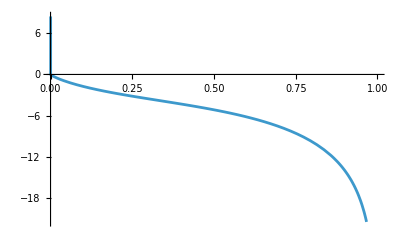

-4.21234-2.1292×10^-12 ⅈ

-4.21234

```mathematica
Total[totalIntegrands];
Plot[%//Re,{r,0,1}]
NIntegrate[%%,{r,0.000000001,0.999999999}]+(π^2-6 Zeta[3])//N
3-6Zeta[3]//N
```

Mathematica cannot integrate the following three integrands

```mathematica
totalIntegrands[[111]]
totalIntegrands[[113]]
totalIntegrands[[115]]
```

-5/2 PolyLog[3,(1+r)/(1-r)]

5/2 PolyLog[3,(1+r)/(-1+r)]

-5/4 PolyLog[3,1-r^2]

Thus, we define remaining part, which Mathematica can integrate automatically.

```mathematica
totalIntegrandsP=Delete[totalIntegrands,{{111},{113},{115}}];
```

we can calculate three indefinite integrals ∫PolyLog[3,(1+r)/(1-r)]ⅆr ,∫PolyLog[3,(1+r)/(-1+r)]ⅆr , ∫PolyLog[3,1-r^2]ⅆr by hand.

```mathematica
PL3int1=r PolyLog[3,(1+r)/(1-r)]+1/6 (Log[8] Log[-1+r]^2-Log[-1+r]^3+3 Log[-1+r]^2 Log[r]-3 Log[-1+r]^2 Log[(2 r)/(-1+r)]+3 Log[1/(1-r)] Log[(2 r)/(-1+r)]^2-6 Log[-1+r] Log[-r] Log[(1+r)/2]+3 Log[-r]^2 Log[(1+r)/2]+6 Log[-1+r] Log[(2 r)/(-1+r)] Log[(1+r)/2]-6 Log[-r] Log[(2 r)/(-1+r)] Log[(1+r)/2]+3 Log[(2 r)/(-1+r)]^2 Log[(1+r)/2]-3 Log[2] Log[(1+r)/2] (-2 Log[r]+Log[(1+r)/2])+6 Log[-1+r] Log[-r] Log[1+r]-3 Log[-r]^2 Log[1+r]-6 Log[1-r] Log[r] Log[1+r]+6 Log[-r] Log[(2 r)/(-1+r)] Log[1+r]+3 (Log[1-r]-Log[2 (-1+r)]) Log[1+r]^2-3 (Log[-r]-Log[r]) Log[1+r]^2-3 Log[(2 r)/(-1+r)]^2 Log[(1+r)/(1-r)]+6 Log[2] Log[(1+r)/2] Log[(1+r)/(2 r)]-3 (Log[1-r]+Log[-1/r]-Log[(-1+r)/(2 r)]) Log[(1+r)/(2 r)]^2-12 Log[-1+r] PolyLog[2,(1-r)/2]+6 Log[-1+r] PolyLog[2,1-r]+6 Log[-1+r] PolyLog[2,-r]+6 Log[(2 r)/(-1+r)] PolyLog[2,-r]-6 (Log[1+r]-Log[(1+r)/(2 r)]) PolyLog[2,r]+6 Log[(2 r)/(-1+r)] PolyLog[2,r/(-1+r)]-6 Log[(2 r)/(-1+r)] PolyLog[2,(2 r)/(-1+r)]+6 Log[1+r] PolyLog[2,(1+r)/2]-6 (Log[r]+Log[(1+r)/(2 r)]) PolyLog[2,(1+r)/2]-3 (Log[-1+r]-Log[r]+Log[(2 r)/(-1+r)]) (Log[1+r] (2 Log[1-r]-Log[4+4 r])+2 PolyLog[2,(1+r)/2])-6 Log[1+r] PolyLog[2,1+r]+6 Log[-1+r] PolyLog[2,(1+r)/(1-r)]+6 Log[1+r] PolyLog[2,(1+r)/(1-r)]-6 Log[(1+r)/(2 r)] (PolyLog[2,1+1/r]-PolyLog[2,(1+r)/(2 r)])+6 PolyLog[3,1+1/r]+12 PolyLog[3,(1-r)/2]-6 PolyLog[3,1-r]-6 PolyLog[3,-r]+6 PolyLog[3,r]-6 PolyLog[3,r/(-1+r)]+6 PolyLog[3,(2 r)/(-1+r)]+6 PolyLog[3,1+r]-6 PolyLog[3,(1+r)/(2 r)]);

PL3int2=1/6 (Log[8] Log[-1+r]^2+3 (Log[1-r]-Log[2 (-1+r)]) Log[1+r]^2-Log[-1+r] (6 Log[2]^2+Log[8] Log[-1+r]+Log[-1+r]^2+Log[1/(1-r)] (Log[64]+3 Log[-1+r]-6 Log[1+r])-Log[64] Log[1+r])+(Log[64]+6 Log[1/(1-r)]-6 Log[-1+r]) PolyLog[2,(1-r)/2]-6 Log[-1+r] PolyLog[2,(1-r)/2]+6 Log[1+r] PolyLog[2,(1+r)/2]-3 (Log[-2/(-1+r)]+Log[-1+r]) (Log[1+r] (2 Log[1-r]-Log[4+4 r])+2 PolyLog[2,(1+r)/2])+6 Log[-1+r] PolyLog[2,(1+r)/(-1+r)]+6 Log[1+r] PolyLog[2,(1+r)/(-1+r)]+18 PolyLog[3,(1-r)/2]-6 PolyLog[3,(1+r)/2])+r PolyLog[3,(1+r)/(-1+r)];

PL3int3=8 r+Log[2] Log[-r] (-2 Log[1-r]+Log[-r])-8 r Log[r]-2 Log[2] Log[-r] Log[(2 r)/(-1+r)]-2 Log[1-r] Log[r] Log[(1+r)/2]+Log[2] Log[(1+r)/2] (-2 Log[r]+Log[(1+r)/2])+2 (2 Log[r]-Log[r^2]) (2 r+Log[1-r]-Log[1+r])+4 Log[r] Log[1+r]+2 Log[1-r] Log[r] Log[1+r]-(Log[-r]-Log[r]) Log[1+r]^2-Log[(2 r)/(-1+r)]^2 (Log[1/(2-2 r)]+Log[1+r]-Log[-(1+r)/(-1+r)])-2 Log[2] Log[(1+r)/2] Log[(1+r)/(2 r)]+(Log[1-r]+Log[-1/r]-Log[(-1+r)/(2 r)]) Log[(1+r)/(2 r)]^2-1/2 (2 Log[r]-Log[r^2]) (Log[4] Log[1-r]+Log[1+r]^2-2 PolyLog[2,(1-r)/2])-2 (Log[r]-Log[(2 r)/(-1+r)]) PolyLog[2,(1-r)/2]+4 PolyLog[2,1-r]+2 Log[1-r] PolyLog[2,1-r]+4 PolyLog[2,-r]-2 (Log[2-2 r]+Log[r/(-1+r)]) PolyLog[2,-r]+2 (Log[1+r]-Log[(1+r)/(2 r)]) PolyLog[2,r]-2 Log[(2 r)/(-1+r)] (PolyLog[2,r/(-1+r)]-PolyLog[2,(2 r)/(-1+r)])+1/2 (2 Log[r]-Log[r^2]) (Log[1-r]^2+Log[4] Log[1+r]-2 PolyLog[2,(1+r)/2])+2 (Log[r]+Log[(1+r)/(2 r)]) PolyLog[2,(1+r)/2]-2 Log[1+r] PolyLog[2,1+r]+2 Log[(1+r)/(2 r)] (PolyLog[2,1+1/r]-PolyLog[2,(1+r)/(2 r)])-(2 r+Log[1-r]-Log[1+r]) PolyLog[2,1-r^2]-2 PolyLog[3,1+1/r]+2 PolyLog[3,(1-r)/2]-2 PolyLog[3,1-r]+2 PolyLog[3,-r]-2 PolyLog[3,r]+2 PolyLog[3,r/(-1+r)]-2 PolyLog[3,(2 r)/(-1+r)]-2 PolyLog[3,(1+r)/2]+2 PolyLog[3,1+r]+2 PolyLog[3,(1+r)/(2 r)]+r PolyLog[3,1-r^2];
```

r - integration

```mathematica
Total[Integrate[totalIntegrandsP,r]]-5/2 PL3int1+5/2 PL3int2 -5/4 PL3int3//Expand;
result=Apart[%//Simplify,r]
```

15+10 ArcTanh[r]+5/2 HarmonicPolyLog[{-2,1},r]-8 HarmonicPolyLog[{2,-1},r]+16 Log[2]^2-Log[4]-2 Log[1+1/r]^2-1/2 Log[1/4 (-1-r)] Log[-1-r]+11/2 Log[1-r]-8 Log[2] Log[1-r]-5 ⅈ π Log[2] Log[1-r]+Log[4] Log[1-r]+5/2 ⅈ π Log[4] Log[1-r]+3/2 Log[1/2 (1+1/r)]^2 Log[1-r]+5/4 Log[4] Log[4-4 r] Log[1-r]-Log[-1-r] Log[1-r]+9/2 Log[-1+r]-5/2 Log[2]^2 Log[-1+r]-Log[256] Log[-1+r]-5/4 Log[4] Log[4-4 r] Log[-1+r]-5/12 Log[64] Log[1/(1-r)] Log[-1+r]+8 Log[1-r] Log[-1+r]+5/2 Log[4-4 r] Log[1-r] Log[-1+r]-21/2 Log[1-r]^2 Log[-1+r]-15/2 Log[1-r] Log[-2/(-1+r)] Log[-1+r]-8 Log[-1+r]^2-21/4 Log[2] Log[-1+r]^2-5/4 Log[4] Log[-1+r]^2-5/12 Log[8] Log[-1+r]^2-5/4 Log[4-4 r] Log[-1+r]^2-5/4 Log[1/(1-r)] Log[-1+r]^2+39/4 Log[1-r] Log[-1+r]^2+25/4 Log[-2/(-1+r)] Log[-1+r]^2-3 Log[-1+r]^3+2 Log[4] Log[-1/r]+3/2 Log[1/2 (1+1/r)]^2 Log[-1/r]+4 Log[1+1/r] Log[-1/r]-3/2 Log[1/2 (1+1/r)]^2 Log[(-1+r)/(2 r)]-(25 Log[-r])/2+5/2 Log[2] Log[1-r] Log[-r]+2 Log[-1+r] Log[-r]+9 Log[2] Log[-1+r] Log[-r]+5/2 Log[8] Log[-1+r] Log[-r]-Log[16] Log[-1+r] Log[-r]-5/2 Log[64] Log[-1+r] Log[-r]-Log[-r]^2-19/2 Log[2] Log[-r]^2+Log[4] Log[-r]^2+5/2 Log[8] Log[-r]^2+1/3 π^2 (-2+Log[r])-(37 Log[r])/2-19/12 π^2 Log[r]+21/4 Log[2]^2 Log[r]+2 Log[4] Log[r]-26 Log[1-r] Log[r]+11/2 Log[2] Log[1-r] Log[r]-21/4 Log[4] Log[1-r] Log[r]-5/2 Log[4-4 r] Log[1-r] Log[r]+5/2 Log[1-r]^2 Log[r]+5 Log[1-r] Log[-2/(-1+r)] Log[r]-2 Log[-1+r] Log[r]+5 Log[4] Log[-1+r] Log[r]+9/2 Log[1-r] Log[-1+r] Log[r]-6 Log[r]^2+1/2 (25 Log[-r]+21 Log[r])+Log[32] Log[1-r] Log[r/(-1+r)]+5/2 Log[4-4 r] Log[1-r] Log[r/(-1+r)]-Log[32] Log[-1+r] Log[r/(-1+r)]+5 Log[1-r] Log[-1+r] Log[r/(-1+r)]-5/2 Log[-1+r]^2 Log[r/(-1+r)]-10 Log[1-r] Log[r] Log[r/(-1+r)]+5 Log[1-r] Log[r/(-1+r)]^2+2 Log[1/(1-r)] Log[(2 r)/(-1+r)]-5/2 Log[1-r]^2 Log[(2 r)/(-1+r)]-5/2 Log[4] Log[-1+r] Log[(2 r)/(-1+r)]-15/2 Log[1-r] Log[-1+r] Log[(2 r)/(-1+r)]+5/2 Log[-1+r]^2 Log[(2 r)/(-1+r)]+2 Log[-r] Log[(2 r)/(-1+r)]+15 Log[1-r] Log[r] Log[(2 r)/(-1+r)]-Log[(2 r)/(-1+r)]^2-15/4 Log[1/(1-r)] Log[(2 r)/(-1+r)]^2-15/2 Log[1-r] Log[(2 r)/(-1+r)]^2+15/4 Log[1-r] Log[r^2]-5/8 Log[4] Log[1-r] Log[r^2]+5/2 Log[1-r] Log[r] Log[r^2]+5/4 Log[4] Log[1-r] Log[(1-r)/(1+r)]+5 Log[1-r] Log[-2/(-1+r)] Log[(1-r)/(1+r)]-5/4 Log[4] Log[-1+r] Log[(1-r)/(1+r)]+5 Log[1-r] Log[-1+r] Log[(1-r)/(1+r)]-5 Log[-2/(-1+r)] Log[-1+r] Log[(1-r)/(1+r)]-5/2 Log[-1+r]^2 Log[(1-r)/(1+r)]-5 Log[1-r] Log[r] Log[(1-r)/(1+r)]-5 Log[-2/(-1+r)] Log[r] Log[(1-r)/(1+r)]-5 Log[-1+r] Log[r] Log[(1-r)/(1+r)]+5/2 Log[1-r] Log[r/(-1+r)] Log[(1-r)/(1+r)]-5/2 Log[1-r] Log[(2 r)/(-1+r)] Log[(1-r)/(1+r)]+5 Log[-1+r] Log[(2 r)/(-1+r)] Log[(1-r)/(1+r)]+5/2 Log[(2 r)/(-1+r)]^2 Log[(1-r)/(1+r)]+2 Log[(1+r)/2]-3 Log[2] Log[1/2 (1+1/r)] Log[(1+r)/2]+Log[1-r] Log[(1+r)/2]-4 Log[-1+r] Log[(1+r)/2]-5/2 Log[1-r] Log[-1+r] Log[(1+r)/2]-5/2 Log[-2/(-1+r)] Log[-1+r] Log[(1+r)/2]-51/4 Log[-1+r]^2 Log[(1+r)/2]+2 Log[-r] Log[(1+r)/2]+5 Log[1-r] Log[-r] Log[(1+r)/2]+5/2 Log[-1+r] Log[-r] Log[(1+r)/2]-15/4 Log[-r]^2 Log[(1+r)/2]-2 Log[r] Log[(1+r)/2]-3 Log[2] Log[r] Log[(1+r)/2]+5/2 Log[1-r] Log[r] Log[(1+r)/2]+10 Log[-1+r] Log[r] Log[(1+r)/2]-15 Log[-1+r] Log[(2 r)/(-1+r)] Log[(1+r)/2]+15/2 Log[-r] Log[(2 r)/(-1+r)] Log[(1+r)/2]-15/4 Log[(2 r)/(-1+r)]^2 Log[(1+r)/2]-5/2 Log[1-r] Log[r^2] Log[(1+r)/2]-5/2 Log[-1+r] Log[(1-r)/(1+r)] Log[(1+r)/2]+3/2 Log[2] Log[(1+r)/2]^2-5/2 Log[1+r]+25/2 ⅈ π Log[1+r]+2 Log[16] Log[1+r]+4 Log[1+1/r] Log[1+r]-5/4 Log[4] Log[4-4 r] Log[1+r]+4 Log[(1-r)/2] Log[1+r]+23 Log[1-r] Log[1+r]+5/4 Log[4] Log[1-r] Log[1+r]+5/2 Log[(1-r)/2] Log[-2/(-1+r)] Log[1+r]-4 Log[-1+r] Log[1+r]+5/12 Log[64] Log[-1+r] Log[1+r]+5/2 Log[1/(1-r)] Log[-1+r] Log[1+r]-5 Log[(1-r)/2] Log[-1+r] Log[1+r]+31/2 Log[1-r] Log[-1+r] Log[1+r]-5/2 Log[-2/(-1+r)] Log[-1+r] Log[1+r]+9/4 Log[-1+r]^2 Log[1+r]-2 Log[-r] Log[1+r]-5 Log[1-r] Log[-r] Log[1+r]-15/2 Log[-1+r] Log[-r] Log[1+r]+15/4 Log[-r]^2 Log[1+r]-7/2 Log[r] Log[1+r]+5/4 Log[4] Log[r] Log[1+r]+15/2 Log[(1-r)/2] Log[r] Log[1+r]-15 Log[1-r] Log[r] Log[1+r]-5 Log[-2/(-1+r)] Log[r] Log[1+r]-15 Log[-1+r] Log[r] Log[1+r]-Log[32] Log[r/(-1+r)] Log[1+r]-5/2 Log[4-4 r] Log[r/(-1+r)] Log[1+r]+5/2 Log[1-r] Log[r/(-1+r)] Log[1+r]+5 Log[r] Log[r/(-1+r)] Log[1+r]-5 Log[r/(-1+r)]^2 Log[1+r]-15/2 Log[(1-r)/2] Log[(2 r)/(-1+r)] Log[1+r]+5 Log[1-r] Log[(2 r)/(-1+r)] Log[1+r]+35/2 Log[-1+r] Log[(2 r)/(-1+r)] Log[1+r]-15/2 Log[-r] Log[(2 r)/(-1+r)] Log[1+r]-5 Log[r] Log[(2 r)/(-1+r)] Log[1+r]+15/2 Log[(2 r)/(-1+r)]^2 Log[1+r]+15/4 Log[r^2] Log[1+r]+5/8 Log[4] Log[r^2] Log[1+r]+5/4 Log[1-r] Log[r^2] Log[1+r]+15/4 Log[r] Log[r^2] Log[1+r]-5/4 Log[4] Log[(1-r)/(1+r)] Log[1+r]+5/2 Log[-1+r] Log[(1-r)/(1+r)] Log[1+r]-5/2 Log[r/(-1+r)] Log[(1-r)/(1+r)] Log[1+r]+5/2 Log[(2 r)/(-1+r)] Log[(1-r)/(1+r)] Log[1+r]-3/2 Log[1+r]^2-5/4 Log[4] Log[1+r]^2+5/4 Log[(1-r)/2] Log[1+r]^2-5/4 Log[1-r] Log[1+r]^2+5/4 Log[-2/(-1+r)] Log[1+r]^2-5/4 Log[-1+r] Log[1+r]^2+5/4 Log[2 (-1+r)] Log[1+r]^2+5/2 Log[-r] Log[1+r]^2-15/4 Log[r] Log[1+r]^2-5/2 Log[r/(-1+r)] Log[1+r]^2+5/4 Log[(2 r)/(-1+r)] Log[1+r]^2-2/3 (π^2+Log[64]+Log[4096] Log[1-r]^2+Log[4096] Log[-1+r]-Log[4096] Log[1-r] Log[-1+r]+Log[4096] Log[-1/r]+π^2 Log[r]+Log[4096] Log[r]+Log[4096] Log[1-r] Log[r]+Log[4096] Log[1+r]+Log[16777216] Log[1+r]+Log[4096] Log[1-r] Log[1+r]-Log[4096] Log[-1+r] Log[1+r])+1/2 Log[2 (1+r)]+5/4 Log[-2/(-1+r)] Log[1+r] Log[4 (1+r)]+5/4 Log[r] Log[1+r] Log[4 (1+r)]-5/4 Log[(2 r)/(-1+r)] Log[1+r] Log[4 (1+r)]+15/4 Log[(2 r)/(-1+r)]^2 Log[(1+r)/(1-r)]-5 Log[-r] Log[1+r] Log[(1+r)/(1-r)]+5 Log[r] Log[1+r] Log[(1+r)/(1-r)]+4 Log[1/(1-r)] Log[(1+r)/(1-r)]^2-13/2 Log[-2/(-1+r)] Log[(1+r)/(1-r)]^2-5/2 Log[r] Log[(1+r)/(1-r)]^2-4 Log[r/(-1+r)] Log[(1+r)/(1-r)]^2+13/2 Log[(2 r)/(-1+r)] Log[(1+r)/(1-r)]^2-3 Log[1-r^2]+(2 Log[1-r^2])/r^2+Log[-1-r] Log[1-r^2]-8 Log[1-r] Log[1-r^2]+8 Log[1-r]^2 Log[1-r^2]+5/2 Log[1-r] Log[-2/(-1+r)] Log[1-r^2]+8 Log[-1+r] Log[1-r^2]-5/4 Log[4] Log[-1+r] Log[1-r^2]-16 Log[1-r] Log[-1+r] Log[1-r^2]+8 Log[-1+r]^2 Log[1-r^2]+12 Log[r] Log[1-r^2]+21/2 Log[1-r] Log[r] Log[1-r^2]-5/2 Log[1-r] Log[(2 r)/(-1+r)] Log[1-r^2]-5/2 Log[-1+r] Log[(1+r)/2] Log[1-r^2]-Log[1+r] Log[1-r^2]-5/2 Log[-2/(-1+r)] Log[1+r] Log[1-r^2]+5/2 Log[-1+r] Log[1+r] Log[1-r^2]+5/2 Log[(2 r)/(-1+r)] Log[1+r] Log[1-r^2]+r^2 (Log[1-r]-4 Log[r]+Log[1+r]+Log[1-r^2])-3 Log[1/2 (1+1/r)] PolyLog[2,1/2 (1+1/r)]+4 PolyLog[2,1+1/r]+3 Log[1/2 (1+1/r)] PolyLog[2,1+1/r]+19 PolyLog[2,(1-r)/2]+5/12 Log[64] PolyLog[2,(1-r)/2]+5/2 Log[4-4 r] PolyLog[2,(1-r)/2]+5/2 Log[1/(1-r)] PolyLog[2,(1-r)/2]+11/2 Log[1-r] PolyLog[2,(1-r)/2]-5/2 Log[-2/(-1+r)] PolyLog[2,(1-r)/2]-13 Log[-1+r] PolyLog[2,(1-r)/2]+21/2 Log[r] PolyLog[2,(1-r)/2]+5/2 Log[(2 r)/(-1+r)] PolyLog[2,(1-r)/2]-5/4 Log[r^2] PolyLog[2,(1-r)/2]-5/2 Log[4-4 r^2] PolyLog[2,(1-r)/2]+5/2 Log[1-r^2] PolyLog[2,(1-r)/2]-10 PolyLog[2,1-r]-5/2 Log[4-4 r] PolyLog[2,1-r]+5/2 Log[1-r] PolyLog[2,1-r]-1/2 Log[-1+r] PolyLog[2,1-r]-5 Log[r/(-1+r)] PolyLog[2,1-r]+10 Log[(2 r)/(-1+r)] PolyLog[2,1-r]-5/4 Log[r^2] PolyLog[2,1-r]-5 Log[(1-r)/(1+r)] PolyLog[2,1-r]-41/2 Log[1+r] PolyLog[2,1-r]+5 Log[(1+r)/(1-r)] PolyLog[2,1-r]+21/2 Log[1-r^2] PolyLog[2,1-r]+1/2 PolyLog[2,-r]+15/2 ⅈ π PolyLog[2,-r]-5/2 Log[4-4 r] PolyLog[2,-r]+5/2 Log[2-2 r] PolyLog[2,-r]-5/2 Log[1-r] PolyLog[2,-r]-5 Log[-2/(-1+r)] PolyLog[2,-r]-15/2 Log[-1+r] PolyLog[2,-r]-25/2 Log[-r] PolyLog[2,-r]+15/2 Log[r] PolyLog[2,-r]-5/2 Log[r/(-1+r)] PolyLog[2,-r]+15/4 Log[r^2] PolyLog[2,-r]-5/2 Log[1+r] PolyLog[2,-r]+5/2 Log[1-r^2] PolyLog[2,-r]-16 PolyLog[2,r]+5 ⅈ π PolyLog[2,r]-3 Log[1/2 (1+1/r)] PolyLog[2,r]+5 Log[-2/(-1+r)] PolyLog[2,r]+2 Log[-1+r] PolyLog[2,r]+5 Log[r] PolyLog[2,r]+5/2 Log[r^2] PolyLog[2,r]-5 Log[(1-r)/(1+r)] PolyLog[2,r]-10 Log[1+r] PolyLog[2,r]+8 Log[1-r^2] PolyLog[2,r]+2 PolyLog[2,r/(-1+r)]-15/2 Log[(2 r)/(-1+r)] PolyLog[2,r/(-1+r)]+15/2 Log[(2 r)/(-1+r)] PolyLog[2,(2 r)/(-1+r)]+7/4 PolyLog[2,r^2]+1/(2 (1+r))(-4 Log[2-2 r]+4 Log[1-r]+11 Log[r]-8 Log[1-r] Log[r]+8 Log[r]^2-4 Log[(1+r)/2]+4 Log[1+r]+2 Log[r] Log[1+r]+8 Log[r]^2 Log[1+r]-8 Log[r] Log[1-r^2]-8 Log[r]^2 Log[1-r^2]-10 PolyLog[2,r]-8 Log[r] PolyLog[2,r]-5 PolyLog[2,r^2]-4 Log[r] PolyLog[2,r^2])+(-5 Log[r]^2-8 Log[r]^2 Log[1+r]+8 Log[r]^2 Log[1-r^2]+8 Log[r] PolyLog[2,r]+4 Log[r] PolyLog[2,r^2])/(2 (1+r)^2)+(-5 Log[r]^2-8 Log[1-r] Log[r]^2+8 Log[r]^2 Log[1-r^2]-8 Log[r] PolyLog[2,r]+8 Log[r] PolyLog[2,r^2])/(2 (-1+r)^2)+1/(2 (-1+r))(-11 Log[r]-10 Log[1-r] Log[r]-8 Log[r]^2-8 Log[1-r] Log[r]^2+16 Log[r] Log[1-r^2]+8 Log[r]^2 Log[1-r^2]-10 PolyLog[2,r]-8 Log[r] PolyLog[2,r]+10 PolyLog[2,r^2]+8 Log[r] PolyLog[2,r^2])+19 PolyLog[2,(1+r)/2]+3 Log[1/2 (1+1/r)] PolyLog[2,(1+r)/2]+8 Log[1-r] PolyLog[2,(1+r)/2]-13 Log[-1+r] PolyLog[2,(1+r)/2]+21/2 Log[r] PolyLog[2,(1+r)/2]-5 Log[(2 r)/(-1+r)] PolyLog[2,(1+r)/2]-5/4 Log[r^2] PolyLog[2,(1+r)/2]+25/2 PolyLog[2,1+r]-5 Log[-1+r] PolyLog[2,1+r]-5 Log[(1+r)/(1-r)] PolyLog[2,1+r]-5/2 Log[-1+r] PolyLog[2,(1+r)/(1-r)]-5/2 Log[1+r] PolyLog[2,(1+r)/(1-r)]+5 Log[(1+r)/(1-r)] PolyLog[2,(1+r)/(1-r)]+5/2 Log[1-r^2] PolyLog[2,(1+r)/(1-r)]+5/2 Log[-1+r] PolyLog[2,(1+r)/(-1+r)]+5/2 Log[1+r] PolyLog[2,(1+r)/(-1+r)]-5 Log[(1+r)/(1-r)] PolyLog[2,(1+r)/(-1+r)]-5/2 Log[1-r^2] PolyLog[2,(1+r)/(-1+r)]+15/4 Log[r] PolyLog[2,1-r^2]+3 PolyLog[3,1/2 (1+1/r)]-3 PolyLog[3,1+1/r]+15/2 PolyLog[3,(1-r)/2]+5 PolyLog[3,1-r]-21/2 PolyLog[3,r]+15/2 PolyLog[3,r/(-1+r)]-15/2 PolyLog[3,(2 r)/(-1+r)]+15/8 PolyLog[3,r^2]-3 PolyLog[3,(1+r)/2]+5 PolyLog[3,1+r]-5 PolyLog[3,(1+r)/(1-r)]+5 PolyLog[3,(1+r)/(-1+r)]+1/(24 r)(60 HarmonicPolyLog[{-2,1},r]+60 HarmonicPolyLog[{-1,2},r]-120 HarmonicPolyLog[{1,2},r]+60 HarmonicPolyLog[{2,-1},r]+72 Log[1-r]-20 π^2 Log[1-r]-30 ⅈ π Log[1-r]^2+84 Log[1-r] Log[r]-36 Log[1-r] Log[r]^2+72 Log[1+r]+5 π^2 Log[1+r]+60 ⅈ π Log[1-r] Log[1+r]+84 Log[r] Log[1+r]+60 Log[1-r] Log[r] Log[1+r]+36 Log[r]^2 Log[1+r]+120 ⅈ π Log[1+r]^2-72 Log[1-r^2]-84 Log[r] Log[1-r^2]-240 Log[1-r] PolyLog[2,1-r]-72 Log[r] PolyLog[2,r]+18 Log[r] PolyLog[2,r^2]+300 Log[1+r] PolyLog[2,1+r]+60 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-60 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+30 Log[1-r] PolyLog[2,1-r^2]-60 Log[1+r] PolyLog[2,1-r^2]+300 PolyLog[3,1-r]-300 PolyLog[3,1+r]+60 PolyLog[3,(1+r)/(1-r)]-60 PolyLog[3,(1+r)/(-1+r)]+30 PolyLog[3,1-r^2]-135 Zeta[3])+r (-(25 ⅈ π)/2-(5 π^2)/8-5/2 HarmonicPolyLog[{-2,1},r]-5/2 HarmonicPolyLog[{-1,2},r]+5 HarmonicPolyLog[{1,2},r]-5/2 HarmonicPolyLog[{2,-1},r]-3 Log[1-r]+5/6 π^2 Log[1-r]+5/4 ⅈ π Log[1-r]^2+(25 Log[-r])/2-(25 Log[r])/2+9 Log[1-r] Log[r]+Log[1-r] Log[r]^2-5/2 Log[1-r] Log[r^2]-3 Log[1+r]+25/2 ⅈ π Log[1+r]-5/24 π^2 Log[1+r]-5/2 ⅈ π Log[1-r] Log[1+r]-25/2 Log[-r] Log[1+r]+4 Log[r] Log[1+r]-5/2 Log[1-r] Log[r] Log[1+r]-Log[r]^2 Log[1+r]+5 Log[r^2] Log[1+r]-5 ⅈ π Log[1+r]^2+3 Log[1-r^2]+Log[r] Log[1-r^2]+5/2 PolyLog[2,1-r]+10 Log[1-r] PolyLog[2,1-r]+5/2 PolyLog[2,r]+2 Log[r] PolyLog[2,r]+5/4 PolyLog[2,r^2]-1/2 Log[r] PolyLog[2,r^2]-25/2 Log[1+r] PolyLog[2,1+r]-5/2 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+5/2 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+5/4 PolyLog[2,1-r^2]-5/4 Log[1-r] PolyLog[2,1-r^2]+5/2 Log[1+r] PolyLog[2,1-r^2]-25/2 PolyLog[3,1-r]+25/2 PolyLog[3,1+r]-5/2 PolyLog[3,(1+r)/(1-r)]+5/2 PolyLog[3,(1+r)/(-1+r)]-5/4 PolyLog[3,1-r^2]+(45 Zeta[3])/8)

express HarmonicPolyLog in terms of PolyLog (for 0<r<1)

```mathematica
S12[x_]:=(Log[1-x]^2 Log[x]+2 Log[1-x] PolyLog[2,1-x]-2 PolyLog[3,1-x]+2 Zeta[3])/2;   (* =PolyLog[1,2,x]*)

S22[x_]:=PolyLog[4,x]-PolyLog[4,1-x]+PolyLog[4,x/(x-1)]-Log[1-x] PolyLog[3,x]+Zeta[3] Log[1-x]+Pi^2 Log[1-x]^2/12+Log[1-x]^4/24-Log[x] Log[1-x]^3/6+Pi^4/90;

S22m[x_]:=PolyLog[4,-x]+PolyLog[4,1/(1+x)]+PolyLog[4,x/(1+x)]-Log[1+x] PolyLog[3,-x]+Zeta[3] Log[1+x]-Pi^2 Log[1+x]^2/12+Log[1+x]^4/12-Log[x] Log[1+x]^3/6-Pi^4/90;

F31[x_]:=-3/2 PolyLog[4,x]+3/2 PolyLog[4,-x]+2 PolyLog[4,2x/(1+x)]-2 PolyLog[4,(1+x)/2]-1/4 PolyLog[4,4x/(1+x)^2]-S22m[x]+Log[1+x] (PolyLog[3,x]-PolyLog[3,-x])+Log[1+x] (Log[2]^3/3-Pi^2 Log[2]/6+7/4 Zeta[3])+Log[2] Log[1+x]^3/3-Log[1+x]^4/12+(Pi^2/12-Log[2]^2/2) Log[1+x]^2+2 PolyLog[4,1/2];

F31m[x_]:=-3/2 PolyLog[4,-x]+3/2 PolyLog[4,x]+2 PolyLog[4,-2 x/(1-x)]-2 PolyLog[4,(1-x)/2]-1/4 PolyLog[4,-4 x/(1-x)^2]-S22[x]+Log[1-x] (PolyLog[3,-x]-PolyLog[3,x])+Log[1-x] (Log[2]^3/3-Pi^2 Log[2]/6+7/4 Zeta[3])+Log[2] Log[1-x]^3/3-Log[1-x]^4/12+(Pi^2/12-Log[2]^2/2) Log[1-x]^2+2 PolyLog[4,1/2];

hplRules={HarmonicPolyLog[{-1,2},x_]:>Log[1+x] PolyLog[2,x]-HarmonicPolyLog[{-2,1},x]-HarmonicPolyLog[{2,-1},x],HarmonicPolyLog[{1,2},x_]:>-Log[1-x] PolyLog[2,x]-2 S12[x],HarmonicPolyLog[{2,-1},x_]:>With[{a=Log[x],c=Log[1+x],d=Log[2]},-a c^2/2+2c^3/3-c^2 d+c d^2-d^3/3+c PolyLog[2,1/(1+x)]+d (PolyLog[2,x]-PolyLog[2,-x])+(c-d)(PolyLog[2,2x/(1+x)]+PolyLog[2,(1+x)/2])+PolyLog[3,-x]-PolyLog[3,x]+PolyLog[3,2x/(1+x)]-PolyLog[3,(1+x)/2]+PolyLog[3,1/(1+x)]-Zeta[3]/8],HarmonicPolyLog[{-2,1},x_]:>With[{a=Log[x],b=Log[1-x],d=Log[2]},-a b^2/2+b^3/3-b^2 d+b d^2-d^3/3-b PolyLog[2,1-x]-d (PolyLog[2,x]-PolyLog[2,-x])+(b-d)(PolyLog[2,-2x/(1-x)]+PolyLog[2,(1-x)/2])+PolyLog[3,x]-PolyLog[3,-x]+PolyLog[3,-2x/(1-x)]-PolyLog[3,(1-x)/2]+PolyLog[3,1-x]-Zeta[3]/8],HarmonicPolyLog[{2,2},x_]:>PolyLog[2,x]^2/2-2 S22[x],HarmonicPolyLog[{3,-1},x_]:>F31[x],HarmonicPolyLog[{-3,1},x_]:>F31m[x]};
```

check of hplRules: the series of HPLterms around r=0 before and after applying hplRules agree, so the output below should contain only O(r^11)

```mathematica
HPLterms={5/2 HarmonicPolyLog[{-2,1},r],(5 HarmonicPolyLog[{-2,1},r])/(2 r),-5/2 r HarmonicPolyLog[{-2,1},r],(5 HarmonicPolyLog[{-1,2},r])/(2 r),-5/2 r HarmonicPolyLog[{-1,2},r],-(5 HarmonicPolyLog[{1,2},r])/r,5 r HarmonicPolyLog[{1,2},r],-8 HarmonicPolyLog[{2,-1},r],(5 HarmonicPolyLog[{2,-1},r])/(2 r),-5/2 r HarmonicPolyLog[{2,-1},r]};
%//.hplRules;
Assuming[0<r<1,Series[%,{r,0,10}]]/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]//Normal};
Assuming[0<r<1,Series[HPLterms,{r,0,10}]//Normal];
%%-%
```

{O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11}

evaluate the indefinite integral at r=0

```mathematica
result//.hplRules//Expand;
Assuming[0<r<1,Series[%,{r,0,0}]//Normal];
lowerlimit=%/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]}//Expand
```

13+(9 ⅈ π)/2+(121 π^2)/12-(ⅈ π^3)/12-(15 Log[2])/2-17 ⅈ π Log[2]-11 π^2 Log[2]-4 Log[2]^2+83/4 ⅈ π Log[2]^2+(25 Log[2]^3)/4+(83 Zeta[3])/16

evaluate the indefinite integral at r=1

```mathematica
result//.hplRules//Expand;
Assuming[0<r<1,Series[%,{r,1,0}]//Normal];
upperlimit=%/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]}//FunctionExpand//Expand
```

16+(9 ⅈ π)/2+(109 π^2)/12-(ⅈ π^3)/12-(15 Log[2])/2-17 ⅈ π Log[2]-11 π^2 Log[2]-4 Log[2]^2+83/4 ⅈ π Log[2]^2+(25 Log[2]^3)/4+(83 Zeta[3])/16

collecting all contributions

```mathematica
upperlimit-lowerlimit+(π^2-6 Zeta[3])
```

3-6 Zeta[3]

## -1/c F_1122^SG calculation (equation (3.29))

## equations -(A.2) ~ -(A.5)

```mathematica
(* equation -(A.2) *)
evenleftC[n1_,n2_]:=-1/(105 n1 n2^2)4 (-1+n1^2) r^(-3+n1+n2) (1+r^2) (-2+n2 Log[r^2]) (-4 (-6+15 n1^2+n1^4) (1+r^2)+n1 (-4+n1^2) (7 n1 (-1+r^2)+3 (1+r^2)+2 n1^2 (1+r^2)) Log[r^2])

(* equation -(A.3) *)
oddleftC[n1_,n2_]:=1/(105 n1 n2^2)2 (-1+n1^2) r^(-4+n1+n2) (1+r^2) (-2+n2 Log[r^2]) (-2 (-48 (1-r^2+r^4)+n1^4 (1+6 r^2+r^4)+8 n1^2 (1+13 r^2+r^4))+n1 (-4+n1^2) (7 n1 (-1+r^4)+12 (1-r^2+r^4)+n1^2 (1+6 r^2+r^4)) Log[r^2])

(* equation -(A.4) *)
evenrightC[n1_,n2_]:=-1/(105 n1^2 n2)(-1+n2^2) r^(-3+n1+n2) (1+r^2) (-2+n2 Log[r^2]) (-2 (-48+35 n1^4-48 n2^2+15 n2^4-42 n1^2 (-4+n2^2)) (1+r^2)+n1 (70 n1^3 (-1+r^2)-14 n1 (8+3 n2^2) (-1+r^2)+35 n1^4 (1+r^2)-14 n1^2 (-2+3 n2^2) (1+r^2)+3 (-16-16 n2^2+5 n2^4) (1+r^2)) Log[r^2])

(* equation -(A.5) *)
oddrightC[n1_,n2_]:=1/(420 n1^2 n2)(-1+n2^2) r^(-4+n1+n2) (1+r^2) (-2+n2 Log[r^2]) (-70 n1^4 (1+6 r^2+r^4)+28 n1^2 (-17-62 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))-6 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))+n1 (140 n1^3 (-1+r^4)-28 n1 (-7+3 n2^2) (-1+r^4)+35 n1^4 (1+6 r^2+r^4)-14 n1^2 (-17+18 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))+3 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))) Log[r^2])
```

## -∑_(n2=2)^∞ (A.2)

```mathematica
diagIntegrand=Sum[evenleftC[n2,n2],{n2,2,Infinity}]
```

1/(105 r^3 (-1+r^2)^6)8 (-60 r^2+96 r^4+60 r^6-192 r^8+60 r^10+96 r^12-60 r^14+4 r^2 Log[r^2]+41 r^4 Log[r^2]+196 r^6 Log[r^2]-245 r^8 Log[r^2]+155 r^12 Log[r^2]-200 r^14 Log[r^2]+49 r^16 Log[r^2]+6 r^2 Log[r^2]^2-21 r^4 Log[r^2]^2+14 r^6 Log[r^2]^2-408 r^8 Log[r^2]^2-182 r^10 Log[r^2]^2+175 r^12 Log[r^2]^2-78 r^14 Log[r^2]^2+14 r^16 Log[r^2]^2-84 Log[1-r^2]+336 r^2 Log[1-r^2]-336 r^4 Log[1-r^2]-336 r^6 Log[1-r^2]+840 r^8 Log[1-r^2]-336 r^10 Log[1-r^2]-336 r^12 Log[1-r^2]+336 r^14 Log[1-r^2]-84 r^16 Log[1-r^2]+28 Log[r^2] Log[1-r^2]-168 r^2 Log[r^2] Log[1-r^2]+392 r^4 Log[r^2] Log[1-r^2]-392 r^6 Log[r^2] Log[1-r^2]+392 r^10 Log[r^2] Log[1-r^2]-392 r^12 Log[r^2] Log[1-r^2]+168 r^14 Log[r^2] Log[1-r^2]-28 r^16 Log[r^2] Log[1-r^2]+6 Log[r^2]^2 Log[1-r^2]-24 r^2 Log[r^2]^2 Log[1-r^2]+24 r^4 Log[r^2]^2 Log[1-r^2]+24 r^6 Log[r^2]^2 Log[1-r^2]-60 r^8 Log[r^2]^2 Log[1-r^2]+24 r^10 Log[r^2]^2 Log[1-r^2]+24 r^12 Log[r^2]^2 Log[1-r^2]-24 r^14 Log[r^2]^2 Log[1-r^2]+6 r^16 Log[r^2]^2 Log[1-r^2]+24 Log[r^2] PolyLog[2,r^2]-96 r^2 Log[r^2] PolyLog[2,r^2]+96 r^4 Log[r^2] PolyLog[2,r^2]+96 r^6 Log[r^2] PolyLog[2,r^2]-240 r^8 Log[r^2] PolyLog[2,r^2]+96 r^10 Log[r^2] PolyLog[2,r^2]+96 r^12 Log[r^2] PolyLog[2,r^2]-96 r^14 Log[r^2] PolyLog[2,r^2]+24 r^16 Log[r^2] PolyLog[2,r^2]-24 PolyLog[3,r^2]+96 r^2 PolyLog[3,r^2]-96 r^4 PolyLog[3,r^2]-96 r^6 PolyLog[3,r^2]+240 r^8 PolyLog[3,r^2]-96 r^10 PolyLog[3,r^2]-96 r^12 PolyLog[3,r^2]+96 r^14 PolyLog[3,r^2]-24 r^16 PolyLog[3,r^2])

## -∑_(n1>n2, n1-n2∈2Z)^∞ (A.4)

split (A.4) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,evenrightC[n1,n2]//FunctionExpand//Simplify]
CoefficientList[%,Log[r]]//Simplify
evenRightNonLog=Apply[List,%[[1]]//Expand]
evenRightLinearLog=Apply[List,%%[[2]]//Expand]
evenRightQuadLog=Apply[List,%%%[[3]]//Expand]
```

-1/(105 n1^2 n2)4 (-1+n2^2) r^(-3+n1+n2) (1+r^2) (-1+n2 Log[r]) (-((-48+35 n1^4-48 n2^2+15 n2^4-42 n1^2 (-4+n2^2)) (1+r^2))+n1 (70 n1^3 (-1+r^2)-14 n1 (8+3 n2^2) (-1+r^2)+35 n1^4 (1+r^2)-14 n1^2 (-2+3 n2^2) (1+r^2)+3 (-16-16 n2^2+5 n2^4) (1+r^2)) Log[r])

{-(4 (-1+n2^2) (-48+35 n1^4-48 n2^2+15 n2^4-42 n1^2 (-4+n2^2)) r^(-3+n1+n2) (1+r^2)^2)/(105 n1^2 n2),1/(105 n1^2 n2)4 (-1+n2^2) r^(-3+n1+n2) (1+r^2) (35 n1^5 (1+r^2)-14 n1^3 (-2+3 n2^2) (1+r^2)+3 n1 (-16-16 n2^2+5 n2^4) (1+r^2)+3 n2 (-16-16 n2^2+5 n2^4) (1+r^2)+35 n1^4 (-2+n2+2 r^2+n2 r^2)-14 n1^2 (8 (-1+r^2)+3 n2^2 (-1+r^2)-12 n2 (1+r^2)+3 n2^3 (1+r^2))),-1/(105 n1)4 (-1+n2^2) r^(-3+n1+n2) (1+r^2) (70 n1^3 (-1+r^2)-14 n1 (8+3 n2^2) (-1+r^2)+35 n1^4 (1+r^2)-14 n1^2 (-2+3 n2^2) (1+r^2)+3 (-16-16 n2^2+5 n2^4) (1+r^2))}

{(32 r^(-3+n1+n2))/(5 n2),-(64 r^(-3+n1+n2))/(35 n1^2 n2),(4 n1^2 r^(-3+n1+n2))/(3 n2),-8 n2 r^(-3+n1+n2),-4/3 n1^2 n2 r^(-3+n1+n2),8/5 n2^3 r^(-3+n1+n2),(12 n2^3 r^(-3+n1+n2))/(5 n1^2),-(4 n2^5 r^(-3+n1+n2))/(7 n1^2),(64 r^(-1+n1+n2))/(5 n2),-(128 r^(-1+n1+n2))/(35 n1^2 n2),(8 n1^2 r^(-1+n1+n2))/(3 n2),-16 n2 r^(-1+n1+n2),-8/3 n1^2 n2 r^(-1+n1+n2),16/5 n2^3 r^(-1+n1+n2),(24 n2^3 r^(-1+n1+n2))/(5 n1^2),-(8 n2^5 r^(-1+n1+n2))/(7 n1^2),(32 r^(1+n1+n2))/(5 n2),-(64 r^(1+n1+n2))/(35 n1^2 n2),(4 n1^2 r^(1+n1+n2))/(3 n2),-8 n2 r^(1+n1+n2),-4/3 n1^2 n2 r^(1+n1+n2),8/5 n2^3 r^(1+n1+n2),(12 n2^3 r^(1+n1+n2))/(5 n1^2),-(4 n2^5 r^(1+n1+n2))/(7 n1^2)}

{-32/5 r^(-3+n1+n2),(64 r^(-3+n1+n2))/(35 n1^2),-4/3 n1^2 r^(-3+n1+n2),-(64 r^(-3+n1+n2))/(15 n2),(64 r^(-3+n1+n2))/(35 n1 n2),-(16 n1 r^(-3+n1+n2))/(15 n2),(8 n1^2 r^(-3+n1+n2))/(3 n2),-(4 n1^3 r^(-3+n1+n2))/(3 n2),8/3 n2 r^(-3+n1+n2),8/3 n1 n2 r^(-3+n1+n2),-8/3 n1^2 n2 r^(-3+n1+n2),4/3 n1^3 n2 r^(-3+n1+n2),8 n2^2 r^(-3+n1+n2),4/3 n1^2 n2^2 r^(-3+n1+n2),8/5 n2^3 r^(-3+n1+n2),-(12 n2^3 r^(-3+n1+n2))/(5 n1),-8/5 n1 n2^3 r^(-3+n1+n2),-8/5 n2^4 r^(-3+n1+n2),-(12 n2^4 r^(-3+n1+n2))/(5 n1^2),(4 n2^5 r^(-3+n1+n2))/(7 n1),(4 n2^6 r^(-3+n1+n2))/(7 n1^2),-64/5 r^(-1+n1+n2),(128 r^(-1+n1+n2))/(35 n1^2),-8/3 n1^2 r^(-1+n1+n2),(128 r^(-1+n1+n2))/(35 n1 n2),-(32 n1 r^(-1+n1+n2))/(15 n2),-(8 n1^3 r^(-1+n1+n2))/(3 n2),16/3 n1 n2 r^(-1+n1+n2),8/3 n1^3 n2 r^(-1+n1+n2),16 n2^2 r^(-1+n1+n2),8/3 n1^2 n2^2 r^(-1+n1+n2),-(24 n2^3 r^(-1+n1+n2))/(5 n1),-16/5 n1 n2^3 r^(-1+n1+n2),-16/5 n2^4 r^(-1+n1+n2),-(24 n2^4 r^(-1+n1+n2))/(5 n1^2),(8 n2^5 r^(-1+n1+n2))/(7 n1),(8 n2^6 r^(-1+n1+n2))/(7 n1^2),-32/5 r^(1+n1+n2),(64 r^(1+n1+n2))/(35 n1^2),-4/3 n1^2 r^(1+n1+n2),(64 r^(1+n1+n2))/(15 n2),(64 r^(1+n1+n2))/(35 n1 n2),-(16 n1 r^(1+n1+n2))/(15 n2),-(8 n1^2 r^(1+n1+n2))/(3 n2),-(4 n1^3 r^(1+n1+n2))/(3 n2),-8/3 n2 r^(1+n1+n2),8/3 n1 n2 r^(1+n1+n2),8/3 n1^2 n2 r^(1+n1+n2),4/3 n1^3 n2 r^(1+n1+n2),8 n2^2 r^(1+n1+n2),4/3 n1^2 n2^2 r^(1+n1+n2),-8/5 n2^3 r^(1+n1+n2),-(12 n2^3 r^(1+n1+n2))/(5 n1),-8/5 n1 n2^3 r^(1+n1+n2),-8/5 n2^4 r^(1+n1+n2),-(12 n2^4 r^(1+n1+n2))/(5 n1^2),(4 n2^5 r^(1+n1+n2))/(7 n1),(4 n2^6 r^(1+n1+n2))/(7 n1^2)}

{64/15 r^(-3+n1+n2),-(64 r^(-3+n1+n2))/(35 n1),16/15 n1 r^(-3+n1+n2),-8/3 n1^2 r^(-3+n1+n2),4/3 n1^3 r^(-3+n1+n2),-8/3 n2^2 r^(-3+n1+n2),-8/3 n1 n2^2 r^(-3+n1+n2),8/3 n1^2 n2^2 r^(-3+n1+n2),-4/3 n1^3 n2^2 r^(-3+n1+n2),-8/5 n2^4 r^(-3+n1+n2),(12 n2^4 r^(-3+n1+n2))/(5 n1),8/5 n1 n2^4 r^(-3+n1+n2),-(4 n2^6 r^(-3+n1+n2))/(7 n1),-(128 r^(-1+n1+n2))/(35 n1),32/15 n1 r^(-1+n1+n2),8/3 n1^3 r^(-1+n1+n2),-16/3 n1 n2^2 r^(-1+n1+n2),-8/3 n1^3 n2^2 r^(-1+n1+n2),(24 n2^4 r^(-1+n1+n2))/(5 n1),16/5 n1 n2^4 r^(-1+n1+n2),-(8 n2^6 r^(-1+n1+n2))/(7 n1),-64/15 r^(1+n1+n2),-(64 r^(1+n1+n2))/(35 n1),16/15 n1 r^(1+n1+n2),8/3 n1^2 r^(1+n1+n2),4/3 n1^3 r^(1+n1+n2),8/3 n2^2 r^(1+n1+n2),-8/3 n1 n2^2 r^(1+n1+n2),-8/3 n1^2 n2^2 r^(1+n1+n2),-4/3 n1^3 n2^2 r^(1+n1+n2),8/5 n2^4 r^(1+n1+n2),(12 n2^4 r^(1+n1+n2))/(5 n1),8/5 n1 n2^4 r^(1+n1+n2),-(4 n2^6 r^(1+n1+n2))/(7 n1)}

double summation

```mathematica
evenRightNonLogSum=EvenDoubleSum[evenRightNonLog]
evenRightLinearLogSum=EvenDoubleSum[evenRightLinearLog]
evenRightQuadLogSum=EvenDoubleSum[evenRightQuadLog]
```

{(32 Log[1-r^2])/(5 r (-1+r^2)),-1/(105 r^3)8 (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),(4 (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(3 r^3 (-1+r^2)^3),-(8 r)/((1-r^2)^3),(4 r (9+12 r^2+r^4))/(3 (-1+r^2)^5),-(8 r (1+4 r^2+r^4))/(5 (-1+r^2)^5),1/(5 r^2 (-1+r^2)^4)3 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(7 r^2 (-1+r^2)^6)(2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),(64 r Log[1-r^2])/(5 (-1+r^2)),-1/(105 r)16 (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),(8 (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(3 r (-1+r^2)^3),-(16 r^3)/((1-r^2)^3),(8 r^3 (9+12 r^2+r^4))/(3 (-1+r^2)^5),-(16 r^3 (1+4 r^2+r^4))/(5 (-1+r^2)^5),1/(5 (-1+r^2)^4)6 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(7 (-1+r^2)^6)2 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),(32 r^3 Log[1-r^2])/(5 (-1+r^2)),-8/105 r (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),(4 r (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(3 (-1+r^2)^3),-(8 r^5)/((1-r^2)^3),(4 r^5 (9+12 r^2+r^4))/(3 (-1+r^2)^5),-(8 r^5 (1+4 r^2+r^4))/(5 (-1+r^2)^5),1/(5 (-1+r^2)^4)3 r^2 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(7 (-1+r^2)^6)r^2 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2])}

{-(32 r)/(5 (-1+r^2)^2),(16 (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 r^3 (-1+r^2)),-(4 r (9+5 r^2))/(3 (-1+r^2)^4),-(64 Log[1-r^2])/(15 r (-1+r^2)),(16 (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]))/(35 r^3),-(16 (r^4-2 r^2 Log[1-r^2]))/(15 r^3 (-1+r^2)^2),(8 (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(3 r^3 (-1+r^2)^3),-(4 (r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2]))/(3 r^3 (-1+r^2)^4),(8 r)/(3 (1-r^2)^3),(8 r (3+r^2))/(3 (-1+r^2)^4),(8 r (9+12 r^2+r^4))/(3 (-1+r^2)^5),(4 r (27+91 r^2+37 r^4+r^6))/(3 (-1+r^2)^6),(8 (r^4+r^6))/(r^3 (-1+r^2)^4),(4 r (9+35 r^2+19 r^4+r^6))/(3 (-1+r^2)^6),-(8 r (1+4 r^2+r^4))/(5 (-1+r^2)^5),(6 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(5 r^2 (-1+r^2)^4),-(8 r (3+19 r^2+13 r^4+r^6))/(5 (-1+r^2)^6),-(8 r (1+r^2) (1+10 r^2+r^4))/(5 (-1+r^2)^6),-1/(5 r^2 (-1+r^2)^5)3 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-1/(7 r^2 (-1+r^2)^6)2 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(7 r^2 (-1+r^2)^7)(-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2]),-(64 r^3)/(5 (-1+r^2)^2),(32 (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 r (-1+r^2)),-(8 r^3 (9+5 r^2))/(3 (-1+r^2)^4),(32 (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]))/(35 r),-(32 (r^4-2 r^2 Log[1-r^2]))/(15 r (-1+r^2)^2),-(8 (r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2]))/(3 r (-1+r^2)^4),(16 r^3 (3+r^2))/(3 (-1+r^2)^4),(8 r^3 (27+91 r^2+37 r^4+r^6))/(3 (-1+r^2)^6),(16 (r^4+r^6))/(r (-1+r^2)^4),(8 r^3 (9+35 r^2+19 r^4+r^6))/(3 (-1+r^2)^6),(12 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(5 (-1+r^2)^4),-(16 r^3 (3+19 r^2+13 r^4+r^6))/(5 (-1+r^2)^6),-(16 r^3 (1+r^2) (1+10 r^2+r^4))/(5 (-1+r^2)^6),-1/(5 (-1+r^2)^5)6 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-1/(7 (-1+r^2)^6)4 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(7 (-1+r^2)^7)2 (-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2]),-(32 r^5)/(5 (-1+r^2)^2),(16 r (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 (-1+r^2)),-(4 r^5 (9+5 r^2))/(3 (-1+r^2)^4),(64 r^3 Log[1-r^2])/(15 (-1+r^2)),16/35 r (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]),-(16 r (r^4-2 r^2 Log[1-r^2]))/(15 (-1+r^2)^2),-(8 r (-5 r^4+4 (r^2+r^4) Log[1-r^2]))/(3 (-1+r^2)^3),-(4 r (r^4 (19+13 r^2)-8 (r^2+4 r^4+r^6) Log[1-r^2]))/(3 (-1+r^2)^4),-(8 r^5)/(3 (1-r^2)^3),(8 r^5 (3+r^2))/(3 (-1+r^2)^4),-(8 r^5 (9+12 r^2+r^4))/(3 (-1+r^2)^5),(4 r^5 (27+91 r^2+37 r^4+r^6))/(3 (-1+r^2)^6),(8 r (r^4+r^6))/((-1+r^2)^4),(4 r^5 (9+35 r^2+19 r^4+r^6))/(3 (-1+r^2)^6),(8 r^5 (1+4 r^2+r^4))/(5 (-1+r^2)^5),(6 r^2 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(5 (-1+r^2)^4),-(8 r^5 (3+19 r^2+13 r^4+r^6))/(5 (-1+r^2)^6),-(8 r^5 (1+r^2) (1+10 r^2+r^4))/(5 (-1+r^2)^6),-1/(5 (-1+r^2)^5)3 r^2 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-1/(7 (-1+r^2)^6)2 r^2 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(7 (-1+r^2)^7)r^2 (-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2])}

{(64 r)/(15 (-1+r^2)^2),-(32 (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 r^3 (-1+r^2)),-(16 r)/(5 (-1+r^2)^3),-(8 r (9+5 r^2))/(3 (-1+r^2)^4),-(12 r (3+6 r^2+r^4))/((-1+r^2)^5),-(8 (r^4+r^6))/(3 r^3 (-1+r^2)^4),(8 r (3+6 r^2+r^4))/(3 (-1+r^2)^5),(8 r (9+35 r^2+19 r^4+r^6))/(3 (-1+r^2)^6),(4 r (27+192 r^2+232 r^4+52 r^6+r^8))/(3 (-1+r^2)^7),-(8 r (1+r^2) (1+10 r^2+r^4))/(5 (-1+r^2)^6),1/(5 r^2 (-1+r^2)^5)6 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-(8 r (3+48 r^2+88 r^4+28 r^6+r^8))/(5 (-1+r^2)^7),-1/(7 r^2 (-1+r^2)^7)2 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2])),-(64 (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 r (-1+r^2)),-(32 r^3)/(5 (-1+r^2)^3),-(24 r^3 (3+6 r^2+r^4))/((-1+r^2)^5),(16 r^3 (3+6 r^2+r^4))/(3 (-1+r^2)^5),(8 r^3 (27+192 r^2+232 r^4+52 r^6+r^8))/(3 (-1+r^2)^7),1/(5 (-1+r^2)^5)12 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-(16 r^3 (3+48 r^2+88 r^4+28 r^6+r^8))/(5 (-1+r^2)^7),-1/(7 (-1+r^2)^7)4 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2])),-(64 r^5)/(15 (-1+r^2)^2),-(32 r (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 (-1+r^2)),-(16 r^5)/(5 (-1+r^2)^3),(8 r^5 (9+5 r^2))/(3 (-1+r^2)^4),-(12 r^5 (3+6 r^2+r^4))/((-1+r^2)^5),(8 r (r^4+r^6))/(3 (-1+r^2)^4),(8 r^5 (3+6 r^2+r^4))/(3 (-1+r^2)^5),-(8 r^5 (9+35 r^2+19 r^4+r^6))/(3 (-1+r^2)^6),(4 r^5 (27+192 r^2+232 r^4+52 r^6+r^8))/(3 (-1+r^2)^7),(8 r^5 (1+r^2) (1+10 r^2+r^4))/(5 (-1+r^2)^6),1/(5 (-1+r^2)^5)6 r^2 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-(8 r^5 (3+48 r^2+88 r^4+28 r^6+r^8))/(5 (-1+r^2)^7),-1/(7 (-1+r^2)^7)2 r^2 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2]))}

## -∑_(n1<n2, n1-n2∈2Z)^∞ (A.2)

split (A.2) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,evenleftC[n2,n1]//FunctionExpand//Simplify]
CoefficientList[%,Log[r]]//Simplify
evenleftNonLog=Apply[List,%[[1]]//Expand]
evenleftLinearLog=Apply[List,%%[[2]]//Expand]
evenleftQuadLog=Apply[List,%%%[[3]]//Expand]
```

-1/(105 n1^2 n2)16 (-1+n2^2) r^(-3+n1+n2) (1+r^2) (-1+n1 Log[r]) (-2 (-6+15 n2^2+n2^4) (1+r^2)+n2 (-4+n2^2) (7 n2 (-1+r^2)+3 (1+r^2)+2 n2^2 (1+r^2)) Log[r])

{-(32 (-1+n2^2) (-6+15 n2^2+n2^4) r^(-3+n1+n2) (1+r^2)^2)/(105 n1^2 n2),(16 (-1+n2^2) r^(-3+n1+n2) (1+r^2) (2 n1 (-6+15 n2^2+n2^4) (1+r^2)+n2 (-4+n2^2) (7 n2 (-1+r^2)+3 (1+r^2)+2 n2^2 (1+r^2))))/(105 n1^2 n2),-(16 (-4+n2^2) (-1+n2^2) r^(-3+n1+n2) (1+r^2) (7 n2 (-1+r^2)+3 (1+r^2)+2 n2^2 (1+r^2)))/(105 n1)}

{-(64 r^(-3+n1+n2))/(35 n1^2 n2),(32 n2 r^(-3+n1+n2))/(5 n1^2),-(64 n2^3 r^(-3+n1+n2))/(15 n1^2),-(32 n2^5 r^(-3+n1+n2))/(105 n1^2),-(128 r^(-1+n1+n2))/(35 n1^2 n2),(64 n2 r^(-1+n1+n2))/(5 n1^2),-(128 n2^3 r^(-1+n1+n2))/(15 n1^2),-(64 n2^5 r^(-1+n1+n2))/(105 n1^2),-(64 r^(1+n1+n2))/(35 n1^2 n2),(32 n2 r^(1+n1+n2))/(5 n1^2),-(64 n2^3 r^(1+n1+n2))/(15 n1^2),-(32 n2^5 r^(1+n1+n2))/(105 n1^2)}

{(64 r^(-3+n1+n2))/(35 n1^2),(64 r^(-3+n1+n2))/(35 n1 n2),-(64 n2 r^(-3+n1+n2))/(15 n1^2),-(32 n2 r^(-3+n1+n2))/(5 n1),-(16 n2^2 r^(-3+n1+n2))/(15 n1^2),(16 n2^3 r^(-3+n1+n2))/(3 n1^2),(64 n2^3 r^(-3+n1+n2))/(15 n1),-(16 n2^4 r^(-3+n1+n2))/(15 n1^2),-(16 n2^5 r^(-3+n1+n2))/(15 n1^2),(32 n2^5 r^(-3+n1+n2))/(105 n1),(32 n2^6 r^(-3+n1+n2))/(105 n1^2),(128 r^(-1+n1+n2))/(35 n1^2),(128 r^(-1+n1+n2))/(35 n1 n2),-(64 n2 r^(-1+n1+n2))/(5 n1),-(32 n2^2 r^(-1+n1+n2))/(15 n1^2),(128 n2^3 r^(-1+n1+n2))/(15 n1),-(32 n2^4 r^(-1+n1+n2))/(15 n1^2),(64 n2^5 r^(-1+n1+n2))/(105 n1),(64 n2^6 r^(-1+n1+n2))/(105 n1^2),(64 r^(1+n1+n2))/(35 n1^2),(64 r^(1+n1+n2))/(35 n1 n2),(64 n2 r^(1+n1+n2))/(15 n1^2),-(32 n2 r^(1+n1+n2))/(5 n1),-(16 n2^2 r^(1+n1+n2))/(15 n1^2),-(16 n2^3 r^(1+n1+n2))/(3 n1^2),(64 n2^3 r^(1+n1+n2))/(15 n1),-(16 n2^4 r^(1+n1+n2))/(15 n1^2),(16 n2^5 r^(1+n1+n2))/(15 n1^2),(32 n2^5 r^(1+n1+n2))/(105 n1),(32 n2^6 r^(1+n1+n2))/(105 n1^2)}

{-(64 r^(-3+n1+n2))/(35 n1),(64 n2 r^(-3+n1+n2))/(15 n1),(16 n2^2 r^(-3+n1+n2))/(15 n1),-(16 n2^3 r^(-3+n1+n2))/(3 n1),(16 n2^4 r^(-3+n1+n2))/(15 n1),(16 n2^5 r^(-3+n1+n2))/(15 n1),-(32 n2^6 r^(-3+n1+n2))/(105 n1),-(128 r^(-1+n1+n2))/(35 n1),(32 n2^2 r^(-1+n1+n2))/(15 n1),(32 n2^4 r^(-1+n1+n2))/(15 n1),-(64 n2^6 r^(-1+n1+n2))/(105 n1),-(64 r^(1+n1+n2))/(35 n1),-(64 n2 r^(1+n1+n2))/(15 n1),(16 n2^2 r^(1+n1+n2))/(15 n1),(16 n2^3 r^(1+n1+n2))/(3 n1),(16 n2^4 r^(1+n1+n2))/(15 n1),-(16 n2^5 r^(1+n1+n2))/(15 n1),-(32 n2^6 r^(1+n1+n2))/(105 n1)}

double summation

```mathematica
evenleftNonLogSum=EvenDoubleSum[evenleftNonLog]
evenleftLinearLogSum=EvenDoubleSum[evenleftLinearLog]
evenleftQuadLogSum=EvenDoubleSum[evenleftQuadLog]
```

{-1/(105 r^3)8 (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),-1/(5 r^3 (-1+r^2)^2)8 (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),-1/(15 r^2 (-1+r^2)^4)16 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(105 r^2 (-1+r^2)^6)8 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),-1/(105 r)16 (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),-1/(5 r (-1+r^2)^2)16 (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),-1/(15 (-1+r^2)^4)32 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(105 (-1+r^2)^6)16 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),-8/105 r (4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+6 Log[r] Log[1+r]^2+12 (-2 Log[1-r]+Log[1+r]) PolyLog[2,r]+12 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]+2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]-18 PolyLog[3,r^2]-12 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]-18 PolyLog[3,1-r^2]+21 Zeta[3]),-1/(5 (-1+r^2)^2)8 r (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),-1/(15 (-1+r^2)^4)16 r^2 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-1/(105 (-1+r^2)^6)8 r^2 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2])}

{(16 (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 r^3 (-1+r^2)),(16 (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]))/(35 r^3),1/(15 r^3 (-1+r^2)^2)16 (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),(16 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(5 r^2 (-1+r^2)^2),-1/(15 r^2 (-1+r^2)^3)4 (-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),1/(3 r^2 (-1+r^2)^4)4 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-(32 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(15 r^2 (-1+r^2)^4),-1/(15 r^2 (-1+r^2)^5)4 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-1/(15 r^2 (-1+r^2)^6)4 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),-1/(105 r^2 (-1+r^2)^6)16 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(105 r^2 (-1+r^2)^7)8 (-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2]),(32 (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 r (-1+r^2)),(32 (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]))/(35 r),(32 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(5 (-1+r^2)^2),-1/(15 (-1+r^2)^3)8 (-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),-(64 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(15 (-1+r^2)^4),-1/(15 (-1+r^2)^5)8 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),-1/(105 (-1+r^2)^6)32 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(105 (-1+r^2)^7)16 (-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2]),(16 r (-4 r PolyLog[2,r]+(4+r-r^2) PolyLog[2,r^2]))/(35 (-1+r^2)),16/35 r (Log[1-r]^2+Log[1+r]^2-2 PolyLog[2,r^2]),-1/(15 (-1+r^2)^2)16 r (2 (-1+r^2) ((-1+r) r Log[1-r]+(-1+r) r Log[1+r]+(2+r-r^2) Log[1-r^2])-4 (r+r^3) PolyLog[2,r]+r (1+6 r+r^2) PolyLog[2,r^2]),(16 r^2 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(5 (-1+r^2)^2),-1/(15 (-1+r^2)^3)4 r^2 (-4 (-1+r^2) (r+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-Log[1-r^2]-2 r Log[1-r^2]-r^2 Log[1-r^2])-4 (1+6 r^2+r^4) PolyLog[2,r]+(1+12 r+6 r^2+12 r^3+r^4) PolyLog[2,r^2]),-1/(3 (-1+r^2)^4)4 r^2 (2 (-1+r^2) (2 r+12 r^3+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]-3 Log[1-r^2]-12 r Log[1-r^2]-18 r^2 Log[1-r^2]-12 r^3 Log[1-r^2]-3 r^4 Log[1-r^2])+4 (1+23 r^2+23 r^4+r^6) PolyLog[2,r]-(1+24 r+23 r^2+96 r^3+23 r^4+24 r^5+r^6) PolyLog[2,r^2]),-(32 r^2 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(15 (-1+r^2)^4),-1/(15 (-1+r^2)^5)4 r^2 (-4 (-1+r^2) (r+33 r^3+24 r^5+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]-2 Log[1-r^2]-16 r Log[1-r^2]-46 r^2 Log[1-r^2]-64 r^3 Log[1-r^2]-46 r^4 Log[1-r^2]-16 r^5 Log[1-r^2]-2 r^6 Log[1-r^2])-4 (1+76 r^2+230 r^4+76 r^6+r^8) PolyLog[2,r]+(1+48 r+76 r^2+528 r^3+230 r^4+528 r^5+76 r^6+48 r^7+r^8) PolyLog[2,r^2]),1/(15 (-1+r^2)^6)4 r^2 (2 (-1+r^2) (2 r+268 r^3+742 r^5+160 r^7+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]-5 Log[1-r^2]-80 r Log[1-r^2]-380 r^2 Log[1-r^2]-880 r^3 Log[1-r^2]-1150 r^4 Log[1-r^2]-880 r^5 Log[1-r^2]-380 r^6 Log[1-r^2]-80 r^7 Log[1-r^2]-5 r^8 Log[1-r^2])+4 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) PolyLog[2,r]-(1+96 r+237 r^2+2496 r^3+1682 r^4+6336 r^5+1682 r^6+2496 r^7+237 r^8+96 r^9+r^10) PolyLog[2,r^2]),-1/(105 (-1+r^2)^6)16 r^2 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),1/(105 (-1+r^2)^7)8 r^2 (-4 (-1+r^2) (r+483 r^3+3459 r^5+2873 r^7+240 r^9+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+3 (-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-3 Log[1-r^2]-96 r Log[1-r^2]-711 r^2 Log[1-r^2]-2496 r^3 Log[1-r^2]-5046 r^4 Log[1-r^2]-6336 r^5 Log[1-r^2]-5046 r^6 Log[1-r^2]-2496 r^7 Log[1-r^2]-711 r^8 Log[1-r^2]-96 r^9 Log[1-r^2]-3 r^10 Log[1-r^2])-4 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) PolyLog[2,r]+(1+192 r+722 r^2+10944 r^3+10543 r^4+57984 r^5+23548 r^6+57984 r^7+10543 r^8+10944 r^9+722 r^10+192 r^11+r^12) PolyLog[2,r^2])}

{-(32 (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 r^3 (-1+r^2)),-(32 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(15 r^2 (-1+r^2)^2),(8 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/(15 r^2 (-1+r^2)^3),(8 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(3 r^2 (-1+r^2)^4),1/(15 r^2 (-1+r^2)^5)8 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-1/(15 r^2 (-1+r^2)^6)8 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),-1/(105 r^2 (-1+r^2)^7)16 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2])),-(64 (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 r (-1+r^2)),(16 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/(15 (-1+r^2)^3),1/(15 (-1+r^2)^5)16 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),-1/(105 (-1+r^2)^7)32 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2])),-(32 r (r (1+r) Log[1-r]+(-1+r) r Log[1+r]-2 Log[1-r^2]))/(35 (-1+r^2)),(32 r^2 (2 r+(1+r)^2 Log[1-r]-(-1+r)^2 Log[1+r]-4 r Log[1-r^2]))/(15 (-1+r^2)^2),(8 r^2 (2 r+8 r^3+(1+r)^4 Log[1-r]-(-1+r)^4 Log[1+r]-8 r Log[1-r^2]-8 r^3 Log[1-r^2]))/(15 (-1+r^2)^3),-(8 r^2 ((1+r)^4 (1+4 r+r^2) Log[1-r]-(-1+r)^4 (1-4 r+r^2) Log[1+r]+2 r (1+19 r^2+12 r^4-8 (1+4 r^2+r^4) Log[1-r^2])))/(3 (-1+r^2)^4),1/(15 (-1+r^2)^5)8 r^2 ((1+r)^6 (1+10 r+r^2) Log[1-r]-(-1+r)^6 (1-10 r+r^2) Log[1+r]+2 r (1+68 r^2+161 r^4+32 r^6-16 (1+11 r^2+11 r^4+r^6) Log[1-r^2])),1/(15 (-1+r^2)^6)8 r^2 ((1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]-(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+2 r (1+221 r^2+1331 r^4+1011 r^6+80 r^8-32 (1+26 r^2+66 r^4+26 r^6+r^8) Log[1-r^2])),-1/(105 (-1+r^2)^7)16 r^2 ((1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]-(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]+2 r (1+690 r^2+8930 r^4+16570 r^6+5465 r^8+192 r^10-64 (1+57 r^2+302 r^4+302 r^6+57 r^8+r^10) Log[1-r^2]))}

## -∑_(n1>n2, n1-n2∈2Z+1)^∞ (A.5)

split (A.5) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,oddrightC[n1,n2]//FunctionExpand//Simplify]
CoefficientList[%,Log[r]]//Simplify
oddRightNonLog=Apply[List,%[[1]]//Expand]
oddRightLinearLog=Apply[List,%%[[2]]//Expand]
oddRightQuadLog=Apply[List,%%%[[3]]//Expand]
```

1/(105 n1^2 n2)(-1+n2^2) r^(-4+n1+n2) (1+r^2) (-1+n2 Log[r]) (-35 n1^4 (1+6 r^2+r^4)+14 n1^2 (-17-62 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))-3 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))+n1 (140 n1^3 (-1+r^4)-28 n1 (-7+3 n2^2) (-1+r^4)+35 n1^4 (1+6 r^2+r^4)-14 n1^2 (-17+18 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))+3 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))) Log[r])

{1/(105 n1^2 n2)(-1+n2^2) r^(-4+n1+n2) (1+r^2) (35 n1^4 (1+6 r^2+r^4)-14 n1^2 (-17-62 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))+3 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))),-1/(105 n1^2 n2)(-1+n2^2) r^(-4+n1+n2) (1+r^2) (35 n1^5 (1+6 r^2+r^4)+35 n1^4 (-4+n2+6 n2 r^2+4 r^4+n2 r^4)-14 n1^3 (-17+18 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))-14 n1^2 (-14 (-1+r^4)+6 n2^2 (-1+r^4)+3 n2^3 (1+6 r^2+r^4)-n2 (17+62 r^2+17 r^4))+3 n1 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))+3 n2 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4))),1/(105 n1)(-1+n2^2) r^(-4+n1+n2) (1+r^2) (140 n1^3 (-1+r^4)-28 n1 (-7+3 n2^2) (-1+r^4)+35 n1^4 (1+6 r^2+r^4)-14 n1^2 (-17+18 r^2-17 r^4+3 n2^2 (1+6 r^2+r^4))+3 (117-82 r^2+117 r^4+5 n2^4 (1+6 r^2+r^4)-2 n2^2 (29+6 r^2+29 r^4)))}

{-(34 r^(-4+n1+n2))/(15 n2),-(117 r^(-4+n1+n2))/(35 n1^2 n2),-(n1^2 r^(-4+n1+n2))/(3 n2),8/3 n2 r^(-4+n1+n2),(5 n2 r^(-4+n1+n2))/n1^2,1/3 n1^2 n2 r^(-4+n1+n2),-2/5 n2^3 r^(-4+n1+n2),-(9 n2^3 r^(-4+n1+n2))/(5 n1^2),(n2^5 r^(-4+n1+n2))/(7 n1^2),-(158 r^(-2+n1+n2))/(15 n2),-r^(-2+n1+n2)/(n1^2 n2),-(7 n1^2 r^(-2+n1+n2))/(3 n2),40/3 n2 r^(-2+n1+n2),(3 n2 r^(-2+n1+n2))/n1^2,7/3 n1^2 n2 r^(-2+n1+n2),-14/5 n2^3 r^(-2+n1+n2),-(3 n2^3 r^(-2+n1+n2))/n1^2,(n2^5 r^(-2+n1+n2))/n1^2,-(158 r^(n1+n2))/(15 n2),-r^(n1+n2)/(n1^2 n2),-(7 n1^2 r^(n1+n2))/(3 n2),40/3 n2 r^(n1+n2),(3 n2 r^(n1+n2))/n1^2,7/3 n1^2 n2 r^(n1+n2),-14/5 n2^3 r^(n1+n2),-(3 n2^3 r^(n1+n2))/n1^2,(n2^5 r^(n1+n2))/n1^2,-(34 r^(2+n1+n2))/(15 n2),-(117 r^(2+n1+n2))/(35 n1^2 n2),-(n1^2 r^(2+n1+n2))/(3 n2),8/3 n2 r^(2+n1+n2),(5 n2 r^(2+n1+n2))/n1^2,1/3 n1^2 n2 r^(2+n1+n2),-2/5 n2^3 r^(2+n1+n2),-(9 n2^3 r^(2+n1+n2))/(5 n1^2),(n2^5 r^(2+n1+n2))/(7 n1^2)}

{34/15 r^(-4+n1+n2),(117 r^(-4+n1+n2))/(35 n1^2),1/3 n1^2 r^(-4+n1+n2),-(28 r^(-4+n1+n2))/(15 n2),(117 r^(-4+n1+n2))/(35 n1 n2),(34 n1 r^(-4+n1+n2))/(15 n2),-(4 n1^2 r^(-4+n1+n2))/(3 n2),(n1^3 r^(-4+n1+n2))/(3 n2),8/3 n2 r^(-4+n1+n2),-(5 n2 r^(-4+n1+n2))/n1,-8/3 n1 n2 r^(-4+n1+n2),4/3 n1^2 n2 r^(-4+n1+n2),-1/3 n1^3 n2 r^(-4+n1+n2),-8/3 n2^2 r^(-4+n1+n2),-(5 n2^2 r^(-4+n1+n2))/n1^2,-1/3 n1^2 n2^2 r^(-4+n1+n2),-4/5 n2^3 r^(-4+n1+n2),(9 n2^3 r^(-4+n1+n2))/(5 n1),2/5 n1 n2^3 r^(-4+n1+n2),2/5 n2^4 r^(-4+n1+n2),(9 n2^4 r^(-4+n1+n2))/(5 n1^2),-(n2^5 r^(-4+n1+n2))/(7 n1),-(n2^6 r^(-4+n1+n2))/(7 n1^2),158/15 r^(-2+n1+n2),r^(-2+n1+n2)/n1^2,7/3 n1^2 r^(-2+n1+n2),-(28 r^(-2+n1+n2))/(15 n2),r^(-2+n1+n2)/(n1 n2),-(2 n1 r^(-2+n1+n2))/(15 n2),-(4 n1^2 r^(-2+n1+n2))/(3 n2),(7 n1^3 r^(-2+n1+n2))/(3 n2),8/3 n2 r^(-2+n1+n2),-(3 n2 r^(-2+n1+n2))/n1,-8/3 n1 n2 r^(-2+n1+n2),4/3 n1^2 n2 r^(-2+n1+n2),-7/3 n1^3 n2 r^(-2+n1+n2),-40/3 n2^2 r^(-2+n1+n2),-(3 n2^2 r^(-2+n1+n2))/n1^2,-7/3 n1^2 n2^2 r^(-2+n1+n2),-4/5 n2^3 r^(-2+n1+n2),(3 n2^3 r^(-2+n1+n2))/n1,14/5 n1 n2^3 r^(-2+n1+n2),14/5 n2^4 r^(-2+n1+n2),(3 n2^4 r^(-2+n1+n2))/n1^2,-(n2^5 r^(-2+n1+n2))/n1,-(n2^6 r^(-2+n1+n2))/n1^2,(158 r^(n1+n2))/15,r^(n1+n2)/n1^2,7/3 n1^2 r^(n1+n2),(28 r^(n1+n2))/(15 n2),r^(n1+n2)/(n1 n2),-(2 n1 r^(n1+n2))/(15 n2),(4 n1^2 r^(n1+n2))/(3 n2),(7 n1^3 r^(n1+n2))/(3 n2),-8/3 n2 r^(n1+n2),-(3 n2 r^(n1+n2))/n1,-8/3 n1 n2 r^(n1+n2),-4/3 n1^2 n2 r^(n1+n2),-7/3 n1^3 n2 r^(n1+n2),-40/3 n2^2 r^(n1+n2),-(3 n2^2 r^(n1+n2))/n1^2,-7/3 n1^2 n2^2 r^(n1+n2),4/5 n2^3 r^(n1+n2),(3 n2^3 r^(n1+n2))/n1,14/5 n1 n2^3 r^(n1+n2),14/5 n2^4 r^(n1+n2),(3 n2^4 r^(n1+n2))/n1^2,-(n2^5 r^(n1+n2))/n1,-(n2^6 r^(n1+n2))/n1^2,34/15 r^(2+n1+n2),(117 r^(2+n1+n2))/(35 n1^2),1/3 n1^2 r^(2+n1+n2),(28 r^(2+n1+n2))/(15 n2),(117 r^(2+n1+n2))/(35 n1 n2),(34 n1 r^(2+n1+n2))/(15 n2),(4 n1^2 r^(2+n1+n2))/(3 n2),(n1^3 r^(2+n1+n2))/(3 n2),-8/3 n2 r^(2+n1+n2),-(5 n2 r^(2+n1+n2))/n1,-8/3 n1 n2 r^(2+n1+n2),-4/3 n1^2 n2 r^(2+n1+n2),-1/3 n1^3 n2 r^(2+n1+n2),-8/3 n2^2 r^(2+n1+n2),-(5 n2^2 r^(2+n1+n2))/n1^2,-1/3 n1^2 n2^2 r^(2+n1+n2),4/5 n2^3 r^(2+n1+n2),(9 n2^3 r^(2+n1+n2))/(5 n1),2/5 n1 n2^3 r^(2+n1+n2),2/5 n2^4 r^(2+n1+n2),(9 n2^4 r^(2+n1+n2))/(5 n1^2),-(n2^5 r^(2+n1+n2))/(7 n1),-(n2^6 r^(2+n1+n2))/(7 n1^2)}

{28/15 r^(-4+n1+n2),-(117 r^(-4+n1+n2))/(35 n1),-34/15 n1 r^(-4+n1+n2),4/3 n1^2 r^(-4+n1+n2),-1/3 n1^3 r^(-4+n1+n2),-8/3 n2^2 r^(-4+n1+n2),(5 n2^2 r^(-4+n1+n2))/n1,8/3 n1 n2^2 r^(-4+n1+n2),-4/3 n1^2 n2^2 r^(-4+n1+n2),1/3 n1^3 n2^2 r^(-4+n1+n2),4/5 n2^4 r^(-4+n1+n2),-(9 n2^4 r^(-4+n1+n2))/(5 n1),-2/5 n1 n2^4 r^(-4+n1+n2),(n2^6 r^(-4+n1+n2))/(7 n1),28/15 r^(-2+n1+n2),-r^(-2+n1+n2)/n1,2/15 n1 r^(-2+n1+n2),4/3 n1^2 r^(-2+n1+n2),-7/3 n1^3 r^(-2+n1+n2),-8/3 n2^2 r^(-2+n1+n2),(3 n2^2 r^(-2+n1+n2))/n1,8/3 n1 n2^2 r^(-2+n1+n2),-4/3 n1^2 n2^2 r^(-2+n1+n2),7/3 n1^3 n2^2 r^(-2+n1+n2),4/5 n2^4 r^(-2+n1+n2),-(3 n2^4 r^(-2+n1+n2))/n1,-14/5 n1 n2^4 r^(-2+n1+n2),(n2^6 r^(-2+n1+n2))/n1,-(28 r^(n1+n2))/15,-r^(n1+n2)/n1,2/15 n1 r^(n1+n2),-4/3 n1^2 r^(n1+n2),-7/3 n1^3 r^(n1+n2),8/3 n2^2 r^(n1+n2),(3 n2^2 r^(n1+n2))/n1,8/3 n1 n2^2 r^(n1+n2),4/3 n1^2 n2^2 r^(n1+n2),7/3 n1^3 n2^2 r^(n1+n2),-4/5 n2^4 r^(n1+n2),-(3 n2^4 r^(n1+n2))/n1,-14/5 n1 n2^4 r^(n1+n2),(n2^6 r^(n1+n2))/n1,-28/15 r^(2+n1+n2),-(117 r^(2+n1+n2))/(35 n1),-34/15 n1 r^(2+n1+n2),-4/3 n1^2 r^(2+n1+n2),-1/3 n1^3 r^(2+n1+n2),8/3 n2^2 r^(2+n1+n2),(5 n2^2 r^(2+n1+n2))/n1,8/3 n1 n2^2 r^(2+n1+n2),4/3 n1^2 n2^2 r^(2+n1+n2),1/3 n1^3 n2^2 r^(2+n1+n2),-4/5 n2^4 r^(2+n1+n2),-(9 n2^4 r^(2+n1+n2))/(5 n1),-2/5 n1 n2^4 r^(2+n1+n2),(n2^6 r^(2+n1+n2))/(7 n1)}

double summation

```mathematica
oddRightNonLogSum=OddDoubleSum[oddRightNonLog]
oddRightLinearLogSum=OddDoubleSum[oddRightLinearLog]
oddRightQuadLogSum=OddDoubleSum[oddRightQuadLog]
```

{-(34 Log[1-r^2])/(15 r^3 (-1+r^2)),-1/(280 r^4)39 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2])/(3 r^4 (-1+r^2)^3),8/(3 r (1-r^2)^3),(5 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(4 r^3 (-1+r^2)^2),-(2 (2+7 r^2+2 r^4))/(3 r (-1+r^2)^5),-(2 (r^2+4 r^4+r^6))/(5 r^3 (1-r^2)^5),1/(20 r^3 (-1+r^2)^4)9 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(28 r^3 (-1+r^2)^6)(2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),-(158 Log[1-r^2])/(15 r (-1+r^2)),-1/(24 r^2)(4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(7 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 r^2 (-1+r^2)^3),(40 r)/(3 (1-r^2)^3),(3 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(4 r (-1+r^2)^2),-(14 r (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(14 (r^2+4 r^4+r^6))/(5 r (1-r^2)^5),1/(4 r (-1+r^2)^4)3 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(4 r (-1+r^2)^6)(2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),-(158 r Log[1-r^2])/(15 (-1+r^2)),1/24 (-4 π^2 Log[1-r]-6 ⅈ π Log[1-r]^2+18 Log[1-r]^2 Log[r]+π^2 Log[1+r]+12 ⅈ π Log[1-r] Log[1+r]+12 Log[1-r] Log[r] Log[1+r]+24 ⅈ π Log[1+r]^2+6 Log[r] Log[1+r]^2+12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]+60 Log[1+r] PolyLog[2,1+r]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]+6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]+12 PolyLog[3,1-r]-60 PolyLog[3,1+r]+12 PolyLog[3,(1+r)/(1-r)]-12 PolyLog[3,(1+r)/(-1+r)]+6 PolyLog[3,1-r^2]+21 Zeta[3]),-(7 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 (-1+r^2)^3),(40 r^3)/(3 (1-r^2)^3),(3 r (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(4 (-1+r^2)^2),-(14 r^3 (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(14 r (r^2+4 r^4+r^6))/(5 (1-r^2)^5),1/(4 (-1+r^2)^4)3 r (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(4 (-1+r^2)^6)r (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),-(34 r^3 Log[1-r^2])/(15 (-1+r^2)),-39/280 r^2 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(r^2 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 (-1+r^2)^3),(8 r^5)/(3 (1-r^2)^3),(5 r^3 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(4 (-1+r^2)^2),-(2 r^5 (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(2 r^3 (r^2+4 r^4+r^6))/(5 (1-r^2)^5),1/(20 (-1+r^2)^4)9 r^3 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(28 (-1+r^2)^6)r^3 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2])}

{34/(15 r (-1+r^2)^2),(117 (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(140 r^3 (-1+r^2)),(4+9 r^2+r^4)/(3 r (-1+r^2)^4),-(28 Log[1-r^2])/(15 r^3 (-1+r^2)),(117 (Log[1-r]^2-Log[1+r]^2))/(140 r^4),(34 (r^3-(r+r^3) Log[1-r^2]))/(15 r^4 (-1+r^2)^2),-(4 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 r^4 (-1+r^2)^3),(r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2])/(3 r^4 (-1+r^2)^4),8/(3 r (1-r^2)^3),(5 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(2 r^3 (-1+r^2)^2),-(16 (r^3+r^5))/(3 r^4 (-1+r^2)^4),-(8 (2+7 r^2+2 r^4))/(3 r (-1+r^2)^5),-(2 (1+r^2) (4+31 r^2+4 r^4))/(3 r (-1+r^2)^6),-(8 (r^3+r^5))/(3 r^4 (-1+r^2)^4),-1/(4 r^3 (-1+r^2)^3)5 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(4 (r^3+7 r^5+7 r^7+r^9))/(3 r^4 (-1+r^2)^6),-(4 (r^2+4 r^4+r^6))/(5 r^3 (1-r^2)^5),-(9 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(10 r^3 (-1+r^2)^4),(4 (r^3+8 r^5+8 r^7+r^9))/(5 r^4 (-1+r^2)^6),(2 (r^3+11 r^5+11 r^7+r^9))/(5 r^4 (-1+r^2)^6),1/(20 r^3 (-1+r^2)^5)9 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(14 r^3 (-1+r^2)^6)(2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(28 r^3 (-1+r^2)^7)(12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),(158 r)/(15 (-1+r^2)^2),(-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2])/(4 r (-1+r^2)),(7 r (4+9 r^2+r^4))/(3 (-1+r^2)^4),-(28 Log[1-r^2])/(15 r (-1+r^2)),(Log[1-r]^2-Log[1+r]^2)/(4 r^2),-(2 (r^3-(r+r^3) Log[1-r^2]))/(15 r^2 (-1+r^2)^2),-(4 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 r^2 (-1+r^2)^3),(7 (r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2]))/(3 r^2 (-1+r^2)^4),(8 r)/(3 (1-r^2)^3),(3 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(2 r (-1+r^2)^2),-(16 (r^3+r^5))/(3 r^2 (-1+r^2)^4),-(8 r (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(14 r (1+r^2) (4+31 r^2+4 r^4))/(3 (-1+r^2)^6),-(40 (r^3+r^5))/(3 r^2 (-1+r^2)^4),-1/(4 r (-1+r^2)^3)3 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(28 (r^3+7 r^5+7 r^7+r^9))/(3 r^2 (-1+r^2)^6),-(4 (r^2+4 r^4+r^6))/(5 r (1-r^2)^5),-(3 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(2 r (-1+r^2)^4),(28 (r^3+8 r^5+8 r^7+r^9))/(5 r^2 (-1+r^2)^6),(14 (r^3+11 r^5+11 r^7+r^9))/(5 r^2 (-1+r^2)^6),1/(4 r (-1+r^2)^5)3 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(2 r (-1+r^2)^6)(2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(4 r (-1+r^2)^7)(12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),(158 r^3)/(15 (-1+r^2)^2),(r (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(4 (-1+r^2)),(7 r^3 (4+9 r^2+r^4))/(3 (-1+r^2)^4),(28 r Log[1-r^2])/(15 (-1+r^2)),1/4 (Log[1-r]^2-Log[1+r]^2),-(2 (r^3-(r+r^3) Log[1-r^2]))/(15 (-1+r^2)^2),(4 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 (-1+r^2)^3),(7 (r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2]))/(3 (-1+r^2)^4),-(8 r^3)/(3 (1-r^2)^3),(3 r (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(2 (-1+r^2)^2),-(16 (r^3+r^5))/(3 (-1+r^2)^4),(8 r^3 (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(14 r^3 (1+r^2) (4+31 r^2+4 r^4))/(3 (-1+r^2)^6),-(40 (r^3+r^5))/(3 (-1+r^2)^4),-1/(4 (-1+r^2)^3)3 r (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(28 (r^3+7 r^5+7 r^7+r^9))/(3 (-1+r^2)^6),(4 r (r^2+4 r^4+r^6))/(5 (1-r^2)^5),-(3 r (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(2 (-1+r^2)^4),(28 (r^3+8 r^5+8 r^7+r^9))/(5 (-1+r^2)^6),(14 (r^3+11 r^5+11 r^7+r^9))/(5 (-1+r^2)^6),1/(4 (-1+r^2)^5)3 r (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(2 (-1+r^2)^6)r (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(4 (-1+r^2)^7)r (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),(34 r^5)/(15 (-1+r^2)^2),(117 r^3 (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(140 (-1+r^2)),(r^5 (4+9 r^2+r^4))/(3 (-1+r^2)^4),(28 r^3 Log[1-r^2])/(15 (-1+r^2)),117/140 r^2 (Log[1-r]^2-Log[1+r]^2),(34 r^2 (r^3-(r+r^3) Log[1-r^2]))/(15 (-1+r^2)^2),(4 r^2 (-r^3 (3+2 r^2)+(r+6 r^3+r^5) Log[1-r^2]))/(3 (-1+r^2)^3),(r^2 (r^3 (7+22 r^2+3 r^4)-(r+23 r^3+23 r^5+r^7) Log[1-r^2]))/(3 (-1+r^2)^4),-(8 r^5)/(3 (1-r^2)^3),(5 r^3 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(2 (-1+r^2)^2),-(16 r^2 (r^3+r^5))/(3 (-1+r^2)^4),(8 r^5 (2+7 r^2+2 r^4))/(3 (-1+r^2)^5),-(2 r^5 (1+r^2) (4+31 r^2+4 r^4))/(3 (-1+r^2)^6),-(8 r^2 (r^3+r^5))/(3 (-1+r^2)^4),-1/(4 (-1+r^2)^3)5 r^3 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-(4 r^2 (r^3+7 r^5+7 r^7+r^9))/(3 (-1+r^2)^6),(4 r^3 (r^2+4 r^4+r^6))/(5 (1-r^2)^5),-(9 r^3 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(10 (-1+r^2)^4),(4 r^2 (r^3+8 r^5+8 r^7+r^9))/(5 (-1+r^2)^6),(2 r^2 (r^3+11 r^5+11 r^7+r^9))/(5 (-1+r^2)^6),1/(20 (-1+r^2)^5)9 r^3 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(14 (-1+r^2)^6)r^3 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(28 (-1+r^2)^7)r^3 (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2])}

{28/(15 r (-1+r^2)^2),-(117 ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(70 r^3 (-1+r^2)),(34 (2+r^2))/(15 r (-1+r^2)^3),(4 (4+9 r^2+r^4))/(3 r (-1+r^2)^4),(8+51 r^2+30 r^4+r^6)/(3 r (-1+r^2)^5),-(8 (r^3+r^5))/(3 r^4 (-1+r^2)^4),(5 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(2 r^3 (-1+r^2)^3),-(16 (r^3+3 r^5+r^7))/(3 r^4 (-1+r^2)^5),-(16 (r^3+7 r^5+7 r^7+r^9))/(3 r^4 (-1+r^2)^6),-(4 (2+r^2) (1+2 r^2) (1+12 r^2+r^4))/(3 r (-1+r^2)^7),(4 (r^3+11 r^5+11 r^7+r^9))/(5 r^4 (-1+r^2)^6),-1/(10 r^3 (-1+r^2)^5)9 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),(4 (1+19 r^2+44 r^4+19 r^6+r^8))/(5 r (-1+r^2)^7),1/(14 r^3 (-1+r^2)^7)(2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),(28 r)/(15 (-1+r^2)^2),-((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2])/(2 r (-1+r^2)),-(2 r (2+r^2))/(15 (-1+r^2)^3),(4 r (4+9 r^2+r^4))/(3 (-1+r^2)^4),(7 r (8+51 r^2+30 r^4+r^6))/(3 (-1+r^2)^5),-(8 (r^3+r^5))/(3 r^2 (-1+r^2)^4),(3 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(2 r (-1+r^2)^3),-(16 (r^3+3 r^5+r^7))/(3 r^2 (-1+r^2)^5),-(16 (r^3+7 r^5+7 r^7+r^9))/(3 r^2 (-1+r^2)^6),-(28 r (2+r^2) (1+2 r^2) (1+12 r^2+r^4))/(3 (-1+r^2)^7),(4 (r^3+11 r^5+11 r^7+r^9))/(5 r^2 (-1+r^2)^6),-1/(2 r (-1+r^2)^5)3 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),(28 r (1+19 r^2+44 r^4+19 r^6+r^8))/(5 (-1+r^2)^7),1/(2 r (-1+r^2)^7)(2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),-(28 r^3)/(15 (-1+r^2)^2),-(r ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(2 (-1+r^2)),-(2 r^3 (2+r^2))/(15 (-1+r^2)^3),-(4 r^3 (4+9 r^2+r^4))/(3 (-1+r^2)^4),(7 r^3 (8+51 r^2+30 r^4+r^6))/(3 (-1+r^2)^5),(8 (r^3+r^5))/(3 (-1+r^2)^4),(3 r (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(2 (-1+r^2)^3),-(16 (r^3+3 r^5+r^7))/(3 (-1+r^2)^5),(16 (r^3+7 r^5+7 r^7+r^9))/(3 (-1+r^2)^6),-(28 r^3 (2+r^2) (1+2 r^2) (1+12 r^2+r^4))/(3 (-1+r^2)^7),-(4 (r^3+11 r^5+11 r^7+r^9))/(5 (-1+r^2)^6),-1/(2 (-1+r^2)^5)3 r (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),(28 r^3 (1+19 r^2+44 r^4+19 r^6+r^8))/(5 (-1+r^2)^7),1/(2 (-1+r^2)^7)r (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),-(28 r^5)/(15 (-1+r^2)^2),-(117 r^3 ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(70 (-1+r^2)),(34 r^5 (2+r^2))/(15 (-1+r^2)^3),-(4 r^5 (4+9 r^2+r^4))/(3 (-1+r^2)^4),(r^5 (8+51 r^2+30 r^4+r^6))/(3 (-1+r^2)^5),(8 r^2 (r^3+r^5))/(3 (-1+r^2)^4),(5 r^3 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(2 (-1+r^2)^3),-(16 r^2 (r^3+3 r^5+r^7))/(3 (-1+r^2)^5),(16 r^2 (r^3+7 r^5+7 r^7+r^9))/(3 (-1+r^2)^6),-(4 r^5 (2+r^2) (1+2 r^2) (1+12 r^2+r^4))/(3 (-1+r^2)^7),-(4 r^2 (r^3+11 r^5+11 r^7+r^9))/(5 (-1+r^2)^6),-1/(10 (-1+r^2)^5)9 r^3 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),(4 r^5 (1+19 r^2+44 r^4+19 r^6+r^8))/(5 (-1+r^2)^7),1/(14 (-1+r^2)^7)r^3 (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2])}

## -∑_(n1<n2, n1-n2∈2Z+1)^∞ (A.3)

split (A.3) into 3 parts according to the power of log

```mathematica
Assuming[0<r<1,oddleftC[n2,n1]//FunctionExpand//Simplify]
CoefficientList[%,Log[r]]//Simplify
oddleftNonLog=Apply[List,%[[1]]//Expand]
oddleftLinearLog=Apply[List,%%[[2]]//Expand]
oddleftQuadLog=Apply[List,%%%[[3]]//Expand]
```

1/(105 n1^2 n2)8 (-1+n2^2) r^(-4+n1+n2) (1+r^2) (-1+n1 Log[r]) (48 (1-r^2+r^4)-n2^4 (1+6 r^2+r^4)-8 n2^2 (1+13 r^2+r^4)+n2 (-4+n2^2) (7 n2 (-1+r^4)+12 (1-r^2+r^4)+n2^2 (1+6 r^2+r^4)) Log[r])

{(8 (-1+n2^2) r^(-4+n1+n2) (1+r^2) (-48 (1-r^2+r^4)+n2^4 (1+6 r^2+r^4)+8 n2^2 (1+13 r^2+r^4)))/(105 n1^2 n2),1/(105 n1^2)8 (-1+n2^2) r^(-4+n1+n2) (1+r^2) ((48 n1 (1-r^2+r^4))/n2-n1 n2^3 (1+6 r^2+r^4)-8 n1 n2 (1+13 r^2+r^4)-(-4+n2^2) (7 n2 (-1+r^4)+12 (1-r^2+r^4)+n2^2 (1+6 r^2+r^4))),(8 (-4+n2^2) (-1+n2^2) r^(-4+n1+n2) (1+r^2) (7 n2 (-1+r^4)+12 (1-r^2+r^4)+n2^2 (1+6 r^2+r^4)))/(105 n1)}

{(128 r^(-4+n1+n2))/(35 n1^2 n2),-(64 n2 r^(-4+n1+n2))/(15 n1^2),(8 n2^3 r^(-4+n1+n2))/(15 n1^2),(8 n2^5 r^(-4+n1+n2))/(105 n1^2),-(128 n2 r^(-2+n1+n2))/(15 n1^2),(8 n2^3 r^(-2+n1+n2))/n1^2,(8 n2^5 r^(-2+n1+n2))/(15 n1^2),-(128 n2 r^(n1+n2))/(15 n1^2),(8 n2^3 r^(n1+n2))/n1^2,(8 n2^5 r^(n1+n2))/(15 n1^2),(128 r^(2+n1+n2))/(35 n1^2 n2),-(64 n2 r^(2+n1+n2))/(15 n1^2),(8 n2^3 r^(2+n1+n2))/(15 n1^2),(8 n2^5 r^(2+n1+n2))/(105 n1^2)}

{-(128 r^(-4+n1+n2))/(35 n1^2),-(128 r^(-4+n1+n2))/(35 n1 n2),(32 n2 r^(-4+n1+n2))/(15 n1^2),(64 n2 r^(-4+n1+n2))/(15 n1),(64 n2^2 r^(-4+n1+n2))/(15 n1^2),-(8 n2^3 r^(-4+n1+n2))/(3 n1^2),-(8 n2^3 r^(-4+n1+n2))/(15 n1),-(8 n2^4 r^(-4+n1+n2))/(15 n1^2),(8 n2^5 r^(-4+n1+n2))/(15 n1^2),-(8 n2^5 r^(-4+n1+n2))/(105 n1),-(8 n2^6 r^(-4+n1+n2))/(105 n1^2),(32 n2 r^(-2+n1+n2))/(15 n1^2),(128 n2 r^(-2+n1+n2))/(15 n1),-(32 n2^2 r^(-2+n1+n2))/(15 n1^2),-(8 n2^3 r^(-2+n1+n2))/(3 n1^2),-(8 n2^3 r^(-2+n1+n2))/n1,(8 n2^4 r^(-2+n1+n2))/(3 n1^2),(8 n2^5 r^(-2+n1+n2))/(15 n1^2),-(8 n2^5 r^(-2+n1+n2))/(15 n1),-(8 n2^6 r^(-2+n1+n2))/(15 n1^2),-(32 n2 r^(n1+n2))/(15 n1^2),(128 n2 r^(n1+n2))/(15 n1),-(32 n2^2 r^(n1+n2))/(15 n1^2),(8 n2^3 r^(n1+n2))/(3 n1^2),-(8 n2^3 r^(n1+n2))/n1,(8 n2^4 r^(n1+n2))/(3 n1^2),-(8 n2^5 r^(n1+n2))/(15 n1^2),-(8 n2^5 r^(n1+n2))/(15 n1),-(8 n2^6 r^(n1+n2))/(15 n1^2),-(128 r^(2+n1+n2))/(35 n1^2),-(128 r^(2+n1+n2))/(35 n1 n2),-(32 n2 r^(2+n1+n2))/(15 n1^2),(64 n2 r^(2+n1+n2))/(15 n1),(64 n2^2 r^(2+n1+n2))/(15 n1^2),(8 n2^3 r^(2+n1+n2))/(3 n1^2),-(8 n2^3 r^(2+n1+n2))/(15 n1),-(8 n2^4 r^(2+n1+n2))/(15 n1^2),-(8 n2^5 r^(2+n1+n2))/(15 n1^2),-(8 n2^5 r^(2+n1+n2))/(105 n1),-(8 n2^6 r^(2+n1+n2))/(105 n1^2)}

{(128 r^(-4+n1+n2))/(35 n1),-(32 n2 r^(-4+n1+n2))/(15 n1),-(64 n2^2 r^(-4+n1+n2))/(15 n1),(8 n2^3 r^(-4+n1+n2))/(3 n1),(8 n2^4 r^(-4+n1+n2))/(15 n1),-(8 n2^5 r^(-4+n1+n2))/(15 n1),(8 n2^6 r^(-4+n1+n2))/(105 n1),-(32 n2 r^(-2+n1+n2))/(15 n1),(32 n2^2 r^(-2+n1+n2))/(15 n1),(8 n2^3 r^(-2+n1+n2))/(3 n1),-(8 n2^4 r^(-2+n1+n2))/(3 n1),-(8 n2^5 r^(-2+n1+n2))/(15 n1),(8 n2^6 r^(-2+n1+n2))/(15 n1),(32 n2 r^(n1+n2))/(15 n1),(32 n2^2 r^(n1+n2))/(15 n1),-(8 n2^3 r^(n1+n2))/(3 n1),-(8 n2^4 r^(n1+n2))/(3 n1),(8 n2^5 r^(n1+n2))/(15 n1),(8 n2^6 r^(n1+n2))/(15 n1),(128 r^(2+n1+n2))/(35 n1),(32 n2 r^(2+n1+n2))/(15 n1),-(64 n2^2 r^(2+n1+n2))/(15 n1),-(8 n2^3 r^(2+n1+n2))/(3 n1),(8 n2^4 r^(2+n1+n2))/(15 n1),(8 n2^5 r^(2+n1+n2))/(15 n1),(8 n2^6 r^(2+n1+n2))/(105 n1)}

double summation

```mathematica
oddleftNonLogSum=OddDoubleSum[oddleftNonLog]
oddleftLinearLogSum=OddDoubleSum[oddleftLinearLog]
oddleftQuadLogSum=OddDoubleSum[oddleftQuadLog]
```

{1/(105 r^4)16 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(16 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 r^3 (-1+r^2)^2),-1/(15 r^3 (-1+r^2)^4)2 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(105 r^3 (-1+r^2)^6)2 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),-(32 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 r (-1+r^2)^2),-1/(r (-1+r^2)^4)2 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(15 r (-1+r^2)^6)2 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),-(32 r (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 (-1+r^2)^2),-1/((-1+r^2)^4)2 r (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(15 (-1+r^2)^6)2 r (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),16/105 r^2 (4 π^2 Log[1-r]+6 ⅈ π Log[1-r]^2-18 Log[1-r]^2 Log[r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-24 ⅈ π Log[1+r]^2-6 Log[r] Log[1+r]^2-12 (2 Log[1-r]+Log[1+r]) PolyLog[2,r]-60 Log[1+r] PolyLog[2,1+r]-12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(1-r)]+12 Log[(1-r)/(1+r)] PolyLog[2,(1+r)/(-1+r)]-6 (Log[1-r]-2 Log[1+r]) PolyLog[2,1-r^2]-12 PolyLog[3,1-r]+60 PolyLog[3,1+r]-12 PolyLog[3,(1+r)/(1-r)]+12 PolyLog[3,(1+r)/(-1+r)]-6 PolyLog[3,1-r^2]-21 Zeta[3]),-(16 r^3 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 (-1+r^2)^2),-1/(15 (-1+r^2)^4)2 r^3 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),-1/(105 (-1+r^2)^6)2 r^3 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2])}

{-(32 (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(35 r^3 (-1+r^2)),-(32 (Log[1-r]^2-Log[1+r]^2))/(35 r^4),(8 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 r^3 (-1+r^2)^2),-(32 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 r^3 (-1+r^2)^2),1/(15 r^3 (-1+r^2)^3)16 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),1/(3 r^3 (-1+r^2)^4)2 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),(4 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(15 r^3 (-1+r^2)^4),-1/(15 r^3 (-1+r^2)^5)2 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),-1/(15 r^3 (-1+r^2)^6)2 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),1/(105 r^3 (-1+r^2)^6)4 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(105 r^3 (-1+r^2)^7)2 (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),(8 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 r (-1+r^2)^2),-(64 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 r (-1+r^2)^2),-1/(15 r (-1+r^2)^3)8 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),1/(3 r (-1+r^2)^4)2 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),(4 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(r (-1+r^2)^4),1/(3 r (-1+r^2)^5)2 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),-1/(15 r (-1+r^2)^6)2 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),1/(15 r (-1+r^2)^6)4 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(15 r (-1+r^2)^7)2 (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),-(8 r (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 (-1+r^2)^2),-(64 r (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 (-1+r^2)^2),-1/(15 (-1+r^2)^3)8 r (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-1/(3 (-1+r^2)^4)2 r (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),(4 r (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/((-1+r^2)^4),1/(3 (-1+r^2)^5)2 r (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(15 (-1+r^2)^6)2 r (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),1/(15 (-1+r^2)^6)4 r (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(15 (-1+r^2)^7)2 r (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2]),-(32 r^3 (-4 r PolyLog[2,r]+(3+r) PolyLog[2,r^2]))/(35 (-1+r^2)),-32/35 r^2 (Log[1-r]^2-Log[1+r]^2),-(8 r^3 (2 (-1+r^2) ((-1+r) Log[1-r]+(-1+r) Log[1+r]-(1+r) Log[1-r^2])+8 r PolyLog[2,r]-(3+2 r+3 r^2) PolyLog[2,r^2]))/(15 (-1+r^2)^2),-(32 r^3 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 (-1+r^2)^2),1/(15 (-1+r^2)^3)16 r^3 (4 (-1+r^2) (-r^2+(-1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]+Log[1-r^2]+2 r Log[1-r^2]+r^2 Log[1-r^2])-16 (r+r^3) PolyLog[2,r]+(3+4 r+18 r^2+4 r^3+3 r^4) PolyLog[2,r^2]),-1/(3 (-1+r^2)^4)2 r^3 (2 (-1+r^2) (-8 r^2-6 r^4+3 (-1+r)^4 Log[1-r]+3 (-1+r)^4 Log[1+r]+3 Log[1-r^2]+12 r Log[1-r^2]+18 r^2 Log[1-r^2]+12 r^3 Log[1-r^2]+3 r^4 Log[1-r^2])-32 (r+4 r^3+r^5) PolyLog[2,r]+(3+8 r+69 r^2+32 r^3+69 r^4+8 r^5+3 r^6) PolyLog[2,r^2]),(4 r^3 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(15 (-1+r^2)^4),-1/(15 (-1+r^2)^5)2 r^3 (4 (-1+r^2) (-11 r^2-41 r^4-6 r^6+2 (-1+r)^4 (1-4 r+r^2) Log[1-r]+2 (-1+r)^4 (1-4 r+r^2) Log[1+r]+2 Log[1-r^2]+16 r Log[1-r^2]+46 r^2 Log[1-r^2]+64 r^3 Log[1-r^2]+46 r^4 Log[1-r^2]+16 r^5 Log[1-r^2]+2 r^6 Log[1-r^2])-64 (r+11 r^3+11 r^5+r^7) PolyLog[2,r]+(3+16 r+228 r^2+176 r^3+690 r^4+176 r^5+228 r^6+16 r^7+3 r^8) PolyLog[2,r^2]),1/(15 (-1+r^2)^6)2 r^3 (2 (-1+r^2) (-52 r^2-608 r^4-492 r^6-20 r^8+5 (-1+r)^6 (1-10 r+r^2) Log[1-r]+5 (-1+r)^6 (1-10 r+r^2) Log[1+r]+5 Log[1-r^2]+80 r Log[1-r^2]+380 r^2 Log[1-r^2]+880 r^3 Log[1-r^2]+1150 r^4 Log[1-r^2]+880 r^5 Log[1-r^2]+380 r^6 Log[1-r^2]+80 r^7 Log[1-r^2]+5 r^8 Log[1-r^2])-128 (r+26 r^3+66 r^5+26 r^7+r^9) PolyLog[2,r]+(3+32 r+711 r^2+832 r^3+5046 r^4+2112 r^5+5046 r^6+832 r^7+711 r^8+32 r^9+3 r^10) PolyLog[2,r^2]),1/(105 (-1+r^2)^6)4 r^3 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),-1/(105 (-1+r^2)^7)2 r^3 (12 (-1+r^2) (-19 r^2-582 r^4-1352 r^6-394 r^8-5 r^10+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]+Log[1-r^2]+32 r Log[1-r^2]+237 r^2 Log[1-r^2]+832 r^3 Log[1-r^2]+1682 r^4 Log[1-r^2]+2112 r^5 Log[1-r^2]+1682 r^6 Log[1-r^2]+832 r^7 Log[1-r^2]+237 r^8 Log[1-r^2]+32 r^9 Log[1-r^2]+r^10 Log[1-r^2])-256 (r+57 r^3+302 r^5+302 r^7+57 r^9+r^11) PolyLog[2,r]+(3+64 r+2166 r^2+3648 r^3+31629 r^4+19328 r^5+70644 r^6+19328 r^7+31629 r^8+3648 r^9+2166 r^10+64 r^11+3 r^12) PolyLog[2,r^2])}

{(64 ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(35 r^3 (-1+r^2)),(16 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 r^3 (-1+r^2)^2),-(32 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(15 r^3 (-1+r^2)^3),-(4 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(3 r^3 (-1+r^2)^4),1/(15 r^3 (-1+r^2)^5)4 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),1/(15 r^3 (-1+r^2)^6)4 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),1/(105 r^3 (-1+r^2)^7)4 (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),(16 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 r (-1+r^2)^2),(16 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(15 r (-1+r^2)^3),-(4 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(3 r (-1+r^2)^4),-1/(3 r (-1+r^2)^5)4 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),1/(15 r (-1+r^2)^6)4 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),1/(15 r (-1+r^2)^7)4 (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),-(16 r (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 (-1+r^2)^2),(16 r (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(15 (-1+r^2)^3),(4 r (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(3 (-1+r^2)^4),-1/(3 (-1+r^2)^5)4 r (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),-1/(15 (-1+r^2)^6)4 r (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),1/(15 (-1+r^2)^7)4 r (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2]),(64 r^3 ((1+r) Log[1-r]-(-1+r) Log[1+r]-2 Log[1-r^2]))/(35 (-1+r^2)),-(16 r^3 (2 r^2+(1+r)^2 Log[1-r]+(-1+r)^2 Log[1+r]-2 (1+r^2) Log[1-r^2]))/(15 (-1+r^2)^2),-(32 r^3 (6 r^2+4 r^4+(1+r)^4 Log[1-r]+(-1+r)^4 Log[1+r]-2 (1+6 r^2+r^4) Log[1-r^2]))/(15 (-1+r^2)^3),(4 r^3 (2 r^2 (7+22 r^2+3 r^4)+(1+r)^4 (1+4 r+r^2) Log[1-r]+(-1+r)^4 (1-4 r+r^2) Log[1+r]-2 (1+23 r^2+23 r^4+r^6) Log[1-r^2]))/(3 (-1+r^2)^4),1/(15 (-1+r^2)^5)4 r^3 (30 r^2+280 r^4+206 r^6+8 r^8+(1+r)^6 (1+10 r+r^2) Log[1-r]+(-1+r)^6 (1-10 r+r^2) Log[1+r]-2 (1+76 r^2+230 r^4+76 r^6+r^8) Log[1-r^2]),-1/(15 (-1+r^2)^6)4 r^3 (2 r^2 (31+716 r^2+1486 r^4+406 r^6+5 r^8)+(1+r)^6 (1+26 r+66 r^2+26 r^3+r^4) Log[1-r]+(-1+r)^6 (1-26 r+66 r^2-26 r^3+r^4) Log[1+r]-2 (1+237 r^2+1682 r^4+1682 r^6+237 r^8+r^10) Log[1-r^2]),1/(105 (-1+r^2)^7)4 r^3 (2 r^2 (63+3290 r^2+15050 r^4+11960 r^6+1479 r^8+6 r^10)+(1+r)^8 (1+56 r+246 r^2+56 r^3+r^4) Log[1-r]+(-1+r)^8 (1-56 r+246 r^2-56 r^3+r^4) Log[1+r]-2 (1+722 r^2+10543 r^4+23548 r^6+10543 r^8+722 r^10+r^12) Log[1-r^2])}

## r-integration

collecting the r-integrands

```mathematica
diagIntegrand+(Total[evenRightNonLogSum]+Total[evenleftNonLogSum]+Total[oddRightNonLogSum]+Total[oddleftNonLogSum])+(Total[evenRightLinearLogSum]+Total[evenleftLinearLogSum]+Total[oddRightLinearLogSum]+Total[oddleftLinearLogSum])Log[r]+(Total[evenRightQuadLogSum]+Total[evenleftQuadLogSum]+Total[oddRightQuadLogSum]+Total[oddleftQuadLogSum])Log[r]^2//Expand//Simplify;
totalIntegrands=Apply[List,Apart[%,r]//Expand];
```

simplify totalIntegrands using properties of polylog

```mathematica
totalIntegrands;
%/.{PolyLog[3,(1+r)/(1-r)]->-1/6 π^2 (ⅈ π-Log[1-r]+Log[1+r])-1/6 (ⅈ π-Log[1-r]+Log[1+r])^3+PolyLog[3,(1-r)/(1+r)]};
%/.{PolyLog[3,(1+r)/(-1+r)]->-1/6 π^2 (-Log[1-r]+Log[1+r])-1/6 (-Log[1-r]+Log[1+r])^3+PolyLog[3,(-1+r)/(1+r)]};
%/.{PolyLog[3,(1-r)/(1+r)]->1/6 π^2 Log[1+r]-1/3 Log[1+r]^3+2 PolyLog[3,1-r]+2 PolyLog[3,1/(1+r)]+PolyLog[3,(-1+r)/(1+r)]-1/2 PolyLog[3,1-r^2]-(7 Zeta[3])/4};
%/.{PolyLog[3,1/(1+r)]->PolyLog[3,1+r]-4/3 π^3 (Log[1+r]/(4 π)-(3 ⅈ Log[1+r]^2)/(8 π^2)-Log[1+r]^3/(8 π^3))};
%/.{PolyLog[2,(1+r)/(1-r)]->PolyLog[2,(1+r)/(-1+r)]+PolyLog[2,r]-PolyLog[2,-r]+(Log[1-r]-Log[1+r])(ⅈ π+Log[r])+π^2/4};
%/.{PolyLog[2,1-r^2]->-PolyLog[2,r^2]+Pi^2/6-2Log[r](Log[1+r]+Log[1-r])};
Assuming[0<r<1,%//FunctionExpand];
%/.{PolyLog[2,r^2]->2(PolyLog[2,r]+PolyLog[2,-r])};
%/.{PolyLog[2,-r]->-PolyLog[2,1+r]+Pi^2/6-(ⅈ π+Log[r])Log[1+r]};
Assuming[0<r<1,%//FunctionExpand];
simplifiedTotalIntegrands=Apply[List,%//Total//Expand]
```

{-π^2/6,(256 π^2)/(105 (-1+r)^2),-38/(35 (-1+r)),(11 π^2)/(140 r^3),-π^2/(6 r^2),1/(7 r),(139 π^2)/(70 r),-(33 r)/35,(11 π^2 r)/140,-(128 π^2)/(105 (1+r)^2),-38/(35 (1+r)),-5/12 π^2 Log[1-r],(256 Log[1-r])/(35 (-1+r)),(11 π^2 Log[1-r])/(84 r^4),(22 Log[1-r])/(35 r^3),(32 π^2 Log[1-r])/(105 r^3),-(5 π^2 Log[1-r])/(12 r^2),-(256 Log[1-r])/(35 r),(64 π^2 Log[1-r])/(105 r),-22/35 r Log[1-r],32/105 π^2 r Log[1-r],11/84 π^2 r^2 Log[1-r],(256 Log[1-r])/(35 (1+r)),1/3 π^2 Log[r],-(256 π^2 Log[r])/(105 (-1+r)^3),-(22 Log[r])/(7 (-1+r)^2),-(128 π^2 Log[r])/(105 (-1+r)^2),-(64 Log[r])/(35 (-1+r)),(128 π^2 Log[r])/(105 (-1+r)),-(64 π^2 Log[r])/(105 r^3),-(π^2 Log[r])/(4 r^2),-Log[r]/r,-(128 π^2 Log[r])/(105 r),11/35 r Log[r],32/105 π^2 r Log[r],-11/420 π^2 r^2 Log[r],-(128 π^2 Log[r])/(105 (1+r)^3),(22 Log[r])/(7 (1+r)^2),(64 π^2 Log[r])/(105 (1+r)^2),-(64 Log[r])/(35 (1+r)),(64 π^2 Log[r])/(105 (1+r)),Log[1-r] Log[r],-(256 Log[1-r] Log[r])/(35 (-1+r)^2),-(11 Log[1-r] Log[r])/(70 r^3),(Log[1-r] Log[r])/r^2,-(139 Log[1-r] Log[r])/(35 r),-11/70 r Log[1-r] Log[r],Log[1-r]^2 Log[r],-(11 Log[1-r]^2 Log[r])/(35 r^4),(128 Log[1-r]^2 Log[r])/(35 r^3),(Log[1-r]^2 Log[r])/r^2,(256 Log[1-r]^2 Log[r])/(35 r),128/35 r Log[1-r]^2 Log[r],-11/35 r^2 Log[1-r]^2 Log[r],(148 Log[r]^2)/(35 (-1+r)^3),(202 Log[r]^2)/(35 (-1+r)^2),(14 Log[r]^2)/(5 (-1+r)),(41 Log[r]^2)/(35 r),11/35 r Log[r]^2,(148 Log[r]^2)/(35 (1+r)^3),-(202 Log[r]^2)/(35 (1+r)^2),(14 Log[r]^2)/(5 (1+r)),-2 Log[1-r] Log[r]^2,-(64 Log[1-r] Log[r]^2)/(35 r^3),(3 Log[1-r] Log[r]^2)/(2 r^2),-(128 Log[1-r] Log[r]^2)/(35 r),11/70 r^2 Log[1-r] Log[r]^2,-(256 Log[1-r] Log[r]^2)/(35 (1+r)^3),(128 Log[1-r] Log[r]^2)/(35 (1+r)^2),(128 Log[1-r] Log[r]^2)/(35 (1+r)),ⅈ π Log[1+r],1/12 π^2 Log[1+r],-(512 ⅈ π Log[1+r])/(35 (-1+r)^2),(256 Log[1+r])/(35 (-1+r)),-(11 π^2 Log[1+r])/(420 r^4),(22 Log[1+r])/(35 r^3),-(33 ⅈ π Log[1+r])/(70 r^3),(32 π^2 Log[1+r])/(105 r^3),(ⅈ π Log[1+r])/r^2,(π^2 Log[1+r])/(12 r^2),-(256 Log[1+r])/(35 r),-(417 ⅈ π Log[1+r])/(35 r),(64 π^2 Log[1+r])/(105 r),-22/35 r Log[1+r],-33/70 ⅈ π r Log[1+r],32/105 π^2 r Log[1+r],-11/420 π^2 r^2 Log[1+r],(256 ⅈ π Log[1+r])/(35 (1+r)^2),(256 Log[1+r])/(35 (1+r)),ⅈ π Log[1-r] Log[1+r],-(11 ⅈ π Log[1-r] Log[1+r])/(35 r^4),-(128 ⅈ π Log[1-r] Log[1+r])/(35 r^3),(ⅈ π Log[1-r] Log[1+r])/r^2,-(256 ⅈ π Log[1-r] Log[1+r])/(35 r),-128/35 ⅈ π r Log[1-r] Log[1+r],-11/35 ⅈ π r^2 Log[1-r] Log[1+r],-2 ⅈ π Log[r] Log[1+r],(512 ⅈ π Log[r] Log[1+r])/(35 (-1+r)^3),-(512 Log[r] Log[1+r])/(35 (-1+r)^2),(256 ⅈ π Log[r] Log[1+r])/(35 (-1+r)^2),-(256 ⅈ π Log[r] Log[1+r])/(35 (-1+r)),-(22 Log[r] Log[1+r])/(35 r^3),(128 ⅈ π Log[r] Log[1+r])/(35 r^3),(3 ⅈ π Log[r] Log[1+r])/(2 r^2),-(556 Log[r] Log[1+r])/(35 r),(256 ⅈ π Log[r] Log[1+r])/(35 r),-22/35 r Log[r] Log[1+r],-64/35 ⅈ π r Log[r] Log[1+r],11/70 ⅈ π r^2 Log[r] Log[1+r],(256 ⅈ π Log[r] Log[1+r])/(35 (1+r)^3),(512 Log[r] Log[1+r])/(35 (1+r)^2),-(128 ⅈ π Log[r] Log[1+r])/(35 (1+r)^2),-(128 ⅈ π Log[r] Log[1+r])/(35 (1+r)),Log[1-r] Log[r] Log[1+r],-(11 Log[1-r] Log[r] Log[1+r])/(35 r^4),(128 Log[1-r] Log[r] Log[1+r])/(35 r^3),(Log[1-r] Log[r] Log[1+r])/r^2,(256 Log[1-r] Log[r] Log[1+r])/(35 r),128/35 r Log[1-r] Log[r] Log[1+r],-11/35 r^2 Log[1-r] Log[r] Log[1+r],(256 Log[r]^2 Log[1+r])/(35 (-1+r)^3),(128 Log[r]^2 Log[1+r])/(35 (-1+r)^2),-(128 Log[r]^2 Log[1+r])/(35 (-1+r)),(64 Log[r]^2 Log[1+r])/(35 r^3),(128 Log[r]^2 Log[1+r])/(35 r),-64/35 r Log[r]^2 Log[1+r],(256 Log[r]^2 Log[1+r])/(35 (1+r)^3),-(128 Log[r]^2 Log[1+r])/(35 (1+r)^2),-(128 Log[r]^2 Log[1+r])/(35 (1+r)),1/4 ⅈ π Log[1+r]^2,-(11 ⅈ π Log[1+r]^2)/(140 r^4),-(32 ⅈ π Log[1+r]^2)/(7 r^3),(ⅈ π Log[1+r]^2)/(4 r^2),-(64 ⅈ π Log[1+r]^2)/(7 r),-32/7 ⅈ π r Log[1+r]^2,-11/140 ⅈ π r^2 Log[1+r]^2,PolyLog[2,r],(256 PolyLog[2,r])/(35 (-1+r)^2),(33 PolyLog[2,r])/(70 r^3),PolyLog[2,r]/r^2,(417 PolyLog[2,r])/(35 r),33/70 r PolyLog[2,r],-(512 PolyLog[2,r])/(35 (1+r)^2),Log[1-r] PolyLog[2,r],-(11 Log[1-r] PolyLog[2,r])/(35 r^4),(128 Log[1-r] PolyLog[2,r])/(35 r^3),(Log[1-r] PolyLog[2,r])/r^2,(256 Log[1-r] PolyLog[2,r])/(35 r),128/35 r Log[1-r] PolyLog[2,r],-11/35 r^2 Log[1-r] PolyLog[2,r],-2 Log[r] PolyLog[2,r],-(256 Log[r] PolyLog[2,r])/(35 (-1+r)^3),-(128 Log[r] PolyLog[2,r])/(35 (-1+r)^2),(128 Log[r] PolyLog[2,r])/(35 (-1+r)),-(128 Log[r] PolyLog[2,r])/(35 r^3),(3 Log[r] PolyLog[2,r])/(2 r^2),-(256 Log[r] PolyLog[2,r])/(35 r),64/35 r Log[r] PolyLog[2,r],11/70 r^2 Log[r] PolyLog[2,r],-(512 Log[r] PolyLog[2,r])/(35 (1+r)^3),(256 Log[r] PolyLog[2,r])/(35 (1+r)^2),(256 Log[r] PolyLog[2,r])/(35 (1+r)),Log[1+r] PolyLog[2,r],-(11 Log[1+r] PolyLog[2,r])/(35 r^4),(128 Log[1+r] PolyLog[2,r])/(35 r^3),(Log[1+r] PolyLog[2,r])/r^2,(256 Log[1+r] PolyLog[2,r])/(35 r),128/35 r Log[1+r] PolyLog[2,r],-11/35 r^2 Log[1+r] PolyLog[2,r],PolyLog[2,1+r],-(512 PolyLog[2,1+r])/(35 (-1+r)^2),-(33 PolyLog[2,1+r])/(70 r^3),PolyLog[2,1+r]/r^2,-(417 PolyLog[2,1+r])/(35 r),-33/70 r PolyLog[2,1+r],(256 PolyLog[2,1+r])/(35 (1+r)^2),Log[1-r] PolyLog[2,1+r],-(11 Log[1-r] PolyLog[2,1+r])/(35 r^4),-(128 Log[1-r] PolyLog[2,1+r])/(35 r^3),(Log[1-r] PolyLog[2,1+r])/r^2,-(256 Log[1-r] PolyLog[2,1+r])/(35 r),-128/35 r Log[1-r] PolyLog[2,1+r],-11/35 r^2 Log[1-r] PolyLog[2,1+r],-2 Log[r] PolyLog[2,1+r],(512 Log[r] PolyLog[2,1+r])/(35 (-1+r)^3),(256 Log[r] PolyLog[2,1+r])/(35 (-1+r)^2),-(256 Log[r] PolyLog[2,1+r])/(35 (-1+r)),(128 Log[r] PolyLog[2,1+r])/(35 r^3),(3 Log[r] PolyLog[2,1+r])/(2 r^2),(256 Log[r] PolyLog[2,1+r])/(35 r),-64/35 r Log[r] PolyLog[2,1+r],11/70 r^2 Log[r] PolyLog[2,1+r],(256 Log[r] PolyLog[2,1+r])/(35 (1+r)^3),-(128 Log[r] PolyLog[2,1+r])/(35 (1+r)^2),-(128 Log[r] PolyLog[2,1+r])/(35 (1+r)),Log[1+r] PolyLog[2,1+r],-(11 Log[1+r] PolyLog[2,1+r])/(35 r^4),-(128 Log[1+r] PolyLog[2,1+r])/(35 r^3),(Log[1+r] PolyLog[2,1+r])/r^2,-(256 Log[1+r] PolyLog[2,1+r])/(35 r),-128/35 r Log[1+r] PolyLog[2,1+r],-11/35 r^2 Log[1+r] PolyLog[2,1+r],3/2 PolyLog[3,1-r],-(33 PolyLog[3,1-r])/(70 r^4),-(64 PolyLog[3,1-r])/(35 r^3),(3 PolyLog[3,1-r])/(2 r^2),-(128 PolyLog[3,1-r])/(35 r),-64/35 r PolyLog[3,1-r],-33/70 r^2 PolyLog[3,1-r],(32 PolyLog[3,r^2])/(35 r^3),(64 PolyLog[3,r^2])/(35 r),32/35 r PolyLog[3,r^2],-3/2 PolyLog[3,1+r],(33 PolyLog[3,1+r])/(70 r^4),-(64 PolyLog[3,1+r])/(35 r^3),-(3 PolyLog[3,1+r])/(2 r^2),-(128 PolyLog[3,1+r])/(35 r),-64/35 r PolyLog[3,1+r],33/70 r^2 PolyLog[3,1+r],(128 PolyLog[3,1-r^2])/(35 r^3),(256 PolyLog[3,1-r^2])/(35 r),128/35 r PolyLog[3,1-r^2]}

numerical check in advance

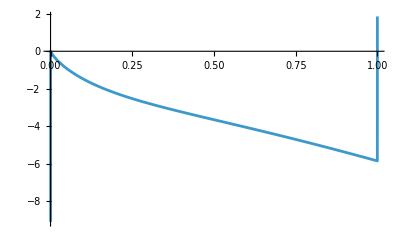

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

-3.53673-5.12531×10^-7 ⅈ

-3.53732

```mathematica
Total[simplifiedTotalIntegrands];
Plot[%//Re,{r,0,1}]
NIntegrate[%%,{r,0.0001,0.9999}]
12/5-(32 π^4)/525//N
```

Mathematica cannot integrate the following integrands

```mathematica
simplifiedTotalIntegrands[[181]]
simplifiedTotalIntegrands[[187]]
simplifiedTotalIntegrands[[195]]
simplifiedTotalIntegrands[[200]]
simplifiedTotalIntegrands[[221]]
```

-(256 Log[1-r] PolyLog[2,1+r])/(35 r)

-(256 Log[r] PolyLog[2,1+r])/(35 (-1+r))

-(128 Log[r] PolyLog[2,1+r])/(35 (1+r))

-(256 Log[1+r] PolyLog[2,1+r])/(35 r)

(256 PolyLog[3,1-r^2])/(35 r)

Thus, we define the remaining part, which Mathematica can integrate automatically.

```mathematica
totalIntegrandsP=Delete[simplifiedTotalIntegrands,{{181},{187},{195},{200},{221}}];
```

We split ∫(Log[1-r] PolyLog[2,1+r])/r ⅆr into two parts: {indefinite integral, definite integral}, computed by hand:

```mathematica
handInt181={-PolyLog[2,r] PolyLog[2,1+r]-1/6 ⅈ π (Log[1-r] (12 ArcTanh[r] Log[r]+π (π-3 ⅈ Log[1-r]+6 ⅈ Log[1+r]))+6 Log[1+r] PolyLog[2,1+r]-6 Log[-1+2/(1+r)] (PolyLog[2,r]-PolyLog[2,(1+r)/(1-r)]+PolyLog[2,(1+r)/(-1+r)])-6 PolyLog[3,1-r]-6 PolyLog[3,1+r]+6 PolyLog[3,(1+r)/(1-r)]-6 PolyLog[3,(1+r)/(-1+r)]),π^4/480};
```

We split ∫(Log[r] PolyLog[2,1+r])/(-1+r)ⅆr into two parts: {indefinite integral, definite integral}, computed by hand:

```mathematica
handInt187={-π^2 (Log[r] Log[1+r]+PolyLog[2,-r])+Log[-1+r] Log[r] PolyLog[2,1+r]+PolyLog[2,r] PolyLog[2,1+r]+ⅈ π (Log[r]^2 Log[1+r]+2 Log[r] PolyLog[2,-r]-2 PolyLog[3,-r])-ⅈ π (Log[-r]^2 Log[1+r]+2 Log[-r] PolyLog[2,-r]+Log[-r] PolyLog[2,1+r]-2 PolyLog[3,-r])+ⅈ π (-1/2 Log[2] Log[-r] (-2 Log[1-r]+Log[-r])+Log[2] Log[-r] Log[(2 r)/(-1+r)]+Log[1-r] Log[r] Log[(1+r)/2]+1/2 Log[(2 r)/(-1+r)]^2 (Log[1/(2-2 r)]+Log[1+r]-Log[(1+r)/(1-r)])+(Log[r]-Log[(2 r)/(-1+r)]) PolyLog[2,(1-r)/2]+(Log[2-2 r]+Log[r/(-1+r)]) PolyLog[2,-r]+Log[(2 r)/(-1+r)] (PolyLog[2,r/(-1+r)]-PolyLog[2,(2 r)/(-1+r)])-PolyLog[3,(1-r)/2]-PolyLog[3,-r]-PolyLog[3,r/(-1+r)]+PolyLog[3,(2 r)/(-1+r)])+1/6 ⅈ π (Log[1-r] (12 ArcTanh[r] Log[r]+π (π-3 ⅈ Log[1-r]+6 ⅈ Log[1+r]))+6 Log[1+r] PolyLog[2,1+r]-6 Log[-1+2/(1+r)] (PolyLog[2,r]-PolyLog[2,(1+r)/(1-r)]+PolyLog[2,(1+r)/(-1+r)])-6 PolyLog[3,1-r]-6 PolyLog[3,1+r]+6 PolyLog[3,(1+r)/(1-r)]-6 PolyLog[3,(1+r)/(-1+r)]),(13 π^4)/1440+1/6 π^2 Log[2]^2-Log[2]^4/6-4 PolyLog[4,1/2]};
```

we can calculate three indefinite integrals ∫(Log[r] PolyLog[2,1+r])/(1+r)ⅆr , ∫(Log[1+r] PolyLog[2,1+r])/r ⅆr , ∫PolyLog[3,1-r^2]/r ⅆr by hand:

```mathematica
handInt195=1/12 (-3 π^4+Log[r] (-20 ⅈ π^3-3 Log[r] (-6 π^2-4 ⅈ π Log[r]+Log[r]^2))+2 (7 ⅈ π^3+Log[r] (-41 π^2+6 Log[r] (ⅈ π+Log[r]))) Log[1+r]+24 (2 π^2-ⅈ π Log[r]-Log[r]^2) Log[1+r]^2+4 (ⅈ π+3 Log[r]) Log[1+r]^3-3 Log[1+r]^4)+(π+ⅈ Log[r/(1+r)])^2 PolyLog[2,1+1/r]+(π+2 ⅈ ArcCoth[1+2 r])^2 PolyLog[2,r/(1+r)]+1/2 PolyLog[2,-r] (PolyLog[2,-r]+2 PolyLog[2,1+r])+2 Log[-(1+r)/r] PolyLog[3,1+1/r]+ⅈ (4 π Log[r/(1+r)] PolyLog[2,1+r]+4 π PolyLog[3,-r]+2 (π+2 ⅈ ArcCoth[1+2 r]) PolyLog[3,r/(1+r)]+3 π PolyLog[3,1+r])-2 PolyLog[4,1+1/r]-2 PolyLog[4,r/(1+r)];
handInt200=-PolyLog[2,-r] PolyLog[2,1+r]+1/12 (-Log[-r]^4-6 Log[-r]^2 Log[-r/(1+r)]^2+4 (Log[-r]+Log[1/(1+r)]) Log[-r/(1+r)]^3-Log[-r/(1+r)]^4-4 Log[-r]^2 (2 Log[-r]-3 Log[1+r]) Log[1+r]-6 Log[-r]^2 Log[1+r]^2+4 Log[-r]^2 Log[-r/(1+r)] (Log[-r]+3 Log[1+r])-12 Log[-r] (Log[-r]-2 Log[-r/(1+r)]) PolyLog[2,-r]+12 Log[-r] Log[1+r] PolyLog[2,-r]-6 PolyLog[2,-r]^2+12 Log[-r/(1+r)]^2 PolyLog[2,r/(1+r)]-12 (Log[-r]-Log[-r/(1+r)])^2 PolyLog[2,1+r]-24 (Log[-r/(1+r)]+Log[1+r]) PolyLog[3,-r]-24 Log[-r/(1+r)] PolyLog[3,r/(1+r)]-24 (-Log[-r]+Log[-r/(1+r)]) PolyLog[3,1+r]+24 (PolyLog[4,-r]+PolyLog[4,r/(1+r)]-PolyLog[4,1+r]));
handInt221=2 ⅈ π Log[(2 r)/(1+r)] PolyLog[2,1+1/r]-2 Log[-1+1/r]^2 PolyLog[2,(-1+r)/r]+(2 Log[1-r]^2+2 Log[r]^2+1/6 π (π-12 ⅈ Log[2 r])) PolyLog[2,r]+2 ⅈ π Log[2/(1+r)] PolyLog[2,(1+r)/2]-1/6 π (π-12 ⅈ Log[1+r]) PolyLog[2,1+r]-2 ⅈ π Log[(2 r)/(1+r)] PolyLog[2,(1+r)/(2 r)]+2 ⅈ π PolyLog[3,1+1/r]+4 Log[1-r] PolyLog[3,1-r]+4 Log[-1+1/r] PolyLog[3,(-1+r)/r]+2 ⅈ (π+2 ⅈ Log[r]) PolyLog[3,r]+2 ⅈ π PolyLog[3,(1+r)/2]-2 ⅈ π PolyLog[3,1+r]-2 (-π^2 (Log[r] Log[1+r]+PolyLog[2,-r])+Log[-1+r] Log[r] PolyLog[2,1+r]+PolyLog[2,r] PolyLog[2,1+r]+ⅈ π (Log[r]^2 Log[1+r]+2 Log[r] PolyLog[2,-r]-2 PolyLog[3,-r])-ⅈ π (Log[-r]^2 Log[1+r]+2 Log[-r] PolyLog[2,-r]+Log[-r] PolyLog[2,1+r]-2 PolyLog[3,-r])+ⅈ π (-1/2 Log[2] Log[-r] (-2 Log[1-r]+Log[-r])+Log[2] Log[-r] Log[(2 r)/(-1+r)]+Log[1-r] Log[r] Log[(1+r)/2]+1/2 Log[(2 r)/(-1+r)]^2 (Log[1/(2-2 r)]+Log[1+r]-Log[(1+r)/(1-r)])+(Log[r]-Log[(2 r)/(-1+r)]) PolyLog[2,(1-r)/2]+(Log[2-2 r]+Log[r/(-1+r)]) PolyLog[2,-r]+Log[(2 r)/(-1+r)] (PolyLog[2,r/(-1+r)]-PolyLog[2,(2 r)/(-1+r)])-PolyLog[3,(1-r)/2]-PolyLog[3,-r]-PolyLog[3,r/(-1+r)]+PolyLog[3,(2 r)/(-1+r)])+1/6 ⅈ π (Log[1-r] (12 ArcTanh[r] Log[r]+π (π-3 ⅈ Log[1-r]+6 ⅈ Log[1+r]))+6 Log[1+r] PolyLog[2,1+r]-6 Log[-1+2/(1+r)] (PolyLog[2,r]-PolyLog[2,(1+r)/(1-r)]+PolyLog[2,(1+r)/(-1+r)])-6 PolyLog[3,1-r]-6 PolyLog[3,1+r]+6 PolyLog[3,(1+r)/(1-r)]-6 PolyLog[3,(1+r)/(-1+r)]))-2 ⅈ π PolyLog[3,(1+r)/(2 r)]+Log[r] PolyLog[3,1-r^2]-4 PolyLog[4,1-r]-4 PolyLog[4,(-1+r)/r]+2 (-PolyLog[2,1-r] PolyLog[2,r]+1/12 (-Log[-1+1/r]^4-6 Log[-1+1/r]^2 Log[1-r]^2-Log[1-r]^4+4 Log[-1+1/r]^3 (Log[1-r]+Log[1/r])-4 Log[1-r]^2 (2 Log[1-r]-3 Log[r]) Log[r]-6 Log[1-r]^2 Log[r]^2+4 Log[-1+1/r] Log[1-r]^2 (Log[1-r]+3 Log[r])-12 Log[1-r] (-2 Log[-1+1/r]+Log[1-r]-2 Log[r]) PolyLog[2,1-r]-12 Log[1-r] Log[r] PolyLog[2,1-r]-6 PolyLog[2,1-r]^2+12 Log[-1+1/r]^2 PolyLog[2,(-1+r)/r]-12 (Log[-1+1/r]-Log[1-r])^2 PolyLog[2,r]-24 (Log[-1+1/r]+Log[r]) PolyLog[3,1-r]-24 Log[-1+1/r] PolyLog[3,(-1+r)/r]-24 (Log[-1+1/r]-Log[1-r]) PolyLog[3,r]+24 (PolyLog[4,1-r]+PolyLog[4,(-1+r)/r]-PolyLog[4,r])))+1/6 (12 Log[1-r]^3 Log[r]-2 Log[1-r]^2 (π^2+3 Log[r]^2)+Log[1-r] Log[r] (π^2+12 Log[r]^2)-3 Log[r] (4 ⅈ π Log[2]^2+2 ⅈ π Log[2] Log[r]+Log[r]^3)-ⅈ π (π^2-12 Log[-2/(-1+r)] Log[r]) Log[1+r]-6 π^2 Log[1+r]^2+24 PolyLog[4,r])-2 (1/12 (-3 π^4+Log[r] (-20 ⅈ π^3-3 Log[r] (-6 π^2-4 ⅈ π Log[r]+Log[r]^2))+2 (7 ⅈ π^3+Log[r] (-41 π^2+6 Log[r] (ⅈ π+Log[r]))) Log[1+r]+24 (2 π^2-ⅈ π Log[r]-Log[r]^2) Log[1+r]^2+4 (ⅈ π+3 Log[r]) Log[1+r]^3-3 Log[1+r]^4)+(π+ⅈ Log[r/(1+r)])^2 PolyLog[2,1+1/r]+(π+2 ⅈ ArcCoth[1+2 r])^2 PolyLog[2,r/(1+r)]+1/2 PolyLog[2,-r] (PolyLog[2,-r]+2 PolyLog[2,1+r])+2 Log[-(1+r)/r] PolyLog[3,1+1/r]+ⅈ (4 π Log[r/(1+r)] PolyLog[2,1+r]+4 π PolyLog[3,-r]+2 (π+2 ⅈ ArcCoth[1+2 r]) PolyLog[3,r/(1+r)]+3 π PolyLog[3,1+r])-2 PolyLog[4,1+1/r]-2 PolyLog[4,r/(1+r)]);
```

r - integration

```mathematica
Total[Integrate[totalIntegrandsP,r]]-256/35 handInt181[[1]]-256/35 handInt187[[1]] -128/35 handInt195-256/35 handInt200+256/35 handInt221//Expand;
indefiniteIntResult=Apart[%//Simplify,r]
definiteIntResult=-256/35 handInt181[[2]]-256/35 handInt187[[2]]
```

-9101/7560+(32 π^4)/7+256/35 HarmonicPolyLog[{-3,1},r]+256/35 ⅈ π HarmonicPolyLog[{-2,1},r]+128/35 HarmonicPolyLog[{2,-1},r]-128/35 HarmonicPolyLog[{2,2},r]+768/35 HarmonicPolyLog[{3,-1},r]-128/105 Log[-1+1/r]^4+158/105 Log[1-r]+16/315 ⅈ π Log[1-r]-256/105 ⅈ π^3 Log[1-r]+2 ⅈ π Log[2] Log[1-r]-ⅈ π Log[4] Log[1-r]+512/105 Log[-1+1/r]^3 Log[1-r]+128/35 Log[1-r]^2-1024/105 π^2 Log[1-r]^2-256/35 Log[-1+1/r]^2 Log[1-r]^2+512/105 Log[-1+1/r] Log[1-r]^3-128/105 Log[1-r]^4-64/105 ⅈ (ⅈ π^2+π^3+2 ⅈ π^2 Log[1-r])+64/105 ⅈ (2 ⅈ π^2+π^3+2 ⅈ π^2 Log[1-r])-38/35 Log[-1+r]+512/105 Log[-1+1/r]^3 Log[1/r]-(1269 Log[-r])/140+32/35 Log[2] Log[4] Log[-r]-8/35 Log[4] Log[16] Log[-r]+2288/315 Log[1-r] Log[-r]+221/105 Log[2] Log[1-r] Log[-r]-768/35 ⅈ π Log[2] Log[1-r] Log[-r]+326/105 Log[4] Log[1-r] Log[-r]+128/35 Log[2] Log[-1+r] Log[-r]-69/140 Log[-r]^2-89/15 Log[2] Log[-r]^2+384/35 ⅈ π Log[2] Log[-r]^2-11/630 Log[8] Log[-r]^2-23/420 Log[-r]^3+64/105 Log[-r]^4+(661 Log[r])/60+69/70 ⅈ π Log[r]+73/30 π^2 Log[r]+448/15 ⅈ π^3 Log[r]+256/35 HarmonicPolyLog[{-1,2},r] Log[r]-128/35 HarmonicPolyLog[{1,2},r] Log[r]-512/35 HarmonicPolyLog[{2,-1},r] Log[r]-64/35 Log[2]^2 Log[r]-384/35 ⅈ π Log[2]^2 Log[r]-(3161 Log[1-r] Log[r])/1260+256/105 π^2 Log[1-r] Log[r]-1024/35 ⅈ π ArcTanh[r] Log[1-r] Log[r]+128/35 Log[2] Log[1-r] Log[r]-256/35 ⅈ π Log[2] Log[1-r] Log[r]+512/35 Log[-1+1/r] Log[1-r]^2 Log[r]+512/105 Log[1-r]^3 Log[r]-128/35 Log[-r] Log[r]-128/35 Log[1-r] Log[-r] Log[r]+23/140 Log[-r]^2 Log[r]+(289 Log[r]^2)/140-23/140 ⅈ π Log[r]^2-3008/105 π^2 Log[r]^2-256/35 ⅈ π Log[2] Log[r]^2+128/35 Log[2]^2 Log[r]^2+103/21 Log[1-r] Log[r]^2-256/35 Log[2] Log[1-r] Log[r]^2+256/35 Log[1-r]^2 Log[r]^2-(23 Log[r]^3)/210-128/7 ⅈ π Log[r]^3+512/35 Log[1-r] Log[r]^3+(32 Log[r]^4)/35+419/35 Log[2] Log[-r] Log[(2 r)/(-1+r)]-768/35 ⅈ π Log[2] Log[-r] Log[(2 r)/(-1+r)]+419/70 Log[1/(2-2 r)] Log[(2 r)/(-1+r)]^2-384/35 ⅈ π Log[1/(2-2 r)] Log[(2 r)/(-1+r)]^2-1/2 Log[1/(1-r)] Log[(2 r)/(-1+r)]^2+16/35 Log[-r^2]-128/35 Log[1-r] Log[r] Log[r^2]-256/105 Log[-r]^3 Log[-r/(1+r)]+128/35 Log[-r]^2 Log[-r/(1+r)]^2-256/105 Log[-r] Log[-r/(1+r)]^3-256/105 Log[1/(1+r)] Log[-r/(1+r)]^3+64/105 Log[-r/(1+r)]^4+291/35 Log[1-r] Log[-r] Log[(1+r)/2]-1/2 Log[-r]^2 Log[(1+r)/2]-768/35 ⅈ π Log[1-r] Log[r] Log[(1+r)/2]+128/35 Log[-1+r] Log[r] Log[(1+r)/2]+Log[-r] Log[(2 r)/(-1+r)] Log[(1+r)/2]-1/2 Log[(2 r)/(-1+r)]^2 Log[(1+r)/2]-66/7 Log[r] (Log[r]-2 Log[1+r])+368/105 Log[1+r]-1168/315 ⅈ π Log[1+r]-2368/105 ⅈ π^3 Log[1+r]+256/35 Log[1-r] Log[1+r]+512/35 π^2 Log[1-r] Log[1+r]-128/35 Log[-r] Log[1+r]-Log[1-r] Log[-r] Log[1+r]-3107/210 Log[-r]^2 Log[1+r]+768/35 ⅈ π Log[-r]^2 Log[1+r]+128/105 Log[-r]^3 Log[1+r]-1744/315 Log[r] Log[1+r]-74/105 ⅈ π Log[r] Log[1+r]+15488/105 π^2 Log[r] Log[1+r]+512/35 ⅈ π Log[-2/(-1+r)] Log[r] Log[1+r]-128/35 Log[-1+r] Log[r] Log[1+r]+256/35 Log[-r]^2 Log[r] Log[1+r]+162/35 Log[r]^2 Log[1+r]-1408/35 ⅈ π Log[r]^2 Log[1+r]+128/35 Log[1-r] Log[r]^2 Log[1+r]-128/7 Log[r]^3 Log[1+r]-Log[-r] Log[(2 r)/(-1+r)] Log[1+r]+419/70 Log[(2 r)/(-1+r)]^2 Log[1+r]-384/35 ⅈ π Log[(2 r)/(-1+r)]^2 Log[1+r]-128/35 Log[r] Log[r^2] Log[1+r]-256/35 Log[-r]^2 Log[-r/(1+r)] Log[1+r]+128/35 Log[1+r]^2-2816/35 π^2 Log[1+r]^2-64/35 Log[-r] Log[1+r]^2-256/35 ⅈ π Log[-r] Log[1+r]^2-128/35 Log[-r]^2 Log[1+r]^2-64/35 Log[r] Log[1+r]^2+1216/35 ⅈ π Log[r] Log[1+r]^2+128/35 Log[-r] Log[r] Log[1+r]^2+1216/35 Log[r]^2 Log[1+r]^2-128/21 ⅈ π Log[1+r]^3-128/7 Log[r] Log[1+r]^3+32/7 Log[1+r]^4-64/105 (π^2+π^2 Log[r]-π^2 Log[1+r])+64/105 (2 π^2+π^2 Log[r]-π^2 Log[1+r])-192/35 Log[(2 r)/(-1+r)]^2 Log[(1+r)/(1-r)]+384/35 ⅈ π Log[(2 r)/(-1+r)]^2 Log[(1+r)/(1-r)]+128/35 Log[r] Log[1+r] Log[1-r^2]-64/35 Log[r] Log[1-r^2]^2+32/35 Log[r^2] Log[1-r^2]^2-128/7 π^2 PolyLog[2,1+1/r]-256/7 ⅈ π Log[r/(1+r)] PolyLog[2,1+1/r]+128/7 Log[r/(1+r)]^2 PolyLog[2,1+1/r]+512/35 ⅈ π Log[(2 r)/(1+r)] PolyLog[2,1+1/r]+256/35 Log[-r] PolyLog[2,(1-r)/2]-512/35 ⅈ π Log[r] PolyLog[2,(1-r)/2]+256/35 Log[r]^2 PolyLog[2,(1-r)/2]-384/35 Log[(2 r)/(-1+r)] PolyLog[2,(1-r)/2]+768/35 ⅈ π Log[(2 r)/(-1+r)] PolyLog[2,(1-r)/2]-67/420 PolyLog[2,1-r]+1024/35 Log[-1+1/r] Log[1-r] PolyLog[2,1-r]-512/35 Log[1-r]^2 PolyLog[2,1-r]-3/7 Log[r] PolyLog[2,1-r]+1024/35 Log[1-r] Log[r] PolyLog[2,1-r]+128/35 Log[1+r] PolyLog[2,1-r]-128/35 Log[1-r^2] PolyLog[2,1-r]-64/7 PolyLog[2,1-r]^2-592/315 PolyLog[2,-r]+184/35 ⅈ π PolyLog[2,-r]+768/35 π^2 PolyLog[2,-r]+256/35 Log[2-2 r] PolyLog[2,-r]-768/35 ⅈ π Log[2-2 r] PolyLog[2,-r]-418/15 Log[-r] PolyLog[2,-r]+1536/35 ⅈ π Log[-r] PolyLog[2,-r]+128/35 Log[-r]^2 PolyLog[2,-r]+2158/105 Log[r] PolyLog[2,-r]-256/5 ⅈ π Log[r] PolyLog[2,-r]+512/35 Log[-r] Log[r] PolyLog[2,-r]-128/35 Log[r]^2 PolyLog[2,-r]+256/35 Log[r/(-1+r)] PolyLog[2,-r]-768/35 ⅈ π Log[r/(-1+r)] PolyLog[2,-r]+128/35 Log[(2 r)/(-1+r)] PolyLog[2,-r]-128/35 Log[r^2] PolyLog[2,-r]-512/35 Log[-r] Log[-r/(1+r)] PolyLog[2,-r]-128/35 Log[1+r] PolyLog[2,-r]-256/35 Log[-r] Log[1+r] PolyLog[2,-r]+128/35 Log[1-r^2] PolyLog[2,-r]-192/35 PolyLog[2,-r]^2-4/7 (17 Log[r] Log[1+r]+PolyLog[2,-r])+701/420 PolyLog[2,r]-286/105 ⅈ π PolyLog[2,r]+64/35 π^2 PolyLog[2,r]-512/35 Log[-1+1/r]^2 PolyLog[2,r]+1024/35 Log[-1+1/r] Log[1-r] PolyLog[2,r]-14/15 Log[-r] PolyLog[2,r]+193/21 Log[r] PolyLog[2,r]+128/7 Log[r]^2 PolyLog[2,r]-512/35 ⅈ π Log[2 r] PolyLog[2,r]-128/35 Log[r^2] PolyLog[2,r]+512/35 ⅈ π Log[-1+2/(1+r)] PolyLog[2,r]-512/35 PolyLog[2,1-r] PolyLog[2,r]+384/35 Log[(2 r)/(-1+r)] PolyLog[2,r/(-1+r)]-768/35 ⅈ π Log[(2 r)/(-1+r)] PolyLog[2,r/(-1+r)]-384/35 Log[(2 r)/(-1+r)] PolyLog[2,(2 r)/(-1+r)]+768/35 ⅈ π Log[(2 r)/(-1+r)] PolyLog[2,(2 r)/(-1+r)]-128/7 π^2 PolyLog[2,r/(1+r)]-512/7 ⅈ π ArcCoth[1+2 r] PolyLog[2,r/(1+r)]+512/7 ArcCoth[1+2 r]^2 PolyLog[2,r/(1+r)]-256/35 Log[-r/(1+r)]^2 PolyLog[2,r/(1+r)]+512/35 ⅈ π Log[2/(1+r)] PolyLog[2,(1+r)/2]-1168/315 PolyLog[2,1+r]-128/105 π^2 PolyLog[2,1+r]+256/35 Log[1-r] PolyLog[2,1+r]-1606/105 Log[-r] PolyLog[2,1+r]+768/35 ⅈ π Log[-r] PolyLog[2,1+r]+128/35 Log[-r]^2 PolyLog[2,1+r]+62/21 Log[r] PolyLog[2,1+r]-768/35 Log[-1+r] Log[r] PolyLog[2,1+r]+256/35 Log[-r] Log[r] PolyLog[2,1+r]-512/35 Log[-r] Log[-r/(1+r)] PolyLog[2,1+r]+256/35 Log[-r/(1+r)]^2 PolyLog[2,1+r]-512/7 ⅈ π Log[r/(1+r)] PolyLog[2,1+r]-128/35 Log[1+r] PolyLog[2,1+r]-512/35 ⅈ π Log[1+r] PolyLog[2,1+r]+256/35 Log[r] Log[1+r] PolyLog[2,1+r]-384/35 PolyLog[2,-r] PolyLog[2,1+r]-512/35 PolyLog[2,r] PolyLog[2,1+r]-64/35 PolyLog[2,1+r]^2+1/(105 (-1+r)^2)2 (64 π^2 Log[r]-111 Log[r]^2-384 ⅈ π Log[r] Log[1+r]-192 Log[r]^2 Log[1+r]+192 Log[r] PolyLog[2,r]-384 Log[r] PolyLog[2,1+r])+1/(105 (-1+r))2 (-64 π^2+384 Log[2] Log[1-r] Log[-r]-96 Log[16] Log[1-r] Log[-r]+135 Log[r]-192 ⅈ π Log[r]+64 π^2 Log[r]+192 Log[1-r] Log[r]+192 Log[-r] Log[r]-399 Log[r]^2+384 ⅈ π Log[1+r]+384 Log[r] Log[1+r]-384 ⅈ π Log[r] Log[1+r]-192 Log[r]^2 Log[1+r]-192 PolyLog[2,r]+192 Log[r] PolyLog[2,r]+384 PolyLog[2,1+r]-384 Log[r] PolyLog[2,1+r])+1/(105 (1+r)^2)2 (-96 ⅈ π Log[r]+32 π^2 Log[r]+96 Log[-r] Log[r]-207 Log[r]^2+192 Log[1-r] Log[r]^2-192 ⅈ π Log[r] Log[1+r]-192 Log[r]^2 Log[1+r]+384 Log[r] PolyLog[2,r]-192 Log[r] PolyLog[2,1+r])-1/(105 (1+r))2 (96 ⅈ π-32 π^2-96 Log[-r]+231 Log[r]-192 ⅈ π Log[r]+32 π^2 Log[r]+192 Log[-r] Log[r]-399 Log[r]^2+192 Log[1-r] Log[r]^2+192 ⅈ π Log[1+r]+384 Log[r] Log[1+r]-192 ⅈ π Log[r] Log[1+r]-192 Log[r]^2 Log[1+r]-384 PolyLog[2,r]+384 Log[r] PolyLog[2,r]+192 PolyLog[2,1+r]-192 Log[r] PolyLog[2,1+r])-512/35 ⅈ π Log[-1+2/(1+r)] PolyLog[2,(1+r)/(1-r)]+512/35 ⅈ π Log[-1+2/(1+r)] PolyLog[2,(1+r)/(-1+r)]-512/35 ⅈ π Log[(2 r)/(1+r)] PolyLog[2,(1+r)/(2 r)]+64/35 PolyLog[2,1-r^2]-128/35 Log[r] PolyLog[2,1-r^2]+64/35 Log[1-r^2] PolyLog[2,1-r^2]+512/35 ⅈ π PolyLog[3,1+1/r]-256/7 Log[-(1+r)/r] PolyLog[3,1+1/r]-384/35 PolyLog[3,(1-r)/2]+768/35 ⅈ π PolyLog[3,(1-r)/2]+128/35 PolyLog[3,1-r]+512/35 ⅈ π PolyLog[3,1-r]-1024/35 Log[-1+1/r] PolyLog[3,1-r]+1024/35 Log[1-r] PolyLog[3,1-r]-1664/35 Log[r] PolyLog[3,1-r]+128/35 PolyLog[3,-r]-1536/35 ⅈ π PolyLog[3,-r]-256/35 Log[-r] PolyLog[3,-r]-256/35 Log[r] PolyLog[3,-r]+512/35 Log[-r/(1+r)] PolyLog[3,-r]+512/35 Log[1+r] PolyLog[3,-r]+256/35 PolyLog[3,r]+512/35 ⅈ π PolyLog[3,r]-1024/35 Log[-1+1/r] PolyLog[3,r]+1024/35 Log[1-r] PolyLog[3,r]-1536/35 Log[r] PolyLog[3,r]-384/35 PolyLog[3,r/(-1+r)]+768/35 ⅈ π PolyLog[3,r/(-1+r)]+384/35 PolyLog[3,(2 r)/(-1+r)]-768/35 ⅈ π PolyLog[3,(2 r)/(-1+r)]-256/7 ⅈ π PolyLog[3,r/(1+r)]+512/7 ArcCoth[1+2 r] PolyLog[3,r/(1+r)]+512/35 Log[-r/(1+r)] PolyLog[3,r/(1+r)]+512/35 ⅈ π PolyLog[3,(1+r)/2]+256/35 PolyLog[3,1+r]-1408/35 ⅈ π PolyLog[3,1+r]-128/7 Log[-r] PolyLog[3,1+r]-256/35 Log[r] PolyLog[3,1+r]+512/35 Log[-r/(1+r)] PolyLog[3,1+r]-512/35 ⅈ π PolyLog[3,(1+r)/(1-r)]+512/35 ⅈ π PolyLog[3,(1+r)/(-1+r)]-512/35 ⅈ π PolyLog[3,(1+r)/(2 r)]-64/35 PolyLog[3,1-r^2]+256/35 Log[r] PolyLog[3,1-r^2]+256/7 PolyLog[4,1+1/r]+512/35 PolyLog[4,r]+32/35 PolyLog[4,r^2]+768/35 PolyLog[4,r/(1+r)]+512/35 PolyLog[4,1+r]-256/35 PolyLog[2,2,-r]-1024/35 PolyLog[2,2,r]+2/35 (64 HarmonicPolyLog[{1,2},r]+128 HarmonicPolyLog[{2,-1},r]+128 Log[2]^2-64 ⅈ π Log[2]^2-128 Log[1-r]-128 ⅈ π Log[1-r]-256 Log[2] Log[1-r]+128 ⅈ π Log[2] Log[1-r]-128 Log[1-r]^2+32 π^2 Log[r]-64 Log[2]^2 Log[r]+74 Log[1-r] Log[r]+64 ⅈ π Log[1-r] Log[r]+128 Log[2] Log[1-r] Log[r]-101 Log[r]^2+32 Log[1-r] Log[r]^2+128 ⅈ π Log[1+r]+128 Log[r] Log[1+r]-64 ⅈ π Log[r] Log[1+r]-32 Log[r]^2 Log[1+r]+256 PolyLog[2,(1-r)/2]-128 ⅈ π PolyLog[2,(1-r)/2]-128 Log[r] PolyLog[2,(1-r)/2]-64 Log[1-r] PolyLog[2,1-r]-128 PolyLog[2,-r]+64 ⅈ π PolyLog[2,-r]+64 Log[r] PolyLog[2,-r]+64 ⅈ π PolyLog[2,r]+128 Log[r] PolyLog[2,r]+128 PolyLog[2,1+r]-128 Log[r] PolyLog[2,1+r]+64 PolyLog[3,1-r]-64 PolyLog[3,-r]-64 PolyLog[3,r]-64 Zeta[3])-2/35 (64 HarmonicPolyLog[{1,2},r]+128 HarmonicPolyLog[{2,-1},r]+64 Log[2]^2-64 ⅈ π Log[2]^2-64 Log[1-r]-128 ⅈ π Log[1-r]-128 Log[2] Log[1-r]+128 ⅈ π Log[2] Log[1-r]-64 Log[1-r]^2+128 Log[1-r] Log[-r]+32 Log[16] Log[1-r] Log[-r]-64 Log[-r]^2-32 Log[4] Log[-r]^2+138 Log[r]+64 ⅈ π Log[r]+32 π^2 Log[r]-64 Log[2]^2 Log[r]-64 Log[1-r] Log[r]+32 ⅈ π Log[1-r] Log[r]+128 Log[2] Log[1-r] Log[r]+64 Log[-r] Log[r]-32 Log[1-r] Log[-r] Log[r]-69 Log[r]^2+16 Log[1-r] Log[r]^2+128 Log[2] Log[-r] Log[(2 r)/(-1+r)]+64 Log[1/(2-2 r)] Log[(2 r)/(-1+r)]^2+128 Log[1-r] Log[-r] Log[(1+r)/2]+64 ⅈ π Log[1+r]-96 Log[-r]^2 Log[1+r]+64 Log[r] Log[1+r]-32 ⅈ π Log[r] Log[1+r]-16 Log[r]^2 Log[1+r]+64 Log[(2 r)/(-1+r)]^2 Log[1+r]-64 Log[(2 r)/(-1+r)]^2 Log[(1+r)/(1-r)]+128 PolyLog[2,(1-r)/2]-128 ⅈ π PolyLog[2,(1-r)/2]+128 Log[-r] PolyLog[2,(1-r)/2]-128 Log[r] PolyLog[2,(1-r)/2]-128 Log[(2 r)/(-1+r)] PolyLog[2,(1-r)/2]-64 Log[1-r] PolyLog[2,1-r]-64 PolyLog[2,-r]+96 ⅈ π PolyLog[2,-r]+128 Log[2-2 r] PolyLog[2,-r]-192 Log[-r] PolyLog[2,-r]+96 Log[r] PolyLog[2,-r]+128 Log[r/(-1+r)] PolyLog[2,-r]-64 PolyLog[2,r]+32 ⅈ π PolyLog[2,r]-32 Log[-r] PolyLog[2,r]+64 Log[r] PolyLog[2,r]+128 Log[(2 r)/(-1+r)] PolyLog[2,r/(-1+r)]-128 Log[(2 r)/(-1+r)] PolyLog[2,(2 r)/(-1+r)]+64 PolyLog[2,1+r]+128 Log[1-r] PolyLog[2,1+r]-96 Log[-r] PolyLog[2,1+r]-32 Log[r] PolyLog[2,1+r]-128 PolyLog[3,(1-r)/2]+64 PolyLog[3,1-r]-32 PolyLog[3,-r]+32 PolyLog[3,r]-128 PolyLog[3,r/(-1+r)]+128 PolyLog[3,(2 r)/(-1+r)]-64 Zeta[3])+r^2 (-11/35-(671 ⅈ π)/280-(181 π^2)/840+64/35 HarmonicPolyLog[{-2,1},r]+64/35 HarmonicPolyLog[{-1,2},r]-64/35 HarmonicPolyLog[{1,2},r]+64/35 HarmonicPolyLog[{2,-1},r]+26/105 Log[1-r]+181/210 ⅈ π Log[1-r]+16/105 π^2 Log[1-r]+(671 Log[-r])/280-181/210 Log[1-r] Log[-r]+(1147 Log[r])/840+29/60 ⅈ π Log[r]+16/105 π^2 Log[r]-971/420 Log[1-r] Log[r]-29/60 Log[-r] Log[r]+(247 Log[r]^2)/420-(64 Log[r^2])/35+26/105 Log[1+r]+362/105 ⅈ π Log[1+r]+16/105 π^2 Log[1+r]-64/35 ⅈ π Log[1-r] Log[1+r]-181/210 Log[-r] Log[1+r]-11/42 Log[r] Log[1+r]-32/35 ⅈ π Log[r] Log[1+r]+64/35 Log[1-r] Log[r] Log[1+r]-32/35 Log[r]^2 Log[1+r]-16/7 ⅈ π Log[1+r]^2-16/35 Log[1-r^2]+15/28 PolyLog[2,1-r]-128/35 Log[1-r] PolyLog[2,1-r]-41/20 PolyLog[2,r]+32/35 Log[r] PolyLog[2,r]-16/35 PolyLog[2,r^2]+181/70 PolyLog[2,1+r]-64/35 Log[1-r] PolyLog[2,1+r]-32/35 Log[r] PolyLog[2,1+r]-64/35 Log[1+r] PolyLog[2,1+r]-64/35 PolyLog[2,1-r^2]+96/35 PolyLog[3,1-r]+16/35 PolyLog[3,r^2]-32/35 PolyLog[3,1+r]+64/35 PolyLog[3,1-r^2]-(128 Zeta[3])/35)+r ((1667 ⅈ π)/315-(127 π^2)/630+HarmonicPolyLog[{-2,1},r]+HarmonicPolyLog[{-1,2},r]-HarmonicPolyLog[{1,2},r]+HarmonicPolyLog[{2,-1},r]-286/105 ⅈ π Log[1-r]-5/12 π^2 Log[1-r]-(1667 Log[-r])/315+286/105 Log[1-r] Log[-r]+(1667 Log[r])/315+31/30 ⅈ π Log[r]+1/3 π^2 Log[r]-53/35 Log[1-r] Log[r]-31/30 Log[-r] Log[r]+(31 Log[r]^2)/30-2 Log[1-r] Log[r]^2-38/35 ⅈ π Log[1+r]+1/12 π^2 Log[1+r]+ⅈ π Log[1-r] Log[1+r]+286/105 Log[-r] Log[1+r]-286/105 Log[r] Log[1+r]-2 ⅈ π Log[r] Log[1+r]+Log[1-r] Log[r] Log[1+r]+1/4 ⅈ π Log[1+r]^2-3/7 PolyLog[2,1-r]-2 Log[1-r] PolyLog[2,1-r]+127/105 PolyLog[2,r]-2 Log[r] PolyLog[2,r]+172/105 PolyLog[2,1+r]+Log[1-r] PolyLog[2,1+r]-2 Log[r] PolyLog[2,1+r]+Log[1+r] PolyLog[2,1+r]+7/2 PolyLog[3,1-r]-3/2 PolyLog[3,1+r]-2 Zeta[3])+r^3 (-(11 ⅈ π)/630-(11 π^2)/1260-11/105 HarmonicPolyLog[{-2,1},r]-11/105 HarmonicPolyLog[{-1,2},r]+11/105 HarmonicPolyLog[{1,2},r]-11/105 HarmonicPolyLog[{2,-1},r]+11/315 ⅈ π Log[1-r]+11/252 π^2 Log[1-r]+(11 Log[-r])/630-11/315 Log[1-r] Log[-r]-(11 Log[r])/630-11/630 ⅈ π Log[r]-(11 π^2 Log[r])/1260+11/126 Log[1-r] Log[r]+11/630 Log[-r] Log[r]-(11 Log[r]^2)/630+11/210 Log[1-r] Log[r]^2+11/315 ⅈ π Log[1+r]-(11 π^2 Log[1+r])/1260-11/105 ⅈ π Log[1-r] Log[1+r]-11/315 Log[-r] Log[1+r]+11/315 Log[r] Log[1+r]+11/210 ⅈ π Log[r] Log[1+r]-11/105 Log[1-r] Log[r] Log[1+r]-11/420 ⅈ π Log[1+r]^2+11/210 PolyLog[2,1-r]+22/105 Log[1-r] PolyLog[2,1-r]+11/210 PolyLog[2,r]+11/210 Log[r] PolyLog[2,r]-11/105 Log[1-r] PolyLog[2,1+r]+11/210 Log[r] PolyLog[2,1+r]-11/105 Log[1+r] PolyLog[2,1+r]-11/30 PolyLog[3,1-r]+11/70 PolyLog[3,1+r]+(22 Zeta[3])/105)-2 Zeta[3]+768/35 Log[r] Zeta[3]-1/(1260 r^3)11 (-12 HarmonicPolyLog[{-2,1},r]-12 HarmonicPolyLog[{-1,2},r]+12 HarmonicPolyLog[{1,2},r]-12 HarmonicPolyLog[{2,-1},r]+5 π^2 Log[1-r]-π^2 Log[1+r]-12 ⅈ π Log[1-r] Log[1+r]-12 Log[1-r] Log[r] Log[1+r]-3 ⅈ π Log[1+r]^2+24 Log[1-r] PolyLog[2,1-r]-12 Log[1-r] PolyLog[2,1+r]-12 Log[1+r] PolyLog[2,1+r]-42 PolyLog[3,1-r]+18 PolyLog[3,1+r]+24 Zeta[3])+2/35 (-32+128 HarmonicPolyLog[{-1,2},r]+64 Log[2]^2-128 Log[2] Log[1-r]+96 Log[-r]-32 Log[-r]^2-234 Log[r]+32 ⅈ π Log[r]+32 Log[-r] Log[r]+69 Log[r]^2-16 Log[1-r] Log[r]^2+138 Log[1+r]-32 ⅈ π Log[1+r]+128 Log[1-r] Log[1+r]+32 Log[-r] Log[1+r]+64 Log[-r]^2 Log[1+r]+16 Log[r]^2 Log[1+r]+64 Log[1+r]^2-32 ⅈ π Log[1+r]^2+64 Log[-r] Log[1+r]^2-64 Log[r] Log[1+r]^2+128 PolyLog[2,(1-r)/2]-64 ⅈ π PolyLog[2,-r]+128 Log[-r] PolyLog[2,-r]-96 Log[r] PolyLog[2,-r]+128 PolyLog[2,r]-32 Log[r] PolyLog[2,r]+64 Log[-r] PolyLog[2,1+r]+128 Log[1+r] PolyLog[2,1+r]-32 PolyLog[3,-r]-96 PolyLog[3,r]-192 PolyLog[3,1+r]+128 Zeta[3])-2/35 (128 HarmonicPolyLog[{-1,2},r]+128 Log[2]^2-256 Log[2] Log[1-r]-64 Log[-r]^2-311 Log[r]+64 ⅈ π Log[r]-32 Log[1-r] Log[r]^2+256 Log[1+r]-64 ⅈ π Log[1+r]+256 Log[1-r] Log[1+r]+32 Log[r]^2 Log[1+r]+128 Log[1+r]^2-32 ⅈ π Log[1+r]^2+64 Log[-r] Log[1+r]^2-64 Log[r] Log[1+r]^2+256 PolyLog[2,(1-r)/2]-74 PolyLog[2,-r]-64 ⅈ π PolyLog[2,-r]-64 Log[r] PolyLog[2,-r]+256 PolyLog[2,r]-64 Log[r] PolyLog[2,r]+128 Log[1+r] PolyLog[2,1+r]+64 PolyLog[3,-r]-64 PolyLog[3,r]-128 PolyLog[3,1+r]+128 Zeta[3])+1/(1260 r)(-3258 ⅈ π+569 π^2-1260 HarmonicPolyLog[{-2,1},r]-1260 HarmonicPolyLog[{-1,2},r]+1260 HarmonicPolyLog[{1,2},r]-1260 HarmonicPolyLog[{2,-1},r]+2172 ⅈ π Log[1-r]+525 π^2 Log[1-r]+3258 Log[-r]-2172 Log[1-r] Log[-r]-3258 Log[r]-2304 ⅈ π Log[r]+315 π^2 Log[r]-1242 Log[1-r] Log[r]+2304 Log[-r] Log[r]-2304 Log[r]^2-1890 Log[1-r] Log[r]^2+108 ⅈ π Log[1+r]-105 π^2 Log[1+r]-1260 ⅈ π Log[1-r] Log[1+r]-2172 Log[-r] Log[1+r]+2172 Log[r] Log[1+r]-1890 ⅈ π Log[r] Log[1+r]-1260 Log[1-r] Log[r] Log[1+r]-315 ⅈ π Log[1+r]^2-1350 PolyLog[2,1-r]+2520 Log[1-r] PolyLog[2,1-r]-3414 PolyLog[2,r]-1890 Log[r] PolyLog[2,r]-2064 PolyLog[2,1+r]-1260 Log[1-r] PolyLog[2,1+r]-1890 Log[r] PolyLog[2,1+r]-1260 Log[1+r] PolyLog[2,1+r]-4410 PolyLog[3,1-r]+1890 PolyLog[3,1+r]+2520 Zeta[3])+1/(840 r^2)(117 π^2-1536 HarmonicPolyLog[{-2,1},r]-1536 HarmonicPolyLog[{-1,2},r]+1536 HarmonicPolyLog[{1,2},r]-1536 HarmonicPolyLog[{2,-1},r]-560 Log[1-r]+44 ⅈ π Log[1-r]-128 π^2 Log[1-r]-44 Log[1-r] Log[-r]+256 π^2 Log[r]+22 Log[1-r] Log[r]+768 Log[1-r] Log[r]^2-560 Log[1+r]-592 ⅈ π Log[1+r]-128 π^2 Log[1+r]+1536 ⅈ π Log[1-r] Log[1+r]-44 Log[-r] Log[1+r]-548 Log[r] Log[1+r]-1536 ⅈ π Log[r] Log[1+r]-1536 Log[1-r] Log[r] Log[1+r]-768 Log[r]^2 Log[1+r]+1920 ⅈ π Log[1+r]^2+384 Log[1-r^2]-66 PolyLog[2,1-r]+3072 Log[1-r] PolyLog[2,1-r]+570 PolyLog[2,r]+1536 Log[r] PolyLog[2,r]-384 PolyLog[2,r^2]-636 PolyLog[2,1+r]+1536 Log[1-r] PolyLog[2,1+r]-1536 Log[r] PolyLog[2,1+r]+1536 Log[1+r] PolyLog[2,1+r]-2304 PolyLog[3,1-r]-384 PolyLog[3,r^2]+768 PolyLog[3,1+r]-1536 PolyLog[3,1-r^2]+3072 Zeta[3])

-(8 π^4)/525-256/35 ((13 π^4)/1440+1/6 π^2 Log[2]^2-Log[2]^4/6-4 PolyLog[4,1/2])

the hplRules also work here .

```mathematica
HPLterms={256/35 HarmonicPolyLog[{-3,1},r],256/35 ⅈ π HarmonicPolyLog[{-2,1},r],(11 HarmonicPolyLog[{-2,1},r])/(105 r^3),-(64 HarmonicPolyLog[{-2,1},r])/(35 r^2),-HarmonicPolyLog[{-2,1},r]/r,r HarmonicPolyLog[{-2,1},r],64/35 r^2 HarmonicPolyLog[{-2,1},r],-11/105 r^3 HarmonicPolyLog[{-2,1},r],(11 HarmonicPolyLog[{-1,2},r])/(105 r^3),-(64 HarmonicPolyLog[{-1,2},r])/(35 r^2),-HarmonicPolyLog[{-1,2},r]/r,r HarmonicPolyLog[{-1,2},r],64/35 r^2 HarmonicPolyLog[{-1,2},r],-11/105 r^3 HarmonicPolyLog[{-1,2},r],-(11 HarmonicPolyLog[{1,2},r])/(105 r^3),(64 HarmonicPolyLog[{1,2},r])/(35 r^2),HarmonicPolyLog[{1,2},r]/r,-r HarmonicPolyLog[{1,2},r],-64/35 r^2 HarmonicPolyLog[{1,2},r],11/105 r^3 HarmonicPolyLog[{1,2},r],128/35 HarmonicPolyLog[{2,-1},r],(11 HarmonicPolyLog[{2,-1},r])/(105 r^3),-(64 HarmonicPolyLog[{2,-1},r])/(35 r^2),-HarmonicPolyLog[{2,-1},r]/r,r HarmonicPolyLog[{2,-1},r],64/35 r^2 HarmonicPolyLog[{2,-1},r],-11/105 r^3 HarmonicPolyLog[{2,-1},r],-128/35 HarmonicPolyLog[{2,2},r],768/35 HarmonicPolyLog[{3,-1},r],256/35 HarmonicPolyLog[{-1,2},r] Log[r],-128/35 HarmonicPolyLog[{1,2},r] Log[r],-512/35 HarmonicPolyLog[{2,-1},r] Log[r]};
%//.hplRules;
Assuming[0<r<1,Series[%,{r,0,10}]]/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]//Normal};
Assuming[0<r<1,Series[HPLterms,{r,0,10}]//Normal];
%%-%
```

{O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11,O[r]^11}

evaluate the indefinite integral at r=0

```mathematica
indefiniteIntResult//.hplRules//Expand;
Assuming[0<r<1,Series[%,{r,0,0}]//Normal];
lowerlimit=%/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]}//Expand
```

-39989/7560-(589 ⅈ π)/140-(5101 π^2)/1080-(1607 ⅈ π^3)/1260-(9344 π^4)/1575-128/35 π^2 Log[2]+512/105 ⅈ π^3 Log[2]+64/35 ⅈ π Log[2]^2+128/7 π^2 Log[2]^2-(64 Log[2]^3)/105+128/35 ⅈ π Log[2]^3+(2 Zeta[3])/7-160/7 ⅈ π Zeta[3]

evaluate the indefinite integral at r=1

```mathematica
indefiniteIntResult//.hplRules//Expand;
Assuming[0<r<1,Series[%,{r,1,0}]//Normal];
Assuming[0<r<1,%//FunctionExpand];
%/.{Log->Function[{x},If[IntegerQ[x],FactorInteger[x][[1]][[2]] Log[2],Log[x]]]}/.{Log[-1+r]->ⅈ π+Log[1-r]}//Expand;
upperlimit=%/.{ArcCoth[3]->1/2 Log[2]}/.{PolyLog[4,2]->2/3 π^4 (1/30+Log[2]^2/(4 π^2)-(ⅈ Log[2]^3)/(4 π^3)-Log[2]^4/(16 π^4))-PolyLog[4,1/2]}/.{PolyLog[2,2,-1]->S22m[1]}//Expand
```

-4369/1512-(589 ⅈ π)/140-(5101 π^2)/1080-(1607 ⅈ π^3)/1260-(3104 π^4)/525-128/35 π^2 Log[2]+512/105 ⅈ π^3 Log[2]+64/35 ⅈ π Log[2]^2+2048/105 π^2 Log[2]^2-(64 Log[2]^3)/105+128/35 ⅈ π Log[2]^3-(128 Log[2]^4)/105-1024/35 PolyLog[4,1/2]+(2 Zeta[3])/7-160/7 ⅈ π Zeta[3]

collecting all contributions

```mathematica
upperlimit-lowerlimit+definiteIntResult//Expand
```

12/5-(32 π^4)/525